```mathematica
bin=BinaryReadList["D:\\Files\\Research\\LAMP\\rlab_data_parsers\\data\\20220107T161637_data_COM4_230400_previbe-nofire-pb03_23.bin","Character8"];
int=BinaryReadList["D:\\Files\\Research\\LAMP\\rlab_data_parsers\\data\\20220107T161637_data_COM4_230400_previbe-nofire-pb03_23.bin"];
```

```mathematica
bin=BinaryReadList["D:\\Files\\Research\\LAMP\\rlab_data_parsers\\20220110T134201_data_COM4_230400_test_23.bin","Character8"];
int=BinaryReadList["D:\\Files\\Research\\LAMP\\rlab_data_parsers\\20220110T134201_data_COM4_230400_test_23.bin"];
```

```mathematica
lens=Length/@SequenceSplit[bin,{"#","I"}]
```

{97,143,143,143,143,143,143,143,143,143,143,143,143,143,24,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,13859,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,130}
 |  |  |  |

```mathematica
Position[lens,l_/;l≠143]
```

{{1},{15},{1535},{1539},{13953}}

```mathematica
lens[[1500;;1600]]
```

{143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,81428,143,143,143,98,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143,143}

```mathematica
lens[[{1535,1539,14051}]]
```

{81428,98,53}

```mathematica
time[bytes_]:=(BitShiftLeft[#4,24]+BitShiftLeft[#3,16]+BitShiftLeft[#2,8]+#1)&@@bytes/1000000.
```

```mathematica
timespos=SequencePosition[bin,{"#","I"}][[;;,2]]+1;
```

```mathematica
times=time/@(int[[#;;#+3]]&/@timespos)
```

{0.00462,0.028028,0.049104,0.071296,0.093496,0.1157,0.1379,0.160096,0.1823,0.2045,0.2267,0.248904,0.271096,0.293304,14022,429.525,429.547,429.569,429.591,429.613,429.636,429.658,429.68,429.702,429.724,429.747,429.769,429.791,429.813}
 |  |  |  |

```mathematica
times[[1534;;1600]]
```

{34.0797,151.702,151.725,151.747,151.769,151.791,151.813,151.835,151.858,151.88,151.902,151.924,151.946,151.969,151.991,152.013,152.035,152.057,152.08,152.102,152.124,152.146,152.168,152.191,152.213,152.235,152.257,152.279,152.304,152.325,152.347,152.369,152.391,152.414,152.436,152.458,152.48,152.502,152.525,152.547,152.569,152.591,152.613,152.636,152.658,152.68,152.702,152.725,152.747,152.769,152.791,152.813,152.836,152.858,152.88,152.902,152.924,152.947,152.969,152.991,153.013,153.035,153.057,153.08,153.102,153.124,153.146}

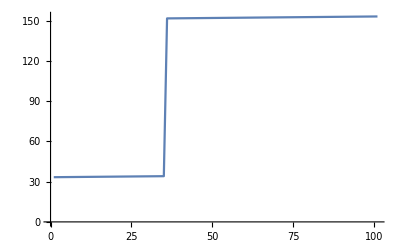

```mathematica
ListLinePlot[times[[1500;;1600]]]
```

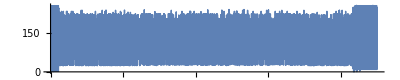

```mathematica
ListLinePlot[int[[220000;;310000;;10]],AspectRatio->0.2,ImageSize->Full,PlotStyle->Thin]
```

```mathematica
int[[220000;;310000;;1]]
```

{12,227,12,226,12,227,12,225,12,227,12,226,12,227,12,226,12,226,12,226,12,227,12,228,12,226,12,226,12,227,12,228,12,239,12,243,12,242,12,243,12,243,12,244,12,243,12,244,12,243,12,245,12,243,12,244,12,244,12,244,12,244,12,243,12,245,12,245,12,244,12,244,12,244,12,242,12,246,12,246,12,244,12,243,12,245,12,245,12,35,73,8,239,2,2,19,233,96,0,101,23,2,4,119,3,16,245,5,0,235,254,16,0,0,0,35,83,24,60,3,2,23,224,12,223,12,225,12,225,12,226,12,226,12,226,12,226,12,227,12,224,12,226,12,227,12,227,12,225,12,226,12,225,12,227,12,226,12,227,12,228,12,228,12,226,12,227,12,227,12,226,12,227,12,227,12,227,12,240,12,240,12,243,12,242,12,244,12,244,12,242,12,243,12,243,12,244,12,243,12,244,12,245,12,243,12,245,12,243,12,245,12,244,12,243,12,244,12,246,12,246,12,244,12,244,12,245,12,245,12,245,12,245,12,35,73,200,69,3,2,43,233,101,0,102,23,241,3,119,3,234,244,4,0,233,254,18,0,0,0,35,83,208,146,3,2,23,221,12,222,12,225,12,225,12,225,12,227,12,225,12,226,12,227,12,225,12,226,12,226,12,227,12,226,12,226,12,226,12,226,12,226,12,227,12,227,12,227,12,227,12,227,12,227,12,227,12,228,12,227,12,228,12,237,12,242,12,243,12,243,12,243,12,244,12,242,12,243,12,243,12,244,12,244,12,243,12,246,12,245,12,244,12,245,12,245,12,243,12,245,12,243,12,245,12,243,12,244,12,244,12,244,12,245,12,245,12,244,12,35,73,120,156,3,2,32,233,94,0,114,23,9,4,165,3,228,244,7,0,234,254,16,0,0,0,35,83,140,233,3,2,23,222,12,224,12,225,12,225,12,225,12,226,12,226,12,225,12,224,12,226,12,224,12,226,12,228,12,227,12,226,12,226,12,227,12,226,12,227,12,227,12,225,12,227,12,226,12,227,12,227,12,227,12,228,12,226,12,239,12,241,12,243,12,243,12,243,12,242,12,244,12,243,12,243,12,245,12,244,12,243,12,245,12,243,12,243,12,243,12,245,12,244,12,243,12,244,12,244,12,244,12,245,12,245,12,245,12,246,12,246,12,244,12,35,73,52,243,3,2,38,233,88,0,94,23,227,3,155,3,233,244,9,0,233,254,19,0,0,0,35,83,64,64,4,2,23,221,12,223,12,223,12,227,12,226,12,226,12,225,12,225,12,225,12,226,12,226,12,226,12,226,12,228,12,226,12,226,12,227,12,226,12,227,12,226,12,224,12,226,12,227,12,226,12,226,12,227,12,227,12,227,12,238,12,240,12,241,12,244,12,244,12,243,12,243,12,243,12,242,12,245,12,242,12,243,12,244,12,245,12,244,12,243,12,244,12,244,12,246,12,244,12,243,12,245,12,245,12,246,12,243,12,245,12,244,12,245,12,35,73,232,73,4,2,37,233,94,0,112,23,220,3,111,3,248,244,3,0,239,254,19,0,0,0,35,83,248,150,4,2,23,223,12,222,12,225,12,227,12,224,12,226,12,227,12,225,12,226,12,226,12,224,12,226,12,228,12,227,12,226,12,227,12,225,12,226,12,228,12,227,12,227,12,228,12,226,12,227,12,227,12,227,12,228,12,226,12,239,12,240,12,243,12,245,12,244,12,243,12,246,12,242,12,244,12,244,12,243,12,244,12,246,12,245,12,243,12,245,12,244,12,244,12,245,12,244,12,243,12,245,12,244,12,245,12,244,12,244,12,246,12,244,12,35,73,160,160,4,2,32,233,102,0,110,23,228,3,122,3,1,245,7,0,234,254,16,0,0,0,35,83,176,237,4,2,23,223,12,221,12,225,12,224,12,225,12,227,12,227,12,225,12,226,12,226,12,226,12,225,12,226,12,225,12,227,12,227,12,226,12,227,12,226,12,227,12,227,12,228,12,227,12,227,12,227,12,226,12,227,12,225,12,240,12,240,12,242,12,241,12,243,12,244,12,244,12,242,12,244,12,245,12,245,12,243,12,244,12,243,12,243,12,244,12,246,12,243,12,244,12,243,12,245,12,244,12,244,12,246,12,246,12,244,12,246,12,244,12,35,73,96,247,4,2,33,233,88,0,99,23,232,3,135,3,211,244,8,0,234,254,18,0,0,0,35,83,104,68,5,2,23,222,12,223,12,224,12,225,12,226,12,225,12,227,12,225,12,225,12,225,12,224,12,227,12,226,12,227,12,227,12,227,12,226,12,226,12,227,12,226,12,228,12,227,12,228,12,227,12,227,12,227,12,227,12,228,12,240,12,241,12,242,12,242,12,243,12,244,12,244,12,243,12,243,12,243,12,243,12,243,12,243,12,245,12,245,12,244,12,244,12,242,12,244,12,244,12,244,12,244,12,245,12,244,12,245,12,244,12,244,12,244,12,35,73,16,78,5,2,35,233,100,0,110,23,251,3,129,3,254,244,253,255,236,254,21,0,0,0,35,83,36,155,5,2,23,222,12,224,12,225,12,225,12,223,12,226,12,226,12,225,12,226,12,226,12,225,12,226,12,227,12,226,12,226,12,227,12,227,12,225,12,227,12,225,12,228,12,226,12,227,12,226,12,225,12,227,12,227,12,226,12,239,12,242,12,243,12,243,12,242,12,243,12,243,12,244,12,244,12,245,12,244,12,243,12,246,12,244,12,244,12,243,12,245,12,244,12,244,12,244,12,245,12,244,12,245,12,245,12,244,12,246,12,244,12,244,12,35,73,204,164,5,2,36,233,96,0,112,23,212,3,146,3,252,244,8,0,233,254,16,0,0,0,35,83,224,241,5,2,23,223,12,223,12,225,12,225,12,226,12,225,12,226,12,226,12,226,12,225,12,226,12,226,12,227,12,227,12,227,12,226,12,228,12,227,12,226,12,227,12,226,12,228,12,229,12,227,12,227,12,227,12,227,12,227,12,240,12,241,12,242,12,242,12,243,12,242,12,243,12,243,12,244,12,244,12,245,12,243,12,245,12,245,12,243,12,243,12,245,12,244,12,244,12,243,12,244,12,245,12,245,12,244,12,244,12,244,12,245,12,243,12,35,73,136,251,5,2,41,233,84,0,105,23,234,3,122,3,235,244,6,0,232,254,18,0,0,0,35,83,144,72,6,2,23,223,12,224,12,226,12,225,12,226,12,226,12,224,12,226,12,226,12,225,12,226,12,226,12,227,12,227,12,226,12,226,12,228,12,226,12,226,12,227,12,225,12,228,12,227,12,227,12,227,12,226,12,228,12,227,12,240,12,243,12,243,12,243,12,243,12,243,12,241,12,244,12,243,12,244,12,243,12,243,12,244,12,244,12,244,12,243,12,245,12,244,12,245,12,244,12,242,12,245,12,245,12,244,12,245,12,243,12,245,12,245,12,35,73,56,82,6,2,35,233,90,0,102,23,226,3,134,3,16,245,8,0,233,254,16,0,0,0,35,83,72,159,6,2,23,223,12,223,12,227,12,225,12,225,12,226,12,225,12,224,12,226,12,227,12,225,12,226,12,227,12,227,12,226,12,227,12,225,12,227,12,227,12,228,12,225,12,226,12,226,12,228,12,226,12,227,12,228,12,228,12,239,12,242,12,242,12,242,12,242,12,245,12,244,12,242,12,244,12,244,12,243,12,244,12,245,12,244,12,244,12,244,12,243,12,245,12,243,12,245,12,243,12,244,12,243,12,244,12,245,12,244,12,244,12,246,12,35,73,240,168,6,2,32,233,100,0,107,23,241,3,134,3,6,245,9,0,234,254,18,0,0,0,35,83,8,246,6,2,23,221,12,223,12,225,12,225,12,225,12,225,12,226,12,226,12,226,12,226,12,227,12,226,12,227,12,227,12,227,12,225,12,227,12,226,12,227,12,227,12,228,12,225,12,226,12,228,12,226,12,228,12,227,12,228,12,239,12,242,12,243,12,244,12,243,12,242,12,243,12,245,12,243,12,245,12,244,12,243,12,244,12,243,12,245,12,243,12,244,12,244,12,244,12,243,12,246,12,243,12,244,12,246,12,246,12,244,12,244,12,245,12,35,73,176,255,6,2,41,233,105,0,101,23,248,3,134,3,228,244,5,0,235,254,18,0,0,0,35,83,184,76,7,2,23,222,12,221,12,225,12,226,12,227,12,225,12,226,12,226,12,225,12,226,12,225,12,228,12,227,12,226,12,225,12,229,12,226,12,226,12,228,12,227,12,227,12,224,12,227,12,225,12,229,12,227,12,228,12,227,12,238,12,240,12,242,12,244,12,244,12,242,12,244,12,245,12,243,12,244,12,241,12,244,12,244,12,243,12,242,12,243,12,244,12,245,12,244,12,245,12,245,12,243,12,245,12,244,12,246,12,246,12,246,12,244,12,35,73,96,86,7,2,38,233,88,0,100,23,248,3,120,3,229,244,18,0,230,254,15,0,0,0,35,83,112,163,7,2,23,222,12,224,12,223,12,225,12,225,12,226,12,226,12,226,12,226,12,225,12,225,12,226,12,227,12,228,12,226,12,226,12,226,12,227,12,226,12,227,12,226,12,227,12,228,12,227,12,227,12,227,12,227,12,228,12,240,12,242,12,242,12,243,12,243,12,243,12,243,12,244,12,243,12,244,12,243,12,244,12,245,12,244,12,244,12,244,12,245,12,245,12,244,12,244,12,245,12,242,12,245,12,245,12,245,12,243,12,244,12,245,12,35,73,24,173,7,2,40,233,100,0,107,23,214,3,123,3,242,244,5,0,233,254,17,0,0,0,35,83,48,250,7,2,23,222,12,223,12,225,12,227,12,225,12,225,12,226,12,226,12,226,12,226,12,225,12,227,12,228,12,226,12,227,12,226,12,227,12,228,12,225,12,226,12,227,12,227,12,227,12,226,12,228,12,228,12,228,12,227,12,239,12,240,12,242,12,244,12,243,12,244,12,243,12,245,12,245,12,241,12,243,12,244,12,245,12,242,12,245,12,243,12,243,12,245,12,243,12,243,12,246,12,244,12,245,12,243,12,245,12,245,12,244,12,245,12,35,73,216,3,8,2,32,233,93,0,109,23,234,3,156,3,222,244,4,0,235,254,17,0,0,0,50,50,50,50,50,50,50,50,54,54,54,88,88,88,236,58,58,58,50,50,50,114,114,114,114,114,114,114,202,202,202,202,236,154,154,27,27,27,219,219,223,223,223,112,112,112,112,200,48,48,50,50,50,114,114,114,114,114,114,98,98,98,200,50,50,50,50,50,50,54,54,54,98,98,98,177,204,50,50,50,91,91,91,95,95,95,112,112,112,112,200,50,50,50,50,50,50,114,114,114,114,114,114,120,120,120,120,234,58,58,58,58,58,58,114,114,114,118,118,118,74,74,74,74,232,56,56,56,58,58,58,114,114,114,118,118,118,118,232,24,24,24,155,155,155,91,91,91,219,219,219,112,112,112,205,50,50,50,54,54,54,114,114,114,118,118,118,98,98,98,204,24,24,24,155,155,155,91,91,91,95,95,95,96,96,96,176,200,50,50,50,50,50,50,114,114,114,118,118,118,96,96,96,204,48,48,48,50,50,50,114,114,114,118,118,118,74,74,74,74,204,50,50,50,50,50,50,50,50,50,201,201,201,201,200,24,24,24,26,26,26,90,90,90,126,126,126,200,200,200,228,200,26,26,26,26,26,26,90,90,90,122,122,122,122,232,56,56,56,58,58,58,126,126,126,118,118,118,200,50,50,50,50,50,50,50,50,50,120,120,120,120,204,50,50,50,50,50,50,114,114,114,118,118,118,118,98,98,98,200,50,50,50,50,50,50,54,54,54,204,50,50,50,50,50,50,114,114,114,118,118,118,118,200,154,154,154,26,26,26,90,90,90,94,94,94,232,50,50,50,50,50,50,223,223,223,112,112,112,112,112,204,48,48,50,50,50,114,114,114,118,118,118,118,112,112,112,236,50,50,50,50,50,54,54,54,106,106,106,232,24,24,24,26,26,26,122,122,122,126,126,126,72,72,72,72,200,56,56,56,58,58,58,114,114,114,114,114,114,114,200,154,154,154,154,154,90,90,90,94,94,94,202,202,202,232,152,152,26,26,26,90,90,90,94,94,94,104,104,104,104,204,50,50,50,50,50,50,219,219,219,122,122,122,122,200,50,50,50,50,50,50,50,50,50,54,54,54,203,203,203,200,152,152,27,27,27,91,91,91,94,94,94,216,216,216,216,200,26,26,26,95,95,95,91,91,91,95,95,95,200,58,58,58,50,50,50,114,114,114,118,118,118,114,114,114,185,200,50,50,50,50,50,50,54,54,54,104,104,104,180,236,50,50,50,91,91,91,95,95,95,122,122,122,189,236,50,50,50,54,54,54,114,114,114,118,118,118,74,74,74,236,56,56,58,58,58,114,114,114,118,118,118,216,216,216,216,200,58,58,58,58,58,58,114,114,114,118,118,118,118,232,58,58,58,58,58,58,114,114,114,114,114,114,114,98,98,98,98,201,50,50,50,50,50,50,50,50,50,104,104,104,232,58,58,58,58,58,58,122,122,122,118,118,118,90,90,90,173,200,50,50,50,50,50,50,114,114,114,118,118,118,118,218,218,237,204,56,56,56,58,58,58,122,122,122,126,126,126,104,104,104,104,202,48,48,54,54,54,50,50,50,54,54,54,54,112,112,112,204,26,26,26,26,26,122,122,122,126,126,126,126,98,98,98,201,50,50,50,50,50,50,54,54,54,54,200,200,200,200,232,154,154,154,26,26,26,90,90,90,90,90,90,202,202,202,202,204,50,50,50,50,50,50,114,114,114,118,118,118,218,218,218,204,24,24,24,58,58,58,122,122,122,126,126,126,206,50,50,50,50,50,50,50,50,50,50,112,112,112,112,200,26,26,26,159,159,159,219,219,219,94,94,94,98,98,98,98,201,50,50,50,50,50,50,91,91,91,104,104,104,234,90,90,90,26,26,26,90,90,90,126,126,126,96,96,96,176,204,26,26,26,26,26,26,122,122,122,126,126,126,112,112,112,112,184,201,50,50,50,50,50,50,114,114,114,54,54,54,114,114,114,114,200,50,50,50,50,50,50,114,114,114,114,114,114,114,218,218,218,218,218,204,58,58,58,50,50,50,114,114,114,118,118,118,118,200,152,152,154,154,154,90,90,90,94,94,94,94,114,114,114,185,204,50,50,50,50,50,50,54,54,54,98,98,98,98,200,56,56,56,50,50,50,114,114,114,118,118,118,104,104,104,180,200,50,50,50,50,50,50,54,54,54,72,72,72,164,204,58,58,58,58,58,58,58,122,122,122,126,126,126,126,218,218,218,218,200,48,48,48,50,50,50,114,114,114,114,114,114,200,50,50,50,91,91,91,91,91,91,98,98,98,98,204,50,50,50,50,50,50,50,50,50,98,98,98,98,204,50,50,50,50,50,50,54,54,54,201,201,201,201,200,88,88,88,58,58,58,122,122,122,126,126,126,126,232,48,48,48,54,54,54,114,114,114,50,50,50,204,24,24,24,26,26,26,90,90,90,94,94,94,200,24,24,24,30,30,30,90,90,90,94,94,94,96,96,96,176,201,50,50,50,50,50,50,54,54,54,204,48,48,48,50,50,50,114,114,114,118,118,118,118,200,200,200,236,50,50,50,50,50,50,114,114,114,54,54,54,88,88,88,88,88,204,58,58,58,58,58,58,122,122,122,118,118,118,200,54,54,54,50,50,50,54,54,54,200,24,24,26,26,26,90,90,90,94,94,94,114,114,114,114,200,54,54,54,50,50,50,54,54,54,90,90,90,90,232,24,24,24,26,26,26,90,90,90,94,94,94,200,200,200,200,200,48,48,48,50,50,50,114,114,114,118,118,118,200,200,200,232,26,26,26,26,26,26,90,90,90,90,90,90,218,218,218,218,232,24,24,24,26,26,26,90,90,90,94,94,94,112,112,112,184,200,50,50,50,219,219,219,95,95,95,98,98,98,200,50,50,50,54,54,54,114,114,114,118,118,118,118,90,90,90,90,90,236,152,152,152,27,27,27,219,219,219,95,95,95,204,50,50,50,219,219,219,95,95,95,232,26,26,26,26,26,26,122,122,122,126,126,126,98,98,98,205,50,50,50,50,50,50,54,54,54,120,120,120,120,200,27,27,27,219,219,219,95,95,95,90,90,90,90,232,58,58,58,58,58,58,122,122,122,126,126,126,90,90,90,90,90,200,48,48,48,50,50,50,50,114,114,114,118,118,118,118,200,200,200,200,26,26,26,155,155,155,91,91,91,94,94,94,94,204,58,58,58,58,58,122,122,122,126,126,126,200,50,50,50,91,91,91,223,223,223,112,112,112,112,201,26,26,26,26,26,26,90,90,90,94,94,94,94,106,106,106,204,58,58,58,58,58,122,122,122,118,118,118,74,74,74,74,232,56,56,56,58,58,58,114,114,114,118,118,118,118,96,96,96,96,200,50,50,50,50,50,50,114,114,114,118,118,118,112,112,112,200,26,26,31,31,31,219,219,219,95,95,95,122,122,122,122,232,56,56,56,58,58,58,114,114,114,118,118,118,200,200,200,232,218,218,218,26,26,26,90,90,90,94,94,94,114,114,114,201,26,26,27,27,27,90,90,90,94,94,94,114,114,114,205,50,50,50,50,50,50,54,54,54,112,112,232,58,58,58,58,58,58,114,114,114,118,118,118,118,202,202,202,232,58,58,58,54,54,54,114,114,114,114,114,114,114,201,24,24,24,26,26,26,122,122,122,126,126,126,126,232,26,26,26,154,154,154,90,90,90,94,94,94,200,50,50,50,50,50,50,91,91,91,106,106,106,106,232,50,50,50,50,50,50,114,114,114,118,118,118,118,96,96,96,96,205,26,26,26,26,26,90,90,90,126,126,126,202,202,202,232,50,50,50,50,50,50,219,219,219,200,24,24,24,26,26,26,90,90,90,94,94,94,114,114,114,114,201,50,50,50,54,54,54,114,114,114,114,114,114,114,114,114,205,50,50,50,50,50,50,114,114,114,118,118,118,120,120,120,120,120,232,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,204,58,58,58,58,58,58,114,114,114,118,118,118,202,202,202,202,200,58,58,58,62,62,62,114,114,114,118,118,118,232,24,24,24,155,155,155,91,91,91,91,91,91,114,114,114,114,200,54,54,54,50,50,50,54,54,54,98,98,98,205,24,24,24,30,30,30,90,90,90,126,126,126,104,104,104,200,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,236,58,58,58,58,58,58,122,122,122,118,118,118,118,202,202,202,202,232,48,48,48,50,50,50,114,114,114,118,118,118,118,200,24,24,24,26,26,26,122,122,122,126,126,126,98,98,204,48,48,48,50,50,50,50,50,50,54,54,54,236,50,50,50,50,50,50,50,54,54,54,72,72,72,204,50,50,50,50,50,50,50,50,50,50,50,50,50,236,154,154,154,30,30,30,90,90,90,90,90,90,200,24,24,24,159,159,159,91,91,91,223,223,223,223,112,112,112,201,48,48,50,50,50,114,114,114,118,118,118,120,120,120,120,202,50,50,50,50,50,50,114,114,114,118,118,118,106,106,106,181,200,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,216,200,48,48,48,50,50,50,114,114,114,118,118,118,200,200,200,200,206,26,26,26,26,26,26,122,122,122,126,126,126,74,74,74,74,232,56,56,56,58,58,58,122,122,122,114,114,114,200,24,24,26,26,26,90,90,90,90,90,90,98,98,98,98,206,50,50,50,50,50,50,54,54,54,122,122,122,122,232,56,56,56,50,50,50,114,114,114,114,114,114,200,200,200,232,48,48,48,50,50,50,114,114,114,114,118,118,118,118,216,216,216,216,204,26,26,26,26,26,26,90,90,90,90,90,90,90,90,204,24,24,24,155,155,155,219,219,219,218,218,218,218,200,24,24,24,26,26,26,90,90,90,94,94,94,112,112,112,112,200,50,50,50,50,50,50,54,54,54,74,74,74,200,25,25,25,27,27,27,90,90,90,90,90,90,112,112,112,184,204,50,50,50,50,50,50,219,219,219,218,218,218,218,200,50,50,50,219,219,219,95,95,95,203,203,203,229,204,152,152,152,26,26,26,90,90,90,90,90,90,90,204,50,50,50,50,50,50,95,95,95,200,26,26,26,58,58,58,122,122,122,122,122,122,98,98,98,98,200,50,50,50,50,50,50,54,54,54,232,154,154,155,155,155,218,218,218,218,90,90,90,202,202,202,232,26,26,26,26,26,26,90,90,90,94,94,94,94,75,75,75,200,24,24,26,26,26,90,90,90,90,90,90,112,112,112,200,50,50,50,50,50,50,219,219,219,114,114,114,114,201,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,204,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,88,200,58,58,58,58,58,58,122,122,122,118,118,118,219,219,219,219,237,204,26,26,26,58,58,58,122,122,122,126,126,126,126,218,218,237,200,24,24,24,26,26,26,122,122,122,126,126,126,72,72,72,164,200,50,50,50,50,50,50,54,54,54,232,154,154,154,27,27,27,219,219,219,223,223,223,98,98,98,98,177,204,48,48,48,50,50,50,114,114,114,118,118,118,114,114,114,203,58,58,58,62,62,62,122,122,122,122,122,122,203,203,203,229,200,27,27,26,26,26,90,90,90,94,94,94,219,219,219,219,232,48,48,48,50,50,50,114,114,114,114,114,114,204,50,50,50,50,50,50,54,54,54,54,98,98,98,204,50,50,50,50,50,50,114,114,114,118,118,118,106,106,106,106,200,50,50,50,219,219,219,223,223,223,120,120,120,236,26,26,26,26,26,26,122,122,122,126,126,126,204,27,27,27,219,219,219,95,95,95,232,56,56,62,62,62,114,114,114,114,114,114,204,155,155,155,155,155,219,219,219,219,219,219,112,112,200,155,155,31,31,31,91,91,91,219,219,219,112,112,112,112,112,201,50,50,50,50,50,50,54,54,54,216,216,216,216,204,26,26,30,30,30,90,90,90,122,122,122,204,50,50,50,50,50,50,223,223,223,200,24,24,24,26,26,26,90,90,90,126,126,126,98,98,98,200,54,54,54,50,50,50,50,50,50,98,98,98,98,204,48,48,50,50,50,114,114,114,118,118,118,88,88,88,88,232,50,50,50,50,50,50,114,114,114,54,54,54,200,200,200,200,26,26,26,58,58,58,122,122,122,126,126,126,126,200,48,48,50,50,50,114,114,114,114,114,114,232,56,56,56,50,50,50,114,114,114,114,118,118,118,114,114,185,204,48,48,50,50,50,114,114,114,118,118,118,200,48,48,48,50,50,50,114,114,114,118,118,118,120,120,120,120,204,56,56,56,58,58,58,122,122,122,126,126,126,201,201,201,201,228,204,58,58,58,58,58,58,122,122,122,114,114,114,114,74,74,74,74,200,153,153,27,27,27,90,90,90,94,94,94,94,200,153,153,153,155,155,155,90,90,90,94,94,94,94,114,114,114,185,200,58,58,58,62,62,62,122,122,122,126,126,126,200,50,50,50,50,50,50,54,54,54,112,112,112,112,204,48,48,48,50,50,50,114,114,114,118,118,118,96,96,96,96,204,50,50,50,50,50,50,118,118,118,50,50,50,106,106,106,106,106,232,56,56,56,58,58,58,114,114,114,118,118,118,118,72,72,72,204,112,112,112,50,50,50,114,114,114,118,118,118,118,204,26,26,26,58,58,58,122,122,122,126,126,126,98,98,98,98,200,50,50,50,50,50,50,50,50,50,104,104,104,200,50,50,50,50,50,50,114,114,114,114,114,114,114,98,98,98,98,201,58,58,58,58,58,58,122,122,122,118,118,118,74,74,74,74,204,48,48,48,50,50,50,114,114,114,118,118,118,200,200,200,236,56,56,56,58,58,58,122,122,122,114,114,114,218,218,218,237,200,26,26,26,26,26,26,90,90,90,126,126,126,126,204,155,155,155,219,219,219,95,95,95,216,216,216,216,236,200,56,56,56,58,58,58,114,114,114,118,118,118,118,74,74,74,74,165,200,27,27,27,27,27,90,90,90,90,90,90,219,219,219,219,204,155,155,155,219,219,219,95,95,95,204,58,58,58,58,58,58,122,122,122,118,118,118,200,155,155,155,91,91,91,95,95,95,98,98,98,205,48,48,48,50,50,50,50,50,50,54,54,54,104,104,104,180,204,58,58,50,50,50,114,114,114,118,118,118,106,106,106,181,204,50,50,50,50,50,50,54,54,54,219,219,219,219,232,56,56,58,58,58,122,122,122,126,126,126,120,120,120,120,200,27,27,27,27,27,27,91,91,91,222,222,222,222,112,112,112,112,200,154,154,159,159,159,90,90,90,94,94,94,114,114,114,200,50,50,50,50,50,50,54,54,54,201,201,201,228,200,50,50,50,50,50,50,54,54,54,54,90,90,90,232,26,26,26,26,26,26,90,90,90,126,126,126,219,219,219,237,204,24,24,24,26,26,26,122,122,122,126,126,126,200,155,155,154,154,154,90,90,90,94,94,94,204,50,50,50,50,50,114,114,114,54,54,54,114,114,114,114,185,200,31,31,31,219,219,219,219,219,219,104,104,104,236,48,48,48,54,54,54,114,114,114,118,118,118,219,219,232,27,27,159,159,159,219,219,219,91,91,91,200,56,56,56,58,58,58,122,122,122,122,122,122,122,114,114,114,114,185,207,50,50,50,91,91,91,91,91,91,112,112,112,184,200,155,155,155,219,219,219,223,223,223,98,98,98,205,50,50,50,50,50,50,114,114,114,54,54,54,104,104,104,232,50,50,50,50,50,50,114,114,114,118,118,118,90,90,90,236,58,58,58,58,58,58,122,122,122,126,126,126,200,200,200,228,204,24,24,24,58,58,58,122,122,122,122,122,122,122,98,98,98,200,50,50,50,50,50,50,91,91,91,122,122,122,122,189,200,54,54,54,50,50,50,54,54,54,104,104,104,104,200,50,50,50,50,50,50,114,114,114,114,114,114,72,72,72,164,206,154,154,154,27,27,27,91,91,91,90,90,90,96,96,96,200,25,25,25,27,27,27,90,90,90,90,90,90,201,201,201,201,228,204,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,236,122,122,122,54,54,54,114,114,114,118,118,118,202,202,202,232,24,24,24,26,26,26,90,90,90,94,94,94,94,200,24,24,24,30,30,30,90,90,90,126,126,126,204,50,50,50,91,91,91,95,95,95,122,122,122,122,122,236,56,56,56,62,62,62,114,114,114,114,114,114,120,120,120,120,232,152,152,27,27,27,90,90,90,90,90,90,216,216,216,232,50,50,50,50,50,50,114,114,114,118,118,118,118,204,152,152,155,155,155,219,219,219,219,219,219,96,96,96,96,201,24,24,30,30,30,90,90,90,94,94,94,114,114,114,203,50,50,50,50,50,50,50,50,50,50,106,106,106,106,236,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,236,50,50,50,50,50,50,114,114,114,118,118,118,200,200,200,236,26,26,26,155,155,155,90,90,90,90,90,90,90,200,50,50,50,219,219,219,91,91,91,112,112,112,112,200,50,50,50,50,50,50,50,50,50,54,54,54,98,98,98,98,200,50,50,50,50,50,50,114,114,114,118,118,118,118,74,74,74,232,24,24,24,62,62,62,122,122,122,122,122,122,72,72,72,72,236,50,50,50,50,50,50,223,223,223,232,50,50,50,50,50,50,54,54,54,232,152,152,155,155,155,91,91,91,95,95,95,216,216,216,216,232,24,24,24,26,26,26,90,90,90,126,126,126,114,114,114,114,204,54,54,54,50,50,50,54,54,54,54,218,218,218,218,204,153,153,155,155,155,91,91,91,222,222,222,222,200,153,153,27,27,27,91,91,91,222,222,222,222,200,26,26,26,58,58,58,122,122,122,122,122,122,114,114,114,201,50,50,50,50,50,50,54,54,54,54,112,112,112,232,50,50,50,50,50,50,219,219,219,122,122,189,204,50,50,50,50,50,50,54,54,54,203,203,203,232,25,25,25,27,27,27,91,91,91,95,95,95,96,96,96,96,176,200,50,50,50,50,50,50,114,114,114,114,114,114,204,26,26,26,26,26,26,90,90,90,94,94,94,200,48,48,48,50,50,50,50,50,50,54,54,54,236,50,50,50,50,50,50,54,54,54,74,74,74,236,50,50,50,50,50,50,54,54,54,54,203,203,203,203,232,56,56,56,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,54,54,54,200,26,26,155,155,155,90,90,90,90,90,90,114,114,114,114,201,50,50,50,50,50,50,54,54,54,54,112,112,112,202,50,50,50,50,50,50,114,114,114,118,118,118,106,106,106,236,155,155,27,27,27,218,218,218,90,90,90,219,219,219,204,48,48,48,50,50,50,114,114,114,118,118,118,200,155,155,155,155,155,219,219,219,95,95,95,112,112,112,201,50,50,50,50,50,50,54,54,54,54,90,90,90,173,204,48,48,48,50,50,50,114,114,114,118,118,118,200,27,27,27,91,91,91,223,223,223,96,96,96,200,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,205,216,216,216,154,154,154,90,90,90,94,94,94,94,200,200,236,58,58,58,58,58,58,122,122,122,122,122,122,122,122,122,122,189,204,154,154,155,155,155,91,91,91,218,218,218,216,216,216,216,232,56,56,56,58,58,58,122,122,122,118,118,118,118,98,98,98,177,200,154,154,27,27,27,91,91,91,218,218,218,204,50,50,50,50,50,50,95,95,95,88,88,88,88,200,50,50,50,50,50,50,54,54,54,88,88,88,88,202,50,50,50,50,50,50,114,114,114,114,114,114,114,204,26,26,26,27,27,27,91,91,91,95,95,95,200,50,50,50,50,50,50,114,114,114,54,54,54,98,98,98,177,202,26,26,26,27,27,27,219,219,219,219,219,219,112,112,112,204,48,48,48,50,50,50,114,114,114,118,118,118,118,120,120,120,188,204,50,50,50,50,50,50,50,50,50,50,72,72,72,202,50,50,50,50,50,50,114,114,114,118,118,118,219,219,219,219,232,50,50,50,91,91,91,95,95,95,200,88,88,88,26,26,26,122,122,122,126,126,126,96,96,96,96,206,58,58,58,58,58,58,122,122,122,122,122,122,122,98,98,98,98,204,48,48,48,50,50,50,114,114,114,54,54,54,120,120,120,120,188,200,50,50,50,50,50,50,50,50,50,50,50,50,88,88,88,88,204,58,58,58,62,62,62,114,114,114,118,118,118,204,152,152,152,155,155,155,91,91,91,95,95,95,96,96,96,176,204,50,50,50,50,50,50,91,91,91,96,96,96,96,201,48,48,48,54,54,54,114,114,114,114,114,114,114,74,74,74,165,200,50,50,50,50,50,50,91,91,91,216,216,216,216,204,50,50,50,50,50,50,54,54,54,54,200,200,200,200,228,200,58,58,58,58,58,58,122,122,122,118,118,118,202,202,202,202,229,200,24,24,155,155,155,90,90,90,94,94,94,72,72,72,72,200,50,50,50,219,219,219,223,223,223,120,120,120,120,204,26,26,26,26,26,26,122,122,122,126,126,126,74,74,200,50,50,50,50,50,50,50,50,50,50,72,72,72,164,200,25,25,25,155,155,155,90,90,90,90,90,90,90,201,201,201,228,204,26,26,26,26,26,26,90,90,90,126,126,126,200,155,155,155,219,219,219,223,223,223,204,56,56,56,62,62,62,122,122,122,126,126,126,126,114,114,114,201,26,26,26,26,26,26,122,122,122,126,126,126,203,203,203,203,203,200,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,72,164,204,24,24,26,26,26,90,90,90,90,90,90,204,26,26,26,26,26,90,90,90,126,126,126,114,114,114,200,25,25,25,155,155,219,219,219,222,222,222,204,25,25,27,27,27,91,91,91,218,218,218,218,114,114,114,200,26,26,26,26,26,26,90,90,90,122,122,122,74,74,74,74,204,50,50,50,50,50,50,54,54,54,54,104,104,104,104,204,50,50,50,50,50,50,54,54,54,106,106,106,106,200,50,50,50,50,50,50,114,114,114,114,114,114,202,202,202,202,202,204,24,24,24,27,27,27,218,218,218,94,94,94,216,216,216,204,154,154,155,155,155,218,218,218,90,90,90,200,26,26,26,154,154,154,90,90,90,90,90,90,98,98,98,98,204,155,155,155,219,219,219,223,223,223,104,104,104,180,206,48,48,48,50,50,50,50,50,50,54,54,54,54,219,219,219,237,204,26,26,26,58,58,58,122,122,122,126,126,126,204,152,152,155,155,155,219,219,219,222,222,222,222,98,98,98,206,50,50,50,50,50,50,223,223,223,200,154,154,154,26,26,26,90,90,90,94,94,94,94,98,98,98,98,200,24,24,24,155,155,155,219,219,219,94,94,94,94,120,120,236,50,50,50,50,50,114,114,114,118,118,118,96,96,96,96,204,26,26,154,154,154,90,90,90,90,90,90,218,218,218,237,200,50,50,50,50,50,50,54,54,54,54,114,114,114,185,200,155,155,155,219,219,219,95,95,95,218,218,218,218,237,204,26,26,26,26,26,26,122,122,122,122,122,122,98,98,98,98,200,48,48,48,50,50,50,114,114,114,118,118,118,118,104,104,104,104,202,48,48,48,50,50,50,50,50,50,54,54,54,54,203,203,203,203,229,200,26,26,26,155,155,155,219,219,219,94,94,94,216,216,216,216,200,50,50,50,50,50,50,50,50,50,98,98,98,201,26,26,26,155,155,155,219,219,219,222,222,222,222,114,114,185,204,50,50,50,50,50,50,114,114,114,118,118,118,118,96,96,96,176,200,50,50,50,50,50,50,54,54,54,104,104,104,104,180,200,50,50,50,50,50,50,114,114,114,118,118,118,202,202,202,202,202,200,26,26,26,26,26,26,122,122,122,122,122,122,122,204,24,24,24,26,26,26,94,94,94,90,90,90,90,98,98,98,98,206,58,58,58,58,58,58,114,114,114,118,118,118,118,98,98,98,200,48,48,50,50,50,114,114,114,118,118,118,88,88,88,172,200,50,50,50,50,50,50,50,54,54,54,54,88,88,88,88,200,50,50,50,50,50,50,114,114,114,114,114,114,114,218,218,218,218,204,56,56,58,58,58,122,122,122,118,118,118,118,200,155,155,155,219,219,219,95,95,95,114,114,114,114,200,48,48,48,50,50,50,50,50,50,54,54,54,96,96,96,96,204,48,48,48,50,50,50,50,50,50,54,54,54,54,104,104,104,236,50,50,50,219,219,219,95,95,95,217,217,217,236,26,26,26,26,26,26,90,90,90,94,94,94,200,24,24,24,155,155,155,91,91,91,219,219,219,200,200,200,200,200,50,50,50,50,50,50,54,54,54,112,112,112,184,200,58,58,58,58,58,58,122,122,122,122,122,122,122,90,90,90,90,204,24,24,24,30,30,30,90,90,90,90,90,90,90,88,88,88,88,236,48,48,54,54,54,114,114,114,114,118,118,118,118,238,27,27,27,27,27,27,219,219,219,222,222,222,222,236,25,25,25,155,155,219,219,219,94,94,94,96,96,96,176,204,50,50,50,50,50,50,114,114,114,114,114,114,218,218,218,204,50,50,50,50,50,50,50,50,50,50,50,50,200,152,152,152,26,26,26,90,90,90,94,94,94,94,120,120,120,120,204,48,48,48,50,50,50,114,114,114,118,118,118,118,106,106,106,181,200,50,50,50,50,50,50,114,114,114,118,118,118,118,218,218,218,218,204,48,48,48,50,50,50,114,114,114,118,118,118,118,200,200,200,200,232,152,152,31,31,31,90,90,90,90,90,90,90,204,50,50,50,50,50,50,54,54,54,54,200,24,24,24,30,30,30,90,90,90,122,122,122,96,96,96,200,50,50,50,50,50,50,50,54,54,54,106,106,106,204,50,50,50,50,50,50,114,114,114,118,118,118,218,218,218,218,204,50,50,50,91,91,91,91,91,91,217,217,217,236,200,26,26,26,58,58,58,122,122,122,122,126,126,126,126,204,50,50,50,50,50,50,50,50,50,54,54,54,98,98,98,177,204,24,24,24,58,58,58,122,122,122,126,126,126,120,120,120,206,48,48,48,50,50,50,114,114,114,118,118,118,122,122,122,232,50,50,50,50,50,50,114,114,114,118,118,118,122,122,232,56,56,56,58,58,58,122,122,122,118,118,118,216,216,216,216,236,204,26,26,26,26,26,26,122,122,122,122,122,122,122,204,50,50,50,50,50,50,50,50,50,54,54,54,98,98,98,98,200,50,50,50,50,50,50,54,54,54,112,112,112,112,200,48,48,50,50,50,50,50,50,50,50,50,98,98,98,205,50,50,50,50,50,50,54,54,54,54,90,90,90,90,200,50,50,50,50,50,50,54,54,54,200,26,26,155,155,155,219,219,219,94,94,94,202,202,202,202,232,26,26,26,159,159,159,91,91,91,94,94,94,114,114,114,185,204,50,50,50,50,50,50,54,54,54,120,120,120,188,204,50,50,50,91,91,91,223,223,223,122,122,122,122,200,58,58,58,58,58,58,114,114,114,118,118,118,202,202,202,202,229,200,50,50,50,50,50,50,114,114,114,54,54,54,204,154,154,26,26,26,90,90,90,94,94,94,200,154,154,26,26,26,90,90,90,94,94,94,94,98,98,98,98,177,205,50,50,50,50,50,50,223,223,223,104,104,104,104,180,202,48,48,48,50,50,50,114,114,114,114,114,114,114,74,74,74,232,50,50,50,50,50,50,114,114,114,118,118,118,216,216,216,236,200,50,50,50,50,50,50,50,50,50,50,50,204,26,26,26,155,155,155,90,90,90,90,90,90,200,50,50,50,50,50,50,54,54,54,96,96,96,96,200,50,50,50,50,50,54,54,54,104,104,104,236,48,48,48,50,50,50,114,114,114,54,54,54,219,219,219,237,232,24,24,24,58,58,58,122,122,122,126,126,126,126,200,152,152,152,155,155,155,91,91,91,223,223,223,223,114,114,185,206,50,50,50,50,50,50,54,54,54,122,122,122,122,200,48,48,48,50,50,50,114,114,114,118,118,118,118,88,88,88,232,50,50,50,50,50,50,54,54,54,88,88,88,88,204,155,155,155,155,155,219,219,219,223,223,223,200,56,56,56,58,58,58,122,122,122,118,118,118,118,96,96,96,176,205,56,56,56,58,58,58,114,114,114,118,118,118,118,200,50,50,50,219,219,219,219,219,219,200,24,24,24,27,27,27,91,91,91,223,223,223,216,216,216,216,204,56,56,56,58,58,58,114,114,114,118,118,118,112,112,112,112,201,54,54,54,50,50,50,54,54,54,114,114,114,114,185,205,48,48,48,50,50,50,114,114,114,118,118,118,118,112,112,112,200,216,216,27,27,27,90,90,90,94,94,94,216,216,216,236,200,50,50,50,50,50,50,54,54,54,54,202,202,202,202,200,48,48,48,50,50,50,114,114,114,118,118,118,112,112,112,112,205,50,50,50,91,91,91,91,91,91,114,114,114,114,201,50,50,50,50,50,50,50,50,54,54,54,98,98,98,98,177,204,48,48,48,50,50,50,114,114,114,114,118,118,118,72,72,72,72,200,24,24,26,26,26,94,94,94,94,94,94,202,50,50,50,50,50,50,54,54,54,232,24,24,24,58,58,58,122,122,122,126,126,126,112,112,112,184,201,50,50,50,50,50,50,91,91,91,98,98,98,98,177,200,50,50,50,50,50,50,114,114,114,54,54,54,74,74,232,48,48,48,50,50,50,114,114,114,114,114,114,114,217,217,217,217,204,24,24,24,26,26,26,90,90,90,126,126,126,202,202,229,204,58,58,58,58,58,58,114,114,114,118,118,118,118,204,216,216,155,155,155,218,218,218,94,94,94,94,96,96,96,204,48,48,48,50,50,50,50,50,50,54,54,54,122,122,122,122,189,200,50,50,50,50,50,50,50,50,50,54,54,54,74,74,74,74,200,56,56,50,50,50,114,114,114,118,118,118,200,200,200,232,26,26,58,58,58,122,122,122,126,126,126,74,74,74,74,204,50,50,50,50,50,50,50,50,50,98,98,98,177,204,50,50,50,91,91,91,95,95,95,96,96,96,201,48,48,48,50,50,50,114,114,114,118,118,118,118,204,50,50,50,50,50,50,114,114,114,118,118,118,118,203,203,203,232,48,48,50,50,50,114,114,114,118,118,118,216,216,216,236,200,26,26,26,26,26,26,122,122,122,126,126,126,74,74,74,74,165,204,50,50,50,50,50,50,114,114,114,118,118,118,204,56,56,56,58,58,58,114,114,114,114,118,118,118,120,120,120,188,200,50,50,50,50,50,50,50,50,50,74,74,74,74,200,50,50,50,50,50,50,114,114,114,118,118,118,202,202,202,229,204,48,48,50,50,50,114,114,114,114,114,114,200,200,200,204,50,50,50,50,50,50,114,114,114,114,114,114,200,50,50,50,219,219,219,223,223,223,114,114,114,114,201,152,152,155,155,155,90,90,90,94,94,94,120,120,120,120,204,48,48,48,50,50,50,114,114,114,114,54,54,54,122,122,122,189,204,154,154,154,26,26,26,90,90,90,90,90,90,90,202,202,232,27,27,27,219,219,219,223,223,223,200,50,50,50,50,50,50,114,114,114,118,118,118,112,112,112,112,201,50,50,50,50,50,50,114,114,114,118,118,118,118,96,96,96,204,48,48,54,54,54,114,114,114,118,118,118,216,216,216,202,50,50,50,50,50,50,54,54,54,114,114,114,185,204,50,50,50,54,54,114,114,114,54,54,54,104,104,104,104,200,50,50,50,50,50,50,54,54,54,120,120,120,120,204,48,48,48,50,50,50,114,114,114,114,114,114,200,24,24,24,26,26,26,122,122,122,126,126,126,200,48,48,48,50,50,50,114,114,114,118,118,118,96,96,96,96,201,154,154,155,155,155,219,219,219,219,219,219,114,114,114,200,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,72,200,155,155,155,219,219,219,219,219,219,217,217,217,217,217,204,58,58,58,58,58,58,122,122,122,118,118,118,204,24,24,24,27,27,27,219,219,219,94,94,94,94,88,88,88,88,204,50,50,50,50,50,50,54,54,54,200,154,154,154,155,155,155,90,90,90,94,94,94,94,112,112,112,112,205,48,48,48,50,50,50,114,114,114,54,54,54,204,24,24,24,58,58,58,122,122,122,126,126,126,202,50,50,50,50,50,50,114,114,114,118,118,118,204,152,152,152,26,26,26,90,90,90,94,94,94,200,24,24,24,155,155,155,219,219,219,223,223,223,112,112,112,201,50,50,50,91,91,91,91,91,91,106,106,106,106,204,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,200,48,48,48,50,50,50,114,114,114,114,114,114,200,200,200,200,232,50,50,50,50,50,50,114,114,114,118,118,118,204,152,152,155,155,155,90,90,90,94,94,94,204,27,27,27,91,91,91,95,95,95,114,114,114,200,154,154,27,27,27,91,91,91,95,95,95,90,90,90,90,200,153,153,27,27,27,90,90,90,94,94,94,217,217,217,200,24,24,24,58,58,58,122,122,122,126,126,126,200,154,154,154,155,155,155,91,91,91,95,95,95,200,24,24,24,58,58,58,122,122,122,126,126,126,112,112,112,201,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,177,205,50,50,50,50,50,50,54,54,54,54,114,114,114,204,50,50,50,50,50,50,54,54,54,54,88,88,88,88,204,48,48,48,50,50,50,114,114,114,118,118,118,238,58,58,58,58,58,58,122,122,122,122,114,114,114,200,50,50,50,50,50,50,95,95,95,204,50,50,50,50,50,50,50,50,50,50,200,50,50,50,54,54,54,114,114,114,118,118,118,118,218,218,218,237,204,24,24,24,58,58,58,122,122,122,122,122,122,122,200,200,200,200,204,50,50,50,50,50,50,114,114,114,114,114,114,122,122,122,206,50,50,50,50,50,50,50,50,50,50,200,24,24,24,26,26,26,90,90,90,126,126,126,96,96,96,204,50,50,50,50,50,50,54,54,54,106,106,106,236,50,50,54,54,54,114,114,114,114,114,114,114,90,90,90,204,48,48,48,50,50,50,114,114,114,54,54,54,104,104,104,104,204,50,50,50,50,50,50,54,54,54,90,90,232,50,50,50,50,50,50,114,114,114,114,114,114,203,203,203,203,200,50,50,50,50,50,50,54,54,54,54,236,26,26,26,62,62,62,122,122,122,122,122,122,122,96,96,204,50,50,50,50,50,50,54,54,54,54,114,114,114,185,204,56,56,56,58,58,58,122,122,122,126,126,126,104,104,104,104,204,50,50,50,50,50,50,50,50,50,74,74,74,74,200,58,58,58,58,58,114,114,114,114,114,114,114,218,218,218,200,50,50,50,50,50,50,114,114,114,54,54,54,232,58,58,58,58,58,58,58,122,122,122,114,114,114,114,112,112,201,159,159,159,219,219,219,223,223,223,122,122,122,189,204,50,50,50,50,50,50,91,91,91,104,104,104,180,200,48,48,48,54,54,54,50,50,50,54,54,54,219,219,219,219,204,58,58,58,58,58,58,122,122,122,126,126,126,126,200,200,200,200,200,50,50,50,219,219,219,91,91,91,206,50,50,50,91,91,91,95,95,95,96,96,96,96,200,50,50,50,50,50,50,54,54,54,54,112,112,112,112,200,56,56,56,58,58,58,114,114,114,118,118,118,104,104,104,104,200,155,155,155,219,219,219,95,95,95,74,74,74,74,165,200,56,56,56,58,58,58,118,118,118,114,114,114,216,216,216,216,200,56,56,56,58,58,58,114,114,114,114,114,114,236,58,58,58,54,54,54,114,114,114,118,118,118,96,96,96,205,56,56,56,58,58,58,122,122,122,118,118,118,96,96,96,176,200,56,56,56,58,58,58,122,122,122,114,114,114,88,88,88,88,200,48,48,48,50,50,50,114,114,114,118,118,118,218,218,218,218,237,200,48,48,48,50,50,50,114,114,114,118,118,118,232,24,24,24,27,27,27,90,90,90,94,94,94,94,98,98,98,205,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,201,27,27,27,91,91,91,219,219,219,104,104,104,204,24,24,24,58,58,58,122,122,122,126,126,126,126,72,72,72,72,200,50,50,50,50,50,50,114,114,114,118,118,118,218,218,218,237,200,24,24,24,58,58,122,122,122,122,122,122,96,96,96,96,200,50,50,50,50,50,50,54,54,54,54,98,98,98,204,154,154,159,159,159,219,219,219,90,90,90,98,98,98,98,200,152,152,152,26,26,26,90,90,90,90,90,90,72,72,164,204,24,24,154,154,154,90,90,90,94,94,94,94,88,88,88,232,50,50,50,50,50,114,114,114,114,114,114,232,54,54,54,50,50,50,54,54,54,54,236,155,155,155,91,91,91,223,223,223,98,98,98,98,205,58,58,58,58,58,58,122,122,122,122,122,122,74,74,74,165,200,56,56,56,58,58,58,122,122,122,126,126,126,88,88,172,204,48,48,48,50,50,50,114,114,114,114,114,114,114,216,216,216,216,200,26,26,26,155,155,155,91,91,91,222,222,222,222,200,24,24,24,30,30,30,90,90,90,126,126,126,126,200,48,48,50,50,50,114,114,114,118,118,118,91,91,91,173,200,50,50,50,50,50,50,54,54,54,219,219,219,237,200,48,48,48,50,50,50,114,114,114,118,118,118,96,96,96,96,201,155,155,155,91,91,91,223,223,223,200,50,50,50,50,50,50,50,50,50,50,54,54,54,218,218,218,200,48,48,48,50,50,50,114,114,114,114,118,118,118,216,216,216,216,236,204,154,154,154,26,26,26,90,90,90,94,94,94,114,114,114,114,185,200,58,58,58,50,50,50,114,114,114,118,118,118,118,200,56,56,56,58,58,58,122,122,122,126,126,126,112,112,112,112,184,200,50,50,50,50,50,50,54,54,54,114,114,114,232,58,58,58,58,58,58,114,114,114,118,118,118,106,106,106,106,181,204,50,50,50,91,91,91,95,95,95,200,58,58,58,58,58,58,122,122,122,118,118,118,118,204,27,27,27,91,91,91,91,91,91,98,98,98,200,48,48,48,50,50,50,114,114,114,118,118,118,118,96,96,96,96,202,155,155,155,219,219,219,95,95,95,106,106,106,106,204,50,50,50,50,50,50,50,50,50,54,54,54,203,203,203,203,203,200,24,24,155,155,155,91,91,91,219,219,219,200,200,200,228,204,58,58,58,50,50,50,114,114,114,114,114,114,200,90,90,90,27,27,27,91,91,91,222,222,222,222,114,114,114,114,204,155,155,155,91,91,91,91,91,91,96,96,96,96,96,204,26,26,26,58,58,58,122,122,122,122,122,122,90,90,90,90,232,26,26,26,58,58,58,122,122,122,122,122,122,122,204,120,120,58,58,58,114,114,114,118,118,118,98,98,98,98,205,154,154,27,27,27,223,223,223,95,95,95,112,112,112,205,50,50,50,50,50,50,54,54,54,54,98,98,98,98,205,50,50,50,50,50,50,54,54,54,54,120,120,120,120,236,154,154,155,155,155,219,219,219,222,222,222,90,90,90,200,50,50,50,50,50,50,114,114,114,118,118,118,120,120,120,200,155,155,155,91,91,91,223,223,223,200,27,27,27,155,155,155,219,219,219,95,95,95,200,27,27,27,219,219,219,95,95,95,232,56,56,56,54,54,54,114,114,114,118,118,118,104,104,104,104,204,48,48,48,50,50,50,50,50,50,54,54,54,90,90,90,90,232,48,48,48,50,50,50,114,114,114,114,118,118,118,232,24,24,24,58,58,58,122,122,122,126,126,126,114,114,114,114,204,50,50,50,50,50,50,54,54,54,114,114,114,114,185,204,152,152,31,31,31,219,219,219,91,91,91,120,120,120,120,200,50,50,50,50,50,50,114,114,114,118,118,118,118,120,120,120,236,50,50,50,219,219,219,95,95,95,74,74,74,236,48,48,48,50,50,50,114,114,114,118,118,118,200,56,56,56,62,62,62,122,122,122,114,114,114,114,98,98,98,177,205,26,26,26,26,26,26,90,90,90,90,90,90,114,114,114,114,201,153,153,155,155,155,90,90,90,94,94,94,112,112,112,204,50,50,50,50,50,50,50,50,50,54,54,54,89,89,89,89,172,204,50,50,50,50,50,50,114,114,114,114,118,118,118,118,202,202,202,232,54,54,54,50,50,50,50,50,50,88,88,88,88,204,50,50,50,50,50,50,118,118,118,114,114,114,217,217,217,217,204,58,58,58,58,58,58,122,122,122,122,118,118,118,74,74,74,204,56,56,56,58,58,58,122,122,122,118,118,118,112,112,112,205,155,155,155,91,91,91,223,223,223,98,98,98,203,26,26,26,26,26,26,90,90,90,126,126,126,122,122,189,200,48,48,48,50,50,50,50,50,50,54,54,54,73,73,73,73,204,56,56,56,50,50,50,114,114,114,118,118,118,118,216,216,216,236,50,50,50,50,50,50,54,54,54,114,114,200,50,50,50,50,50,50,50,50,50,96,96,96,176,204,24,24,159,159,159,219,219,219,223,223,223,204,50,50,50,50,50,50,54,54,54,106,106,106,204,24,24,24,27,27,27,219,219,219,94,94,94,104,104,104,104,232,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,204,50,50,50,50,50,50,114,114,114,118,118,118,204,48,48,48,50,50,50,114,114,114,118,118,118,118,96,96,96,200,91,91,91,26,26,26,90,90,90,94,94,94,74,74,74,165,200,50,50,50,54,54,54,114,114,114,118,118,118,218,218,218,218,200,48,48,48,50,50,50,50,114,114,114,118,118,118,216,216,216,236,204,26,26,26,26,26,90,90,90,94,94,94,94,200,26,26,26,26,26,26,90,90,90,94,94,94,98,98,98,201,25,25,25,155,155,155,218,218,218,94,94,94,96,96,96,96,200,26,26,26,26,26,26,90,90,90,94,94,94,90,90,90,204,114,114,114,54,54,54,114,114,114,118,118,118,74,74,74,74,165,204,155,155,155,219,219,219,95,95,95,200,58,58,58,58,58,58,114,114,114,118,118,118,204,26,26,26,26,26,26,90,90,90,90,90,90,114,114,114,114,201,24,24,24,26,26,26,90,90,90,94,94,94,104,104,104,104,104,204,50,50,50,50,50,50,54,54,54,74,74,74,74,200,50,50,50,50,50,50,114,114,114,118,118,118,118,74,74,74,74,204,50,50,50,50,50,50,54,54,54,216,216,216,216,204,26,26,26,26,26,26,90,90,90,126,126,126,204,155,155,155,219,219,219,95,95,95,114,114,114,205,48,48,48,54,54,54,114,114,114,114,114,114,96,96,96,96,176,200,26,26,26,26,26,26,122,122,122,126,126,126,126,90,90,173,204,26,26,26,58,58,58,122,122,122,126,126,126,126,122,122,122,189,204,48,48,48,50,50,50,114,114,114,118,118,118,204,50,50,50,50,50,114,114,114,118,118,118,96,96,96,204,26,26,26,58,58,58,122,122,122,126,126,126,91,91,91,91,200,56,56,58,58,58,122,122,122,118,118,118,120,120,120,120,188,204,50,50,50,50,50,50,50,114,114,114,118,118,118,219,219,219,219,237,204,50,50,50,54,54,54,114,114,114,118,118,118,88,88,88,88,204,56,56,56,58,58,58,122,122,122,118,118,118,204,26,26,26,58,58,58,122,122,122,126,126,126,200,24,24,24,30,30,30,122,122,122,126,126,126,96,96,96,176,204,50,50,50,50,50,50,50,50,50,104,104,104,180,200,50,50,50,91,91,91,95,95,95,96,96,96,176,205,50,50,50,50,50,50,54,54,54,204,50,50,50,50,50,50,114,114,114,118,118,118,216,216,216,216,238,48,48,48,50,50,50,114,114,114,114,118,118,118,202,202,202,200,48,48,48,50,50,50,114,114,114,118,118,118,118,204,24,24,27,27,27,218,218,218,94,94,94,200,154,154,154,154,154,154,90,90,90,94,94,94,94,106,106,106,200,24,24,24,26,26,26,90,90,90,126,126,126,126,88,88,88,88,172,200,56,56,50,50,50,114,114,114,118,118,118,72,72,72,72,200,50,50,50,50,50,50,54,54,54,200,24,24,24,26,26,26,90,90,90,94,94,94,200,152,152,152,26,26,26,90,90,90,94,94,94,98,98,98,177,204,50,50,50,54,54,54,114,114,114,114,114,114,114,122,122,122,122,189,204,24,24,26,26,26,90,90,90,90,90,90,90,120,120,120,232,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,236,50,50,50,50,50,50,54,54,54,202,202,202,202,229,204,48,48,48,50,50,50,114,114,114,54,54,54,204,24,24,24,26,26,26,90,90,90,90,94,94,94,94,202,58,58,58,58,58,58,122,122,122,126,126,126,126,98,98,98,98,204,88,88,88,26,26,26,90,90,90,94,94,94,72,72,72,72,200,50,50,50,91,91,91,91,91,91,114,114,114,114,203,50,50,50,91,91,91,95,95,95,90,90,90,90,232,48,48,48,50,50,50,114,114,114,118,118,118,200,56,56,56,58,58,58,122,122,122,126,126,126,126,114,114,114,114,204,50,50,50,50,50,50,114,114,114,54,54,54,106,106,106,181,200,56,56,56,58,58,58,122,122,122,118,118,118,118,88,88,88,88,200,54,54,54,50,50,50,91,91,91,218,218,218,237,200,58,58,58,58,58,58,114,114,114,118,118,118,204,88,88,88,58,58,58,122,122,122,126,126,126,126,112,112,112,112,205,54,54,54,50,50,50,54,54,54,54,114,114,114,205,50,50,50,50,50,50,50,50,50,74,74,74,74,200,56,56,56,58,58,58,114,114,114,118,118,118,216,216,216,216,236,204,50,50,50,50,50,114,114,114,118,118,118,202,26,26,26,27,27,27,218,218,218,94,94,94,204,48,48,48,50,50,50,114,114,114,118,118,118,112,112,112,112,112,204,50,50,50,219,219,219,223,223,223,106,106,106,106,202,50,50,50,54,54,54,114,114,114,118,118,118,90,90,90,90,204,48,48,48,50,50,50,114,114,114,114,114,114,200,200,200,204,26,26,26,58,58,58,122,122,122,126,126,126,126,202,154,154,154,26,26,26,90,90,90,94,94,94,114,114,114,205,152,152,152,26,26,26,90,90,90,94,94,94,112,112,112,112,205,58,58,58,58,58,58,122,122,122,126,126,126,106,106,106,106,200,50,50,50,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,50,50,50,54,54,54,204,48,48,48,54,54,54,114,114,114,50,50,50,50,203,203,203,232,58,58,58,58,58,58,114,114,114,118,118,118,118,114,114,114,114,204,24,24,24,58,58,58,122,122,122,122,122,122,122,200,48,48,48,50,50,50,50,50,50,54,54,54,98,98,98,177,204,27,27,27,26,26,26,90,90,90,94,94,94,114,114,114,205,54,54,54,50,50,50,54,54,54,72,72,72,72,200,154,154,155,155,91,91,91,90,90,90,218,218,218,218,204,50,50,50,50,50,50,54,54,54,54,204,24,24,24,155,155,155,218,218,218,90,90,90,204,27,27,27,26,26,26,94,94,94,94,94,94,94,112,112,200,27,27,27,219,219,219,223,223,223,200,24,24,24,62,62,62,122,122,122,126,126,126,88,88,88,88,200,48,48,48,50,50,50,50,50,50,50,50,50,200,152,152,31,31,31,219,219,219,218,218,218,218,200,152,152,152,26,26,26,90,90,90,90,90,90,90,96,96,96,176,205,50,50,50,219,219,219,223,223,223,114,114,114,114,204,24,24,24,58,58,58,122,122,122,126,126,126,126,104,104,104,180,200,50,50,50,50,50,50,114,114,114,114,114,114,114,120,120,120,120,188,204,26,26,26,154,154,154,90,90,90,94,94,94,202,202,202,229,204,50,50,50,50,50,50,54,54,54,204,56,56,56,58,58,58,122,122,122,118,118,118,118,206,155,155,155,91,91,91,91,91,91,114,114,114,204,27,27,27,219,219,219,223,223,223,104,104,104,104,104,200,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,164,204,50,50,50,50,50,50,54,54,54,54,232,48,48,48,50,50,50,50,114,114,114,118,118,118,200,24,24,24,30,30,30,90,90,90,94,94,94,94,217,217,217,217,236,204,26,26,155,155,155,91,91,91,222,222,222,222,114,114,114,200,155,155,155,91,91,91,95,95,95,88,88,88,172,204,56,56,56,58,58,58,114,114,114,118,118,118,204,26,26,26,26,26,90,90,90,94,94,94,204,155,155,219,219,219,95,95,95,200,56,56,56,62,62,62,114,114,114,118,118,118,112,112,112,112,184,206,50,50,50,50,50,50,54,54,54,54,106,106,106,204,50,50,50,50,50,50,50,50,50,72,72,72,72,204,24,24,24,31,31,31,218,218,218,90,90,90,90,216,216,216,216,206,58,58,58,62,62,62,122,122,122,118,118,118,118,203,203,203,203,200,56,56,56,58,58,58,114,114,114,118,118,118,118,204,24,24,24,159,159,159,218,218,218,94,94,94,94,96,96,96,96,96,201,50,50,50,50,50,50,54,54,54,90,90,90,90,173,200,56,56,58,58,58,122,122,122,118,118,118,118,88,88,88,88,204,50,50,50,50,50,50,50,50,50,204,154,154,154,26,26,26,90,90,90,90,90,90,200,54,54,54,50,50,50,54,54,54,112,112,112,184,204,58,58,58,50,50,50,114,114,114,118,118,118,118,122,122,122,122,189,200,50,50,50,50,50,50,114,114,114,118,118,118,200,48,48,48,50,50,50,114,114,114,114,114,114,96,96,96,176,200,58,58,58,58,58,58,114,114,114,118,118,118,118,106,106,106,200,50,50,50,50,50,50,114,114,114,118,118,118,106,106,106,200,152,152,152,26,26,26,90,90,90,94,94,94,216,216,216,200,50,50,50,50,50,50,219,219,219,204,26,26,26,26,26,26,90,90,90,90,90,90,90,114,114,114,114,204,54,54,54,50,50,50,91,91,91,112,112,112,112,184,204,26,26,26,62,62,62,122,122,122,126,126,126,74,74,74,200,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,200,54,54,54,50,50,50,54,54,54,200,48,48,48,50,50,50,114,114,114,114,114,114,114,200,90,90,90,26,26,26,90,90,90,90,126,126,126,126,114,114,114,204,155,155,155,219,219,219,223,223,223,112,112,112,112,200,58,58,58,58,58,122,122,122,118,118,118,118,122,122,122,122,122,204,50,50,50,50,50,50,50,54,54,54,91,91,91,91,204,24,24,24,30,30,30,90,90,90,94,94,94,94,202,27,27,27,91,91,91,223,223,223,112,112,112,200,26,26,26,58,58,58,122,122,122,126,126,126,204,50,50,50,50,50,50,54,54,54,104,104,104,104,204,50,50,50,50,50,50,54,54,54,54,122,122,122,122,204,50,50,50,50,50,114,114,114,118,118,118,204,24,24,26,26,26,122,122,122,126,126,126,204,50,50,50,50,50,50,50,54,54,54,54,204,26,26,26,26,26,26,122,122,122,126,126,126,120,120,120,120,204,50,50,50,54,54,54,50,50,50,54,54,54,120,120,120,188,204,155,155,155,219,219,219,95,95,95,74,74,74,204,48,48,48,50,50,50,50,50,50,54,54,54,217,217,217,236,200,56,56,58,58,58,122,122,122,122,122,122,72,72,72,72,200,48,48,48,50,50,50,114,114,114,50,50,50,112,112,112,112,204,56,56,56,58,58,58,122,122,122,126,126,126,126,96,96,176,204,54,54,54,50,50,50,54,54,54,54,72,72,72,164,200,50,50,50,50,50,50,54,54,54,219,219,219,204,155,155,155,219,219,219,223,223,223,204,24,24,24,26,26,26,122,122,122,126,126,126,204,26,26,26,26,26,26,90,90,90,90,90,90,114,114,114,114,185,205,24,24,24,58,58,58,122,122,122,126,126,126,126,96,96,96,176,205,153,153,27,27,27,91,91,91,223,223,223,200,50,50,50,50,50,50,50,50,50,219,219,219,219,200,48,48,48,54,54,54,114,114,114,118,118,118,204,50,50,50,50,50,50,50,50,50,50,54,54,54,54,98,98,98,201,155,155,155,91,91,91,223,223,223,114,114,114,205,24,24,24,26,26,26,122,122,122,122,122,122,96,96,96,96,201,54,54,54,219,219,219,223,223,223,72,72,72,164,204,26,26,26,30,30,30,122,122,122,126,126,126,126,98,98,98,98,200,56,56,56,62,62,62,122,122,122,118,118,118,112,112,112,200,50,50,50,50,50,50,54,54,54,112,112,112,204,50,50,50,50,50,50,114,114,114,114,114,114,114,200,48,48,48,50,50,50,114,114,114,118,118,118,200,56,56,56,58,58,58,122,122,122,126,126,126,126,112,112,112,112,184,200,54,54,54,50,50,50,54,54,54,114,114,114,185,200,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,216,200,56,56,56,58,58,58,114,114,114,118,118,118,202,202,202,229,206,26,26,58,58,58,122,122,122,126,126,126,204,152,152,155,155,155,91,91,91,95,95,95,96,96,96,176,205,50,50,50,50,50,50,91,91,91,114,114,114,114,200,54,54,54,50,50,50,54,54,54,202,202,202,229,200,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,236,200,112,112,112,50,50,50,114,114,114,118,118,118,219,219,219,204,26,26,26,30,30,30,90,90,90,122,122,122,114,114,114,204,112,112,112,50,50,50,114,114,114,114,114,114,112,112,112,112,200,26,26,26,154,154,154,90,90,90,94,94,94,94,122,122,232,50,50,50,50,50,50,54,54,54,54,114,114,114,185,204,24,24,24,26,26,26,90,90,90,94,94,94,216,216,216,236,204,155,155,91,91,91,95,95,95,200,26,26,26,58,58,58,122,122,122,126,126,126,126,114,114,114,114,200,24,24,24,26,26,26,90,90,90,90,90,90,112,112,112,112,204,48,48,48,50,50,50,50,50,50,54,54,54,54,106,106,106,200,50,50,50,50,50,50,54,54,54,90,90,90,90,90,200,56,56,56,58,58,58,114,114,114,118,118,118,118,200,200,200,232,154,154,154,26,26,26,90,90,90,94,94,94,204,58,58,58,58,58,58,122,122,122,114,114,114,114,219,219,219,219,204,48,48,48,50,50,50,114,114,114,118,118,118,120,120,120,120,200,50,50,50,50,50,50,54,54,54,54,90,90,90,204,50,50,50,50,50,50,50,50,50,50,50,50,219,219,219,219,200,48,48,48,50,50,50,114,114,114,114,118,118,118,200,200,200,204,122,122,122,58,58,58,122,122,122,118,118,118,118,204,26,26,26,27,27,27,219,219,219,218,218,218,98,98,98,200,50,50,50,50,50,50,50,50,50,104,104,104,104,180,236,154,154,154,26,26,26,90,90,90,94,94,94,94,122,122,122,189,200,50,50,50,50,50,50,114,114,114,54,54,54,200,56,56,56,62,62,62,114,114,114,114,118,118,118,200,154,154,154,30,30,30,90,90,90,94,94,94,94,232,154,154,154,26,26,26,90,90,90,94,94,94,112,112,112,204,50,50,50,50,50,50,54,54,54,54,104,104,104,104,200,154,154,155,155,155,90,90,90,94,94,94,90,90,90,173,204,24,24,24,155,155,219,219,219,94,94,94,216,216,216,204,56,56,56,58,58,58,122,122,122,118,118,118,200,200,200,200,200,200,50,50,50,50,50,50,114,114,114,114,118,118,118,112,112,112,112,201,24,24,24,26,26,26,90,90,90,126,126,126,96,96,96,96,204,50,50,50,50,50,50,50,50,50,54,54,54,54,200,58,58,58,58,58,122,122,122,118,118,118,118,98,98,98,98,200,152,152,27,27,219,219,219,223,223,223,223,96,96,96,205,50,50,50,50,50,50,50,50,50,50,216,216,216,236,202,50,50,50,50,50,50,114,114,114,118,118,118,118,218,218,218,237,204,50,50,50,50,50,50,50,50,50,200,200,228,200,114,114,114,50,50,50,114,114,114,114,50,50,50,114,114,114,114,206,50,50,50,219,219,219,95,95,95,114,114,114,114,204,88,88,88,26,26,26,90,90,90,122,122,122,122,96,96,96,205,50,50,50,219,219,219,223,223,223,114,114,114,114,185,205,50,50,50,50,50,114,114,114,54,54,54,203,203,203,203,204,48,48,48,50,50,50,50,50,50,54,54,54,204,50,50,50,50,50,50,114,114,114,118,118,118,112,112,112,205,54,54,54,50,50,50,50,219,219,219,114,114,114,185,205,24,24,24,58,58,58,122,122,122,126,126,126,126,200,200,200,232,50,50,50,50,50,50,50,50,50,50,200,200,200,200,204,58,58,58,58,58,58,122,122,122,118,118,118,118,200,152,152,155,155,155,218,218,218,94,94,94,204,24,24,24,27,27,27,90,90,90,90,90,90,112,112,112,112,200,50,50,50,50,50,50,54,54,54,54,90,90,232,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,88,172,204,48,48,48,50,50,50,114,114,114,114,118,118,118,118,203,203,203,203,200,26,26,26,58,58,58,122,122,122,126,126,126,232,48,48,48,50,50,50,114,114,114,54,54,54,54,112,112,112,112,201,26,26,26,26,26,26,90,90,90,126,126,126,98,98,98,98,204,50,50,50,50,50,50,50,50,50,114,114,114,114,204,48,48,48,50,50,50,114,114,114,114,114,114,88,88,88,172,200,50,50,50,219,219,219,223,223,223,204,50,50,50,50,50,50,114,114,114,118,118,118,200,24,24,26,26,26,90,90,90,94,94,94,112,112,112,200,58,58,58,58,58,58,114,114,114,118,118,118,98,98,98,201,27,27,26,26,26,90,90,90,94,94,94,90,90,90,232,48,48,48,50,50,50,114,114,114,118,118,118,200,200,200,204,58,58,58,58,58,58,122,122,122,118,118,118,204,50,50,50,50,50,50,114,114,114,118,118,118,219,219,219,237,200,56,56,56,58,58,58,122,122,122,126,126,126,200,58,58,58,58,58,122,122,122,118,118,118,114,114,114,205,155,155,155,155,155,219,219,219,94,94,94,203,203,203,203,232,56,56,56,58,58,58,114,114,114,118,118,118,118,200,200,200,200,204,58,58,58,50,50,50,114,114,114,118,118,118,204,154,154,154,26,26,26,90,90,90,94,94,94,94,98,98,98,201,50,50,50,50,50,50,219,219,219,120,120,120,204,50,50,50,50,50,50,54,54,54,122,122,122,202,50,50,50,50,50,50,91,91,91,90,90,90,173,204,48,48,48,54,54,54,114,114,114,118,118,118,236,48,48,48,54,54,54,50,50,50,54,54,54,218,218,218,200,26,26,26,30,30,30,122,122,122,126,126,126,126,200,200,200,200,200,24,24,24,26,26,26,122,122,122,126,126,126,126,204,50,50,50,50,50,50,114,114,114,118,118,118,96,96,96,200,154,154,154,154,154,90,90,90,94,94,94,96,96,96,96,201,54,54,54,50,50,50,54,54,54,96,96,96,203,26,26,26,26,26,26,90,90,90,94,94,94,94,90,90,90,204,48,48,50,50,50,114,114,114,54,54,54,216,216,216,216,204,24,24,24,26,26,26,122,122,122,122,122,122,122,204,48,48,48,50,50,50,114,114,114,118,118,118,112,112,112,112,201,50,50,50,50,50,50,54,54,54,54,112,112,112,112,201,50,50,50,50,50,50,54,54,54,54,104,104,104,104,200,50,50,50,50,50,50,50,50,50,50,50,202,202,202,204,50,50,50,50,50,50,95,95,95,200,24,24,24,26,26,26,90,90,90,126,126,126,200,155,155,27,27,27,218,218,218,94,94,94,98,98,177,200,48,48,48,50,50,50,114,114,114,118,118,118,118,72,72,72,72,204,50,50,50,219,219,219,223,223,223,112,112,112,184,204,50,50,50,50,50,50,223,223,223,219,219,219,237,200,50,50,50,50,50,50,50,50,50,50,112,112,112,184,204,56,56,56,50,50,50,114,114,114,114,114,114,202,50,50,50,50,50,50,95,95,95,98,98,98,177,205,48,48,48,54,54,54,114,114,114,54,54,54,54,104,104,104,180,204,50,50,50,50,50,50,54,54,54,216,216,236,200,58,58,58,58,58,122,122,122,118,118,118,203,203,203,203,204,48,48,48,54,54,54,114,114,114,50,50,50,50,204,56,56,56,58,58,58,122,122,122,118,118,118,118,96,96,96,206,50,50,50,50,50,50,54,54,54,114,114,114,185,204,24,24,24,26,26,26,122,122,122,126,126,126,201,201,201,201,200,48,48,48,50,50,50,114,114,114,114,114,114,114,88,88,88,172,200,58,58,58,50,50,50,114,114,114,118,118,118,200,153,153,155,155,155,219,219,219,91,91,91,204,50,50,50,50,50,50,114,114,114,50,50,50,204,50,50,50,50,50,50,54,54,54,54,114,114,114,114,200,153,153,153,26,26,90,90,90,94,94,94,94,120,120,120,200,112,112,112,54,54,54,114,114,114,118,118,118,118,204,26,26,26,26,26,26,122,122,122,126,126,126,204,48,48,48,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,114,114,114,118,118,118,122,122,122,122,189,200,50,50,50,50,50,50,54,54,54,54,98,98,98,98,201,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,172,200,155,155,159,159,159,91,91,91,223,223,223,204,50,50,50,50,50,50,54,54,54,90,90,90,90,200,56,56,56,58,58,58,122,122,122,122,126,126,126,126,204,122,122,122,58,58,58,122,122,122,126,126,126,74,74,74,232,50,50,50,50,50,50,54,54,54,204,50,50,50,219,219,219,223,223,223,112,112,112,112,112,205,48,48,48,50,50,50,114,114,114,118,118,118,90,90,90,90,173,204,54,54,54,50,50,50,54,54,54,74,74,74,74,232,48,48,48,50,50,50,114,114,114,114,114,114,200,26,26,26,27,27,27,90,90,90,90,90,90,90,204,122,122,122,58,58,58,114,114,114,114,114,114,98,98,98,177,204,24,24,24,154,154,154,90,90,90,94,94,94,96,96,96,96,96,204,50,50,50,50,50,50,50,50,50,90,90,90,90,200,50,50,50,50,50,50,114,114,114,114,114,114,90,90,90,173,204,48,48,48,50,50,50,114,114,114,114,114,114,204,26,26,26,26,26,26,90,90,90,126,126,126,204,26,26,26,26,26,90,90,90,126,126,126,98,98,98,98,177,200,50,50,50,50,50,50,54,54,54,204,58,58,58,62,62,62,114,114,114,118,118,118,118,74,74,74,74,165,200,50,50,50,50,50,50,114,114,114,118,118,118,118,216,216,216,204,56,56,56,58,58,58,122,122,122,118,118,118,118,200,27,27,27,27,27,27,218,218,218,218,94,94,94,94,204,27,27,27,155,155,155,218,218,218,94,94,94,96,96,96,201,50,50,50,50,50,50,54,54,54,96,96,96,96,96,200,58,58,58,50,50,50,114,114,114,118,118,118,219,219,219,219,237,200,48,48,48,50,50,50,114,114,114,118,118,118,201,201,201,201,236,24,24,24,62,62,62,122,122,122,126,126,126,217,217,217,217,200,154,154,154,26,26,26,90,90,90,94,94,94,94,98,98,98,98,177,200,25,25,25,155,155,155,91,91,91,94,94,94,96,96,96,200,50,50,50,50,50,50,223,223,223,200,50,50,50,50,50,50,114,114,114,114,114,114,114,90,90,90,90,200,50,50,50,91,91,91,223,223,223,204,48,48,48,50,50,50,114,114,114,114,114,114,114,200,50,50,50,50,50,50,50,50,50,98,98,98,200,50,50,50,50,50,50,50,50,50,96,96,96,200,50,50,50,50,50,50,54,54,54,54,216,216,216,216,200,50,50,50,50,50,50,114,114,114,118,118,118,219,219,219,219,204,48,48,48,50,50,50,114,114,114,118,118,118,200,56,56,56,58,58,58,122,122,122,126,126,126,126,206,26,26,26,26,26,26,90,90,90,94,94,94,114,114,114,185,200,24,24,24,26,26,26,90,90,90,126,126,126,112,112,112,184,204,152,152,152,26,26,26,90,90,90,90,90,90,90,217,217,217,236,204,58,58,58,58,58,58,114,114,114,114,118,118,118,219,219,219,200,24,24,24,58,58,58,122,122,122,126,126,126,200,25,25,25,26,26,26,90,90,90,94,94,94,204,50,50,50,50,50,50,91,91,91,114,114,114,201,24,24,24,158,158,158,90,90,90,90,90,90,90,72,72,72,72,236,50,50,50,50,50,50,114,114,114,114,114,114,200,200,200,200,200,26,26,26,27,27,27,91,91,91,222,222,222,222,114,114,114,114,200,153,153,155,155,155,90,90,90,94,94,94,217,217,217,217,236,204,48,48,48,50,50,50,114,114,114,118,118,118,202,202,202,204,58,58,58,58,58,58,122,122,122,126,126,126,126,202,202,202,204,24,24,24,26,26,26,90,90,90,94,94,94,96,96,176,201,50,50,50,50,50,50,54,54,54,96,96,96,176,204,26,26,26,26,26,26,90,90,90,90,90,90,106,106,106,181,204,48,48,48,50,50,50,114,114,114,118,118,118,118,200,200,200,228,204,48,48,48,50,50,50,50,50,50,50,50,50,50,204,58,58,58,58,58,58,114,114,114,118,118,118,204,152,152,27,27,27,219,219,219,91,91,91,204,154,154,154,30,30,30,90,90,90,94,94,94,94,106,106,106,202,50,50,50,50,50,50,50,50,50,90,90,90,204,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,216,204,50,50,50,50,50,50,95,95,95,202,202,202,202,229,200,50,50,50,50,50,50,114,114,114,118,118,118,204,56,56,56,58,58,58,122,122,122,126,126,126,126,200,50,50,50,50,50,50,114,114,114,118,118,118,118,114,114,114,201,154,154,154,26,26,26,90,90,90,90,90,90,106,106,106,106,106,232,48,48,48,50,50,50,114,114,114,114,114,114,200,154,154,154,27,27,27,91,91,91,222,222,222,222,204,154,154,154,26,26,26,90,90,90,90,90,90,114,114,114,114,200,50,50,50,50,50,50,223,223,223,200,200,200,200,204,50,50,50,50,50,50,54,54,54,54,122,122,122,204,50,50,50,50,50,50,50,50,50,50,50,50,218,218,218,218,218,232,24,24,24,58,58,58,122,122,122,126,126,126,126,204,26,26,26,26,26,26,90,90,90,94,94,94,202,26,26,26,26,26,90,90,90,90,90,90,90,114,114,114,205,50,50,50,50,50,50,91,91,91,120,120,120,120,204,26,26,27,27,27,95,95,95,94,94,94,106,106,106,181,204,26,26,26,26,26,26,90,90,90,122,122,122,122,201,201,201,201,228,204,56,56,56,58,58,58,114,114,114,118,118,118,88,88,88,172,204,26,26,30,30,30,122,122,122,126,126,126,96,96,96,96,200,50,50,50,50,50,50,54,54,54,96,96,96,96,200,152,152,158,158,158,90,90,90,90,90,90,200,155,155,155,219,219,219,219,219,219,74,74,74,200,50,50,50,50,50,50,91,91,91,217,217,217,217,232,48,48,48,50,50,50,114,114,114,118,118,118,200,27,27,27,155,155,155,91,91,91,94,94,94,94,200,155,155,155,219,219,219,219,219,219,96,96,96,204,50,50,50,50,50,114,114,114,54,54,54,104,104,104,104,236,48,48,48,50,50,50,114,114,114,54,54,54,202,202,202,200,56,56,56,62,62,62,122,122,122,122,126,126,126,126,216,216,200,48,48,50,50,50,114,114,114,118,118,118,201,27,27,27,27,27,27,219,219,219,95,95,95,114,114,114,201,24,24,24,26,26,26,90,90,90,90,90,90,112,112,112,112,205,24,24,26,26,26,122,122,122,122,122,122,114,114,114,205,27,27,27,219,219,219,95,95,95,122,122,122,122,200,48,48,48,50,50,50,50,50,50,54,54,54,54,88,88,88,88,204,152,152,27,27,27,219,219,219,223,223,223,88,88,88,204,50,50,50,50,50,114,114,114,114,114,114,114,114,114,114,201,50,50,50,50,50,50,54,54,54,200,56,56,56,58,58,58,122,122,122,118,118,118,98,98,98,98,177,200,26,26,26,155,155,155,91,91,91,222,222,222,222,200,50,50,50,50,50,50,50,50,50,88,88,88,200,50,50,50,50,50,50,50,54,54,54,216,216,216,200,58,58,58,62,62,62,114,114,114,118,118,118,218,218,218,200,24,24,24,26,26,26,90,90,90,94,94,94,204,50,50,50,50,50,50,54,54,54,114,114,114,114,205,26,26,26,27,27,27,219,219,223,223,223,90,90,90,90,173,204,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,204,50,50,50,50,50,50,114,114,114,54,54,54,54,202,202,202,204,50,50,50,54,54,54,114,114,114,114,114,114,219,219,219,200,56,56,56,58,58,58,122,122,122,114,114,114,112,112,112,112,201,26,26,26,26,26,26,122,122,122,122,126,126,126,114,114,114,114,204,155,155,155,219,219,219,223,223,223,74,74,74,165,200,48,48,48,50,50,50,50,50,50,54,54,54,120,120,120,204,48,48,48,50,50,50,50,50,50,50,50,50,50,200,58,58,58,54,54,54,118,118,118,118,118,118,204,24,24,24,26,26,26,90,90,90,90,90,90,112,112,112,112,204,48,48,48,50,50,50,114,114,114,118,118,118,98,98,98,98,207,50,50,50,50,50,50,91,91,91,90,90,90,90,173,200,48,48,48,50,50,50,114,114,114,118,118,118,72,72,72,72,204,218,218,155,155,155,219,219,219,223,223,223,202,50,50,50,50,50,50,54,54,54,200,56,56,56,58,58,58,122,122,122,114,114,114,236,50,50,50,50,50,50,114,114,114,118,118,118,118,122,122,122,189,204,50,50,50,50,50,50,114,114,114,54,54,54,122,122,122,122,189,204,48,48,48,50,50,50,114,114,114,114,114,114,114,88,88,88,88,204,112,112,112,50,50,50,114,114,114,118,118,118,204,27,27,26,26,26,90,90,90,94,94,94,94,200,25,25,25,155,155,155,91,91,91,223,223,223,98,98,177,205,26,26,26,26,26,26,122,122,122,122,122,122,122,90,90,90,90,204,154,154,154,26,26,26,90,90,90,90,90,90,90,90,90,90,90,204,48,48,48,54,54,54,114,114,114,118,118,118,118,96,96,96,200,48,48,48,50,50,50,50,50,50,54,54,54,54,206,50,50,50,50,50,50,219,219,219,114,114,114,114,204,24,24,24,26,26,26,90,90,90,126,126,126,126,216,216,216,216,204,154,154,154,155,155,155,91,91,91,94,94,94,74,74,74,165,206,155,155,155,155,155,90,90,90,94,94,94,72,72,72,72,164,200,50,50,50,50,50,50,54,54,54,54,201,201,201,204,50,50,50,50,50,50,54,54,54,54,203,203,203,203,204,48,48,48,50,50,50,114,114,114,54,54,54,88,88,88,172,200,50,50,50,54,54,54,114,114,114,114,114,114,114,200,26,26,26,26,26,26,122,122,122,126,126,126,112,112,112,200,24,24,24,26,26,26,90,90,90,90,90,90,112,112,112,184,201,152,152,27,27,27,91,91,91,95,95,95,88,88,88,172,202,48,48,48,50,50,50,50,50,50,50,50,50,202,202,202,202,204,48,48,48,50,50,50,114,114,114,118,118,118,200,200,200,228,200,48,48,48,50,50,50,114,114,114,118,118,118,118,200,154,154,159,159,159,218,218,218,94,94,94,204,48,48,48,50,50,50,114,114,114,114,114,114,112,112,112,112,204,48,48,48,54,54,54,114,114,114,118,118,118,72,72,72,72,200,58,58,58,50,50,50,114,114,114,114,118,118,118,98,98,98,98,200,56,56,62,62,62,114,114,114,118,118,118,204,56,56,56,50,50,50,114,114,114,118,118,118,118,98,98,98,98,200,54,54,54,50,50,50,91,91,91,202,202,202,202,229,204,54,54,54,50,50,50,91,91,91,104,104,104,104,200,24,24,24,26,26,26,90,90,90,94,94,94,72,72,164,200,54,54,54,50,50,50,50,50,50,74,74,74,74,200,48,48,48,50,50,50,114,114,114,114,114,114,200,50,50,50,219,219,219,95,95,95,204,58,58,58,50,50,50,114,114,114,114,114,114,98,98,98,98,204,48,48,48,50,50,50,50,50,50,54,54,54,54,120,120,120,120,200,50,50,50,50,50,50,114,114,114,118,118,118,216,216,216,216,200,26,26,26,31,31,31,219,219,219,222,222,222,74,74,74,165,204,56,56,56,58,58,58,122,122,122,126,126,126,126,204,50,50,50,50,50,50,54,54,54,54,112,112,112,184,204,26,26,26,26,26,26,90,90,90,94,94,94,98,98,98,98,204,50,50,50,50,50,50,54,54,54,112,112,112,200,50,50,50,50,50,50,54,54,54,74,74,74,200,50,50,50,50,50,50,50,114,114,114,114,114,114,114,114,219,219,219,219,237,204,48,48,48,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,54,54,54,112,112,112,112,205,154,154,31,31,31,219,219,219,223,223,223,98,98,98,204,50,50,50,50,50,50,54,54,54,72,72,72,200,26,26,26,30,30,30,90,90,90,126,126,126,218,218,218,218,237,204,50,50,50,54,54,54,114,114,114,118,118,118,200,24,24,24,26,26,26,90,90,90,122,122,122,122,201,201,201,201,200,50,50,50,50,50,50,114,114,114,118,118,118,96,96,96,201,155,155,27,27,27,219,219,219,223,223,223,106,106,106,232,48,48,48,50,50,50,114,114,114,118,118,118,118,201,201,201,204,58,58,58,58,58,58,122,122,122,118,118,118,219,219,219,219,200,58,58,58,58,58,58,122,122,122,118,118,118,202,202,202,229,200,25,25,25,27,27,27,90,90,90,94,94,94,94,96,96,96,96,176,200,48,48,48,50,50,50,114,114,114,50,50,50,218,218,218,237,204,26,26,26,27,27,27,219,219,219,219,219,219,98,98,98,98,201,56,56,56,50,50,50,114,114,114,118,118,118,114,114,114,205,50,50,50,219,219,219,91,91,91,98,98,98,98,204,26,26,26,27,27,27,218,218,218,94,94,94,74,74,74,74,204,54,54,54,50,50,50,50,54,54,54,204,26,26,26,26,26,26,122,122,122,122,122,122,122,200,90,90,90,58,58,58,122,122,122,126,126,126,204,24,24,24,26,26,26,122,122,122,122,122,122,122,96,96,96,96,201,54,54,54,50,50,50,54,54,54,106,106,106,106,200,50,50,50,50,50,50,114,114,114,118,118,118,72,72,72,72,204,50,50,50,50,50,50,54,54,54,204,26,26,26,26,26,26,90,90,90,126,126,126,204,50,50,50,50,50,114,114,114,118,118,118,118,96,96,96,96,204,152,152,27,27,27,218,218,218,94,94,94,104,104,104,180,200,48,48,48,50,50,50,50,50,50,54,54,54,122,122,122,204,152,152,152,26,26,26,90,90,90,94,94,94,216,216,216,204,24,24,24,27,27,27,91,91,91,223,223,223,223,216,216,216,236,200,154,154,154,26,26,26,90,90,90,94,94,94,204,48,48,48,50,50,50,114,114,114,118,118,118,96,96,96,96,201,48,48,48,50,50,50,114,114,114,118,118,118,104,104,104,104,180,204,58,58,58,58,58,58,122,122,122,118,118,118,200,50,50,50,50,50,50,223,223,223,204,50,50,50,50,50,50,50,50,50,200,58,58,58,58,58,58,122,122,122,118,118,118,74,74,74,165,204,48,48,48,50,50,50,50,50,50,54,54,54,120,120,120,120,200,24,24,155,155,155,219,219,219,223,223,223,72,72,72,200,48,48,48,50,50,50,50,50,50,50,54,54,54,203,203,203,232,56,56,56,54,54,54,114,114,114,118,118,118,216,216,216,216,204,50,50,50,50,50,50,54,54,54,200,200,200,200,58,58,58,50,50,50,114,114,114,114,114,114,114,200,54,54,54,91,91,91,95,95,95,96,96,96,96,204,24,24,24,26,26,26,90,90,90,90,126,126,126,126,120,120,120,204,26,26,26,27,27,27,91,91,91,91,91,91,74,74,74,74,200,56,56,56,58,58,58,114,114,114,114,114,114,200,200,200,200,228,204,50,50,50,50,50,50,50,50,50,50,50,50,202,58,58,58,58,58,58,114,114,114,114,114,114,114,114,114,205,50,50,50,50,50,50,50,50,50,96,96,96,204,50,50,50,50,50,50,50,223,223,223,74,74,74,74,204,50,50,50,50,50,50,50,50,50,74,74,74,204,48,48,50,50,50,114,114,114,118,118,118,200,24,24,24,26,26,26,90,90,90,126,126,126,204,154,154,27,27,27,218,218,218,90,90,90,90,98,98,98,98,200,48,48,50,50,50,50,50,50,54,54,54,120,120,120,120,232,48,48,48,54,54,54,114,114,114,114,114,114,114,74,74,74,165,200,50,50,50,50,50,50,50,50,50,54,54,54,218,218,218,218,204,48,48,48,50,50,50,114,114,114,118,118,118,89,89,89,89,89,204,50,50,50,50,50,50,54,54,54,54,219,219,219,219,237,200,27,27,27,159,159,219,219,219,95,95,95,200,24,24,24,26,26,26,90,90,90,90,90,90,88,88,88,200,58,58,58,58,58,58,122,122,122,126,126,126,98,98,98,98,200,54,54,54,50,50,50,54,54,54,122,122,122,122,200,48,48,48,50,50,50,114,114,114,50,50,50,50,204,50,50,50,50,50,50,114,114,114,118,118,118,118,200,54,54,54,50,50,50,54,54,54,54,98,98,98,98,204,56,56,58,58,58,114,114,114,118,118,118,118,200,26,26,26,26,26,26,122,122,122,126,126,126,126,90,90,90,206,50,50,50,219,219,219,223,223,223,122,122,122,200,50,50,50,50,50,50,114,114,114,118,118,118,72,72,72,72,200,26,26,26,30,30,30,90,90,90,126,126,126,126,202,27,27,26,26,26,90,90,90,94,94,94,94,114,114,114,114,205,48,48,48,50,50,50,114,114,114,118,118,118,114,114,114,114,203,26,26,26,155,155,90,90,90,90,90,90,114,114,114,114,114,205,114,114,114,50,50,50,114,114,114,114,114,114,122,122,122,200,50,50,50,50,50,50,54,54,54,217,217,217,236,204,90,90,90,62,62,62,122,122,122,126,126,126,204,27,27,27,27,27,27,90,90,90,94,94,94,204,152,152,152,26,26,26,90,90,90,90,90,90,90,98,98,98,98,204,50,50,50,50,50,50,54,54,54,98,98,98,98,200,50,50,50,50,50,50,114,114,114,114,114,114,114,104,104,104,104,200,50,50,50,50,50,114,114,114,118,118,118,200,26,26,26,30,30,30,30,122,122,122,126,126,126,200,58,58,58,58,58,58,114,114,114,114,114,114,112,112,112,200,56,56,56,58,58,58,114,114,114,118,118,118,118,114,114,114,114,204,54,54,54,50,50,50,50,50,50,50,112,112,112,200,48,48,48,50,50,50,114,114,114,114,114,114,114,216,216,216,216,204,50,50,50,50,50,50,91,91,91,200,200,200,200,228,200,50,50,50,50,50,50,50,50,50,90,90,90,200,88,88,155,155,155,219,219,219,94,94,94,204,48,48,48,50,50,50,114,114,114,114,114,114,104,104,104,104,204,155,155,27,27,27,91,91,91,90,90,90,90,106,106,106,200,50,50,50,50,50,50,50,50,50,88,88,88,88,204,50,50,50,50,50,50,54,54,54,200,200,200,200,50,50,50,50,50,50,114,114,114,118,118,118,118,204,24,24,24,27,27,27,219,219,219,219,219,219,112,112,112,205,56,56,56,54,54,54,114,114,114,114,114,114,72,72,72,72,204,26,26,26,26,26,26,90,90,90,122,122,122,90,90,90,173,204,48,48,48,50,50,50,114,114,114,114,114,114,114,200,48,48,48,50,50,50,114,114,114,118,118,118,118,204,26,26,27,27,27,218,218,218,90,90,90,204,50,50,50,219,219,219,223,223,223,88,88,88,88,204,56,56,56,58,58,58,122,122,122,126,126,126,126,204,26,26,26,26,26,26,122,122,122,126,126,126,114,114,114,114,205,152,152,159,159,159,219,219,219,95,95,95,104,104,104,104,180,200,24,24,24,58,58,58,122,122,122,126,126,126,126,218,218,218,204,54,54,54,50,50,50,54,54,54,54,219,219,219,219,204,48,48,48,50,50,50,114,114,114,118,118,118,118,204,24,24,24,31,31,31,218,218,218,94,94,94,94,96,96,96,96,205,154,154,154,27,27,27,90,90,90,94,94,94,98,98,98,98,204,50,50,50,50,50,50,54,54,54,54,88,88,88,172,204,152,152,152,26,26,26,90,90,90,90,90,90,218,218,237,200,31,31,31,219,219,219,95,95,95,200,24,24,24,58,58,58,122,122,122,126,126,126,126,216,216,216,200,58,58,58,58,58,58,114,114,114,118,118,118,204,58,58,58,50,50,50,114,114,114,114,114,114,98,98,98,98,98,201,56,56,56,58,58,58,122,122,122,118,118,118,200,50,50,50,50,50,50,91,91,91,106,106,106,106,206,154,154,154,155,155,155,219,219,219,94,94,94,202,202,202,202,204,48,48,48,54,54,54,114,114,114,114,114,114,204,26,26,26,26,26,26,90,90,90,126,126,126,96,96,96,204,50,50,50,50,50,50,114,114,114,114,50,50,50,74,74,74,74,204,54,54,54,50,50,50,54,54,54,88,88,88,88,172,200,58,58,58,50,50,50,114,114,114,118,118,118,218,218,218,218,232,50,50,50,50,50,114,114,114,118,118,118,204,56,56,56,58,58,58,122,122,122,126,126,126,200,26,26,26,155,155,91,91,91,218,218,218,218,114,114,114,114,206,155,155,155,219,219,219,223,223,223,114,114,114,200,54,54,54,50,50,50,54,54,54,54,72,72,72,72,204,58,58,58,58,58,58,114,114,114,118,118,118,202,202,202,202,204,50,50,50,50,50,50,50,50,50,201,56,56,56,58,58,58,114,114,114,118,118,118,200,26,26,26,26,26,26,122,122,122,126,126,126,106,106,106,106,204,50,50,50,50,50,50,54,54,54,54,74,74,74,200,50,50,50,50,50,50,114,114,114,118,118,118,118,88,88,88,88,200,48,48,48,50,50,50,114,114,114,118,118,118,118,219,219,219,219,237,204,50,50,50,50,50,50,54,54,54,54,204,48,48,54,54,54,114,114,114,114,118,118,118,96,96,96,204,50,50,50,91,91,91,91,91,91,200,26,26,26,58,58,58,122,122,122,126,126,126,126,88,88,88,232,152,152,26,26,26,90,90,90,94,94,94,200,200,200,228,200,50,50,50,50,50,50,114,114,114,114,114,114,122,122,122,189,206,54,54,54,50,50,50,219,219,219,204,48,48,48,50,50,50,114,114,114,118,118,118,98,98,98,200,155,155,155,155,155,219,219,219,95,95,95,122,122,122,189,206,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,88,204,54,54,54,50,50,50,50,50,50,50,216,216,216,200,58,58,58,62,62,62,114,114,114,114,114,114,204,56,56,56,58,58,58,114,114,114,118,118,118,204,24,24,24,26,26,26,90,90,90,94,94,94,217,217,217,217,204,58,58,58,58,58,58,114,114,114,114,118,118,118,204,152,152,155,155,155,219,219,219,223,223,223,112,112,204,48,48,48,50,50,50,114,114,114,114,114,114,72,72,72,206,50,50,50,50,50,50,50,50,50,74,74,74,74,74,200,48,48,48,50,50,50,114,114,114,114,114,114,204,48,48,48,54,54,54,114,114,114,114,114,114,206,90,90,90,26,26,26,90,90,90,126,126,126,204,155,155,155,91,91,91,223,223,223,96,96,96,201,56,56,58,58,58,114,114,114,114,114,114,114,88,88,88,204,155,155,155,219,219,219,95,95,95,203,203,203,203,200,56,56,56,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,50,50,50,50,50,50,50,204,26,26,58,58,58,122,122,122,126,126,126,114,114,114,114,201,50,50,50,50,50,50,223,223,223,112,112,112,184,201,24,24,24,26,26,26,122,122,122,126,126,126,114,114,114,114,204,58,58,58,58,58,58,122,122,122,122,122,122,90,90,90,204,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,88,200,50,50,50,54,54,54,50,50,50,50,50,50,96,96,96,205,50,50,50,50,50,50,54,54,54,98,98,98,98,201,48,48,48,50,50,50,114,114,114,118,118,118,204,50,50,50,50,50,50,114,114,114,118,118,118,218,218,218,218,237,204,218,218,218,27,27,27,91,91,91,91,91,91,202,202,202,204,50,50,50,219,219,219,223,223,223,204,26,26,155,155,155,219,219,219,94,94,94,94,204,50,50,50,50,50,50,54,54,54,114,114,114,114,200,153,153,153,27,27,27,91,91,91,90,90,90,88,88,88,204,48,48,50,50,50,114,114,114,54,54,54,122,122,122,122,204,54,54,54,50,50,50,54,54,54,202,202,202,229,204,50,50,50,50,50,50,91,91,91,204,154,154,154,26,26,26,90,90,90,90,90,90,200,50,50,50,50,50,50,114,114,114,118,118,118,118,98,98,98,177,201,25,25,25,30,30,30,90,90,90,94,94,94,72,72,72,72,164,200,48,48,48,50,50,50,114,114,114,118,118,118,118,203,203,203,200,26,26,26,26,26,26,122,122,122,126,126,126,203,203,203,203,204,48,48,48,50,50,50,114,114,114,118,118,118,204,26,26,26,26,26,26,90,90,90,126,126,126,112,112,112,207,114,114,114,54,54,54,114,114,114,118,118,118,114,114,114,185,200,27,27,27,91,91,91,223,223,223,120,120,120,188,200,114,114,114,54,54,54,114,114,114,118,118,118,202,202,202,202,200,26,26,26,58,58,58,122,122,122,126,126,126,218,218,218,218,204,50,50,50,50,50,50,50,50,50,54,54,54,114,114,114,114,200,54,54,54,50,50,50,54,54,54,54,90,90,90,90,90,200,26,26,26,26,26,26,122,122,122,126,126,126,112,112,112,201,24,24,24,26,26,26,90,90,90,90,90,90,114,114,114,205,26,26,26,26,26,26,90,90,90,90,122,122,122,204,50,50,50,50,50,50,114,114,114,118,118,118,72,72,232,155,155,155,219,219,219,219,219,219,200,200,200,200,204,54,54,54,50,50,50,219,219,219,98,98,98,98,204,50,50,50,54,54,54,114,114,114,114,114,114,112,112,112,204,56,56,56,50,50,50,114,114,114,114,114,114,114,114,114,114,114,204,58,58,58,58,58,58,122,122,122,118,118,118,106,106,106,106,204,48,48,48,50,50,50,114,114,114,114,114,114,114,114,120,120,120,120,188,204,50,50,50,50,50,114,114,114,54,54,54,54,204,50,50,50,50,50,50,54,54,54,54,204,24,24,24,155,155,155,90,90,90,94,94,94,200,24,24,24,26,26,26,90,90,90,94,94,94,94,112,112,112,184,200,48,48,48,50,50,50,50,50,50,54,54,54,122,122,122,122,200,48,48,48,50,50,50,114,114,114,118,118,118,88,88,88,88,172,204,152,152,27,27,27,91,91,91,91,91,91,204,50,50,50,50,50,50,114,114,114,118,118,118,200,50,50,50,219,219,219,95,95,95,112,112,112,201,50,50,50,50,50,50,54,54,54,96,96,96,96,200,155,155,27,27,27,91,91,222,222,222,122,122,122,189,204,50,50,50,50,50,50,50,50,50,204,24,24,24,26,26,26,122,122,122,126,126,126,200,58,58,58,58,58,58,114,114,114,118,118,118,200,24,24,24,154,154,154,90,90,90,94,94,94,112,112,112,184,201,56,56,56,62,62,62,122,122,122,122,118,118,118,112,112,112,112,184,201,26,26,26,58,58,58,122,122,122,126,126,126,218,218,218,237,200,48,48,48,50,50,50,114,114,114,118,118,118,120,120,120,120,204,24,24,24,26,26,26,90,90,90,126,126,126,200,200,200,228,200,26,26,26,26,26,26,122,122,122,126,126,126,126,204,50,50,50,219,219,219,223,223,223,200,50,50,50,50,50,50,114,114,114,54,54,54,106,106,106,106,204,26,26,26,30,30,30,90,90,90,94,94,94,94,122,122,122,122,204,48,48,48,50,50,50,114,114,114,54,54,54,54,217,217,217,217,200,48,48,48,50,50,50,114,114,114,114,114,114,114,200,54,54,54,50,50,50,50,50,50,50,98,98,98,98,200,152,152,152,30,30,30,90,90,90,94,94,94,96,96,96,201,50,50,50,50,50,50,114,114,114,118,118,118,118,90,90,90,90,200,154,154,27,27,27,91,91,91,218,218,218,90,90,90,200,48,48,48,50,50,50,114,114,114,118,118,118,200,58,58,58,58,58,58,122,122,122,118,118,118,118,200,27,27,27,27,27,91,91,91,95,95,95,114,114,114,200,152,152,152,31,31,31,90,90,90,90,90,90,90,96,96,96,200,50,50,50,50,50,50,54,54,54,54,74,74,74,74,200,50,50,50,50,50,50,50,50,50,50,50,50,106,106,106,181,200,48,48,48,50,50,50,114,114,114,118,118,118,118,217,217,217,217,200,48,48,48,50,50,50,114,114,114,118,118,118,219,219,219,219,200,50,50,50,50,50,50,50,50,50,50,74,74,74,204,48,48,48,50,50,50,114,114,114,118,118,118,204,154,154,155,155,155,90,90,90,90,90,90,204,50,50,50,50,50,50,50,50,50,54,54,54,122,122,122,122,200,50,50,50,50,50,50,50,50,54,54,54,54,88,88,88,204,58,58,58,50,50,50,114,114,114,114,114,114,218,218,200,50,50,50,50,50,50,95,95,95,200,50,50,50,50,50,114,114,114,118,118,118,204,154,154,27,27,27,219,219,219,94,94,94,202,50,50,50,50,50,50,95,95,95,106,106,106,200,24,24,24,155,155,155,91,91,91,94,94,94,120,120,120,188,204,50,50,50,50,50,50,54,54,54,54,112,112,112,112,204,50,50,50,54,54,54,114,114,114,118,118,118,204,24,24,24,30,30,30,90,90,90,90,90,90,90,114,114,114,201,26,26,26,155,155,91,91,91,223,223,223,106,106,106,106,206,50,50,50,50,50,50,114,114,114,118,118,118,72,72,72,72,204,48,48,48,50,50,50,114,114,114,114,114,114,88,88,88,88,200,50,50,50,50,50,50,114,114,114,118,118,118,200,58,58,58,58,58,58,122,122,122,126,126,126,126,96,96,96,96,201,24,24,24,30,30,30,90,90,90,90,122,122,122,112,112,112,112,184,200,54,54,54,91,91,91,223,223,223,98,98,98,98,202,48,48,48,50,50,50,114,114,114,54,54,54,88,88,88,88,172,200,152,152,27,27,27,90,90,90,94,94,94,200,48,48,48,50,50,50,114,114,114,50,50,50,50,206,56,56,56,58,58,58,114,114,114,114,114,114,114,114,112,112,112,205,155,155,155,91,91,91,95,95,95,112,112,112,184,205,26,26,155,155,155,91,91,91,223,223,223,122,122,122,234,48,48,48,50,50,50,114,114,114,114,118,118,118,88,88,88,88,172,200,50,50,50,50,50,50,219,219,219,201,201,201,228,200,50,50,54,54,54,114,114,114,118,118,118,204,152,152,152,155,155,155,90,90,90,94,94,94,200,56,56,56,50,50,50,114,114,114,118,118,118,104,104,104,180,204,154,154,26,26,26,90,90,90,94,94,94,106,106,106,232,48,48,48,50,50,50,50,50,50,54,54,54,54,120,120,236,56,56,56,58,58,58,122,122,122,126,126,126,216,216,216,216,216,200,54,54,54,50,50,50,54,54,54,54,200,48,48,48,50,50,50,114,114,114,54,54,54,216,216,216,200,50,50,50,50,50,50,91,91,91,96,96,96,176,200,26,26,26,26,26,26,90,90,90,126,126,126,122,122,122,122,200,152,152,152,154,154,154,90,90,90,94,94,94,200,200,200,200,228,204,56,56,56,58,58,58,114,114,114,114,114,114,114,72,72,72,164,204,50,50,50,54,54,54,114,114,114,54,54,54,204,48,48,48,54,54,54,114,114,114,118,118,118,96,96,96,96,176,200,50,50,50,50,50,50,50,50,50,90,90,90,90,204,50,50,50,54,54,54,50,50,50,50,50,50,50,114,114,114,185,200,24,24,24,58,58,58,122,122,122,126,126,126,96,96,96,204,50,50,50,50,50,50,54,54,54,90,90,90,90,204,50,50,50,54,54,54,114,114,114,54,54,54,74,74,74,74,200,48,48,48,50,50,50,114,114,114,118,118,118,118,200,26,26,26,30,30,30,122,122,122,126,126,126,96,96,96,96,201,154,154,154,26,26,26,90,90,90,94,94,94,114,114,114,114,201,50,50,50,50,50,50,54,54,54,88,88,88,88,200,50,50,50,50,50,50,114,114,114,118,118,118,218,218,218,218,204,26,26,26,31,31,31,219,219,219,94,94,94,218,218,218,218,232,56,56,56,62,62,62,122,122,122,126,126,126,200,154,154,27,27,27,219,219,219,218,218,218,218,204,154,154,154,31,31,31,91,91,91,222,222,222,222,98,98,98,98,204,48,48,48,50,50,50,114,114,114,54,54,54,120,120,120,120,232,50,50,50,50,50,50,118,118,118,118,118,118,118,74,74,74,74,204,26,26,26,27,27,27,91,91,91,223,223,223,200,24,24,26,26,26,90,90,90,90,94,94,94,94,200,26,26,26,26,26,26,122,122,122,126,126,126,91,91,91,232,26,26,26,27,27,27,219,219,219,95,95,95,122,122,122,122,204,152,152,152,26,26,26,90,90,90,94,94,94,104,104,104,232,50,50,50,50,50,50,50,50,50,202,54,54,54,54,50,50,50,50,50,50,50,232,50,50,50,50,50,50,114,114,114,118,118,118,236,50,50,50,50,50,50,114,114,114,118,118,118,118,114,114,114,114,207,50,50,50,50,50,50,50,50,50,54,54,54,54,122,122,122,122,232,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,216,204,50,50,50,50,50,50,54,54,54,206,26,26,26,26,26,26,90,90,90,94,94,94,204,155,155,155,219,219,219,223,223,223,98,98,98,200,26,26,26,26,26,90,90,90,94,94,94,98,98,98,205,50,50,50,50,50,50,50,50,112,112,112,184,204,88,88,88,26,26,26,90,90,90,90,94,94,94,72,72,72,72,236,50,50,50,50,50,50,50,50,50,90,90,90,90,202,50,50,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,114,114,114,50,50,50,50,114,114,114,114,205,155,155,158,158,158,90,90,90,90,90,90,90,98,98,98,177,200,48,48,48,50,50,50,50,50,50,54,54,54,104,104,104,104,204,56,56,56,58,58,58,58,122,122,122,122,126,126,126,72,72,72,164,200,50,50,50,50,50,50,114,114,114,118,118,118,91,91,91,91,202,48,48,50,50,50,114,114,114,118,118,118,118,201,112,112,112,50,50,50,114,114,114,114,114,114,114,204,50,50,50,50,50,50,114,114,114,118,118,118,98,98,98,98,177,204,48,48,50,50,50,114,114,114,54,54,54,204,50,50,50,50,50,50,54,54,54,88,88,88,204,50,50,50,50,50,50,54,54,54,218,218,218,237,204,56,56,50,50,50,114,114,114,118,118,118,112,112,112,112,201,50,50,50,50,50,50,54,54,54,54,217,217,217,217,204,50,50,50,50,50,50,54,54,54,54,204,24,24,24,58,58,58,122,122,122,126,126,126,112,112,112,184,204,50,50,50,50,50,50,223,223,223,112,112,112,204,50,50,50,54,54,54,50,50,50,50,50,50,74,74,74,74,74,204,48,48,48,50,50,50,114,114,114,114,114,114,114,217,217,217,200,24,24,24,26,26,26,122,122,122,122,122,122,122,200,26,26,26,58,58,58,122,122,122,126,126,126,204,24,24,24,26,26,26,122,122,122,126,126,126,126,200,152,152,27,27,27,219,219,219,95,95,95,90,90,90,173,200,50,50,50,50,50,50,223,223,223,218,218,218,204,48,48,48,50,50,50,114,114,114,114,114,114,73,73,73,73,200,24,24,24,26,26,26,90,90,90,126,126,126,90,90,90,200,50,50,50,50,50,50,91,91,91,98,98,98,98,205,24,24,24,155,155,155,218,218,218,94,94,94,94,112,112,112,112,184,204,50,50,50,50,50,114,114,114,54,54,54,90,90,90,90,200,50,50,50,50,91,91,91,219,219,219,90,90,90,204,48,48,48,50,50,50,114,114,114,54,54,54,200,58,58,58,58,58,58,114,114,114,118,118,118,96,96,96,96,204,26,26,26,26,26,26,94,94,94,94,94,94,94,98,98,98,177,205,48,48,48,50,50,50,114,114,114,118,118,118,112,112,201,48,48,48,50,50,50,114,114,114,118,118,118,122,122,122,122,189,206,50,50,50,50,50,50,91,91,91,219,219,219,232,48,48,48,50,50,50,114,114,114,114,114,114,114,200,200,200,232,50,50,50,50,50,114,114,114,114,114,114,114,219,219,219,219,200,154,154,155,155,155,90,90,90,94,94,94,94,98,98,98,201,48,48,48,50,50,50,114,114,114,114,114,114,114,120,120,232,27,27,27,219,219,219,219,219,219,200,58,58,58,58,58,122,122,122,126,126,126,218,218,218,218,204,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,216,204,58,58,58,50,50,50,114,114,114,114,114,114,200,50,50,50,50,91,91,91,223,223,223,98,98,98,98,177,205,155,155,155,91,91,91,223,223,223,96,96,96,205,50,50,50,50,50,50,54,54,54,219,219,219,206,50,50,50,50,50,50,114,114,114,118,118,118,202,202,202,229,204,56,56,56,50,50,50,114,114,114,114,118,118,118,200,26,26,154,154,154,90,90,90,90,90,90,112,112,112,205,154,154,154,26,26,26,90,90,90,94,94,94,94,114,114,114,185,201,24,24,24,58,58,58,122,122,122,122,126,126,126,126,88,88,88,200,50,50,50,50,50,50,54,54,54,54,90,90,90,90,173,200,50,50,50,50,50,50,114,114,114,118,118,118,89,89,89,89,200,50,50,50,50,50,50,223,223,223,204,54,54,54,50,50,50,54,54,54,122,122,122,122,189,204,50,50,50,50,50,50,50,50,50,88,88,88,232,48,48,48,50,50,50,114,114,114,118,118,118,118,114,114,114,204,154,154,30,30,30,90,90,90,94,94,94,94,98,98,98,98,177,202,50,50,50,50,50,50,54,54,54,88,88,88,172,204,24,24,30,30,30,90,90,90,122,122,122,72,72,72,72,200,50,50,50,50,50,50,114,114,114,118,118,118,118,74,74,74,165,200,56,56,56,62,62,62,122,122,122,122,122,122,204,54,54,54,91,91,91,95,95,95,96,96,176,200,154,154,31,31,31,90,90,90,94,94,94,106,106,106,181,200,48,48,48,50,50,50,114,114,114,114,54,54,54,54,204,24,24,24,155,155,155,219,219,219,223,223,223,204,50,50,50,50,50,50,114,114,114,118,118,118,118,200,24,24,24,26,26,26,90,90,90,94,94,94,204,50,50,50,50,50,50,91,91,91,96,96,96,205,26,26,26,58,58,58,122,122,122,126,126,126,106,106,106,106,204,25,25,25,155,155,155,91,91,91,223,223,223,72,72,72,200,50,50,50,50,50,50,114,114,114,118,118,118,201,201,201,200,58,58,62,62,62,114,114,114,114,114,114,204,24,24,24,30,30,30,90,90,90,122,122,122,200,155,155,91,91,91,91,91,91,98,98,98,98,207,26,26,26,26,26,26,122,122,122,122,122,122,106,106,106,204,27,27,27,219,219,219,223,223,223,72,72,72,200,48,48,48,50,50,50,114,114,114,118,118,118,217,217,217,217,200,218,218,154,154,154,90,90,90,94,94,94,94,200,56,56,50,50,50,114,114,114,118,118,118,112,112,184,205,50,50,50,50,50,50,223,223,223,114,114,114,114,201,26,26,26,26,26,26,122,122,122,122,122,122,90,90,90,90,200,48,48,48,50,50,50,114,114,114,118,118,118,118,72,72,72,72,204,56,56,56,58,58,58,114,114,114,118,118,118,202,202,202,200,50,50,50,50,50,50,54,54,54,204,56,56,56,58,58,58,114,114,114,118,118,118,96,96,96,205,50,50,50,50,50,50,54,54,54,98,98,98,200,26,26,26,26,26,26,90,90,90,126,126,126,74,74,74,74,204,48,48,48,50,50,50,114,114,114,118,118,118,216,216,216,216,204,58,58,58,58,58,122,122,122,122,122,122,122,122,122,122,204,50,50,50,50,50,50,114,114,114,54,54,54,54,98,98,98,98,205,50,50,50,50,50,50,219,219,219,100,100,100,178,200,30,30,58,58,58,122,122,122,126,126,126,78,78,78,204,50,50,50,91,91,91,95,95,95,79,79,79,200,50,50,50,50,50,50,50,50,50,204,52,52,52,50,50,50,114,114,114,50,50,50,204,30,30,30,155,155,155,91,91,91,223,223,223,102,102,102,102,200,93,93,93,155,155,155,91,91,91,218,218,218,218,124,124,124,190,200,30,30,30,30,30,30,122,122,122,126,126,126,126,78,78,78,78,204,30,30,30,30,30,90,90,90,126,126,126,102,102,102,205,28,28,28,58,58,58,122,122,122,126,126,126,200,159,159,155,155,155,91,91,91,94,94,94,100,100,100,178,204,158,158,31,31,31,91,91,91,95,95,95,204,155,155,155,219,219,219,91,91,91,200,62,62,62,58,58,58,114,114,114,114,118,118,118,116,116,116,186,205,30,30,30,31,31,31,219,219,219,223,223,223,118,118,118,118,205,156,156,156,26,26,26,90,90,90,90,90,90,124,124,124,124,204,50,50,50,50,50,50,50,50,50,50,50,222,222,222,239,202,54,54,54,50,50,50,114,114,114,118,118,118,204,54,54,54,50,50,50,50,50,50,200,158,158,155,155,155,90,90,90,90,90,90,200,50,50,50,50,50,50,50,54,54,54,108,108,182,200,54,54,54,50,50,50,50,50,50,54,54,54,124,124,124,124,200,54,54,50,50,50,114,114,114,118,118,118,118,94,94,94,204,60,60,60,50,50,50,114,114,114,114,114,114,200,50,50,50,50,50,50,54,54,54,102,102,102,204,30,30,30,26,26,26,90,90,90,126,126,126,126,102,102,102,102,204,50,50,50,50,50,50,91,91,91,200,52,52,52,50,50,50,114,114,114,118,118,118,92,92,92,92,204,50,50,50,219,219,219,95,95,95,206,206,206,206,204,52,52,52,54,54,54,114,114,114,118,118,118,200,28,28,26,26,26,122,122,122,126,126,126,126,116,116,116,116,204,159,159,155,155,155,219,219,219,223,223,223,118,118,118,118,204,52,52,52,54,54,54,50,50,50,54,54,54,124,124,190,204,52,52,52,50,50,50,114,114,114,114,114,114,220,220,220,200,30,30,30,26,26,26,122,122,122,122,122,122,95,95,95,95,202,52,52,52,50,50,50,114,114,114,118,118,118,77,77,77,77,200,156,156,155,155,155,219,219,219,90,90,90,90,200,155,155,155,219,219,219,95,95,95,118,118,118,118,202,50,50,50,91,91,91,95,95,95,76,76,76,200,60,60,60,58,58,58,114,114,114,118,118,118,200,158,158,158,155,155,90,90,90,94,94,94,204,60,60,60,58,58,58,114,114,114,118,118,118,204,28,28,58,58,58,122,122,122,126,126,126,126,118,118,118,118,201,54,54,54,50,50,50,114,114,114,118,118,118,78,78,78,167,200,52,52,50,50,50,114,114,114,114,114,114,92,92,92,200,54,54,54,50,50,50,114,114,114,114,114,114,114,92,92,92,174,200,62,62,62,58,58,58,122,122,122,118,118,118,200,28,28,28,26,26,26,90,90,90,126,126,126,126,116,116,116,201,54,54,54,50,50,50,54,54,54,118,118,118,118,187,200,62,62,62,50,50,50,114,114,114,118,118,118,110,110,110,232,28,28,28,26,26,26,122,122,122,126,126,126,126,76,76,76,166,204,60,60,60,50,50,50,50,118,118,118,114,114,114,114,94,94,94,94,200,54,54,54,50,50,50,50,50,50,54,54,54,54,204,28,28,28,58,58,58,122,122,122,126,126,126,92,92,92,174,200,62,62,62,62,62,62,122,122,122,126,126,126,126,204,30,30,30,26,26,26,90,90,90,126,126,126,126,102,102,102,102,204,50,50,50,50,50,50,54,54,54,124,124,124,124,200,50,50,50,91,91,91,95,95,95,126,126,126,126,204,50,50,50,50,50,50,50,54,54,54,94,94,94,200,27,27,27,91,91,91,223,223,223,200,62,62,50,50,50,114,114,114,118,118,118,202,158,158,158,26,26,26,90,90,90,94,94,94,118,118,118,204,60,60,50,50,50,114,114,114,118,118,118,124,124,124,200,50,50,50,50,50,50,95,95,95,100,100,100,200,30,30,30,26,26,26,90,90,90,94,94,94,78,78,78,78,200,52,52,52,50,50,50,114,114,114,118,118,118,118,220,220,220,220,238,200,54,54,54,50,50,50,114,114,114,118,118,118,118,200,30,30,30,30,30,30,122,122,122,122,122,122,118,118,118,187,205,60,60,58,58,58,114,114,114,114,118,118,118,92,92,92,92,174,204,50,50,50,50,50,50,50,50,50,95,95,95,95,175,204,54,54,54,50,50,50,114,114,114,118,118,118,207,207,207,207,231,200,54,54,54,219,219,219,223,223,223,200,62,62,62,62,62,62,122,122,122,126,126,126,126,100,100,100,100,205,50,50,50,91,91,91,95,95,95,118,118,187,200,50,50,50,50,50,50,54,54,54,100,100,100,100,204,50,50,50,50,50,50,54,54,54,94,94,94,94,234,54,54,54,54,54,54,114,114,114,118,118,118,200,54,54,54,50,50,50,114,114,114,54,54,54,200,30,30,30,62,62,62,122,122,122,122,122,122,122,116,116,116,186,207,94,94,94,27,27,27,219,219,219,95,95,95,204,54,54,54,50,50,50,54,54,54,54,108,108,108,182,204,30,30,30,58,58,58,122,122,122,126,126,126,126,78,78,78,78,200,52,52,52,50,50,50,114,114,114,118,118,118,118,205,205,205,205,200,60,60,60,58,58,58,122,122,122,114,114,114,118,118,118,201,54,54,54,50,50,50,114,114,114,118,118,118,116,116,201,60,60,60,50,50,50,114,114,114,118,118,118,124,124,124,200,54,54,54,50,50,50,50,50,50,54,54,54,92,92,92,200,155,155,155,219,219,219,95,95,95,206,206,206,236,50,50,50,50,50,50,95,95,95,108,108,108,108,204,52,52,52,50,50,50,114,114,114,114,114,114,114,102,102,102,200,30,30,30,26,26,26,90,90,90,122,122,122,102,102,234,28,28,28,155,155,155,219,219,219,223,223,223,116,116,116,116,186,204,50,50,50,50,50,50,54,54,54,54,205,205,205,200,52,52,52,50,50,50,114,114,114,54,54,54,202,54,54,54,50,50,50,54,54,54,54,232,28,28,28,26,26,26,122,122,122,122,122,122,102,102,102,205,54,54,54,50,50,50,114,114,114,114,118,118,118,118,118,118,200,29,29,29,26,26,26,90,90,90,94,94,94,94,92,92,92,204,60,60,60,50,50,50,114,114,114,118,118,118,118,204,50,50,50,91,91,91,223,223,223,222,222,222,204,60,60,60,58,58,58,122,122,122,118,118,118,204,204,204,204,204,60,60,60,58,58,58,122,122,122,122,118,118,118,220,220,238,200,30,30,30,26,26,26,90,90,90,126,126,126,200,28,28,28,26,26,26,90,90,90,126,126,126,100,100,100,100,201,27,27,27,91,91,91,95,95,95,204,50,50,50,50,50,50,54,54,54,110,110,110,183,204,50,50,50,50,50,50,50,50,50,92,92,92,92,200,52,52,52,50,50,50,114,114,114,118,118,118,118,200,54,54,54,50,50,50,50,50,50,54,54,54,54,200,29,29,29,26,26,26,90,90,90,90,94,94,94,100,100,100,100,200,27,27,27,91,91,91,95,95,95,110,110,110,204,62,62,62,58,58,58,122,122,122,126,126,126,126,94,94,94,94,175,204,29,29,29,155,155,155,219,219,95,95,95,92,92,92,174,204,62,62,62,50,50,50,114,114,114,118,118,118,118,94,94,94,175,200,50,50,50,50,50,50,54,54,54,54,204,28,28,28,26,26,26,90,90,90,126,126,126,204,50,50,50,50,50,50,54,54,54,206,30,30,30,26,26,26,90,90,90,94,94,94,94,223,223,223,223,204,155,155,155,219,219,219,95,95,95,205,205,205,232,50,50,50,50,50,50,54,54,54,204,62,62,62,58,58,58,114,114,114,118,118,118,118,102,102,102,102,205,60,60,60,50,50,50,114,114,114,118,118,118,108,108,108,182,200,30,30,30,154,154,154,90,90,90,94,94,94,94,206,206,206,206,200,118,118,118,54,54,54,114,114,114,118,118,118,78,78,78,78,167,204,28,28,28,26,26,26,90,90,90,94,94,94,93,93,93,174,204,62,62,62,58,58,58,122,122,122,118,118,118,204,30,30,30,26,26,26,90,90,90,126,126,126,102,102,102,205,60,60,60,58,58,58,114,114,114,118,118,118,92,92,92,92,204,27,27,27,91,91,91,95,95,95,94,94,94,175,204,54,54,54,50,50,50,114,114,114,118,118,118,200,60,60,58,58,58,122,122,122,126,126,126,232,30,30,30,58,58,58,122,122,122,126,126,126,116,116,116,186,204,159,159,27,27,27,219,219,219,90,90,90,118,118,118,204,60,60,60,58,58,58,114,114,114,118,118,118,108,108,108,108,204,52,52,52,50,50,114,114,114,118,118,118,78,78,78,78,200,54,54,54,54,54,54,114,114,114,118,118,118,118,92,92,92,92,174,204,50,50,50,50,50,50,54,54,54,54,200,52,52,52,50,50,50,114,114,114,54,54,54,102,102,102,179,204,27,27,27,155,155,155,91,91,91,95,95,95,204,156,156,156,154,154,154,90,90,90,94,94,94,94,124,124,124,124,190,204,30,30,30,62,62,62,122,122,122,126,126,126,126,94,94,94,94,204,54,54,54,50,50,50,54,54,54,124,124,124,124,200,54,54,54,50,50,50,114,114,114,114,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,102,201,156,156,155,155,155,91,91,91,222,222,222,222,200,60,60,60,50,50,50,114,114,114,118,118,118,118,118,118,118,118,200,30,30,30,26,26,26,90,90,90,126,126,126,118,118,118,118,118,202,50,50,50,50,50,50,223,223,223,108,108,108,108,204,54,54,54,50,50,50,114,114,114,118,118,118,118,108,108,108,182,200,30,30,30,155,155,155,219,219,219,94,94,94,78,78,78,78,167,204,52,52,52,54,54,54,114,114,114,118,118,118,100,100,100,100,201,28,28,26,26,26,122,122,122,122,122,122,122,100,100,100,100,201,26,26,26,27,27,27,91,91,91,223,223,223,118,118,118,187,203,54,54,54,50,50,50,50,50,50,50,76,76,76,166,200,54,54,54,54,54,54,114,114,114,118,118,118,118,92,92,92,92,92,204,30,30,30,26,26,26,90,90,90,122,122,122,232,50,50,50,50,50,50,54,54,54,54,204,28,28,28,26,26,26,90,90,90,126,126,126,93,93,93,93,93,200,94,94,94,30,30,30,122,122,122,126,126,126,126,78,78,78,167,200,50,50,50,50,50,50,54,54,54,76,76,76,200,50,50,50,50,50,50,54,54,54,92,92,92,92,206,50,50,50,50,50,50,54,54,54,200,60,60,60,62,62,62,122,122,122,118,118,118,118,200,157,157,157,27,27,27,90,90,90,94,94,94,126,126,126,126,126,200,62,62,62,50,50,50,114,114,114,118,118,118,110,110,110,110,204,50,50,50,50,50,50,54,54,54,54,93,93,93,93,200,52,52,52,50,50,50,114,114,114,118,118,118,110,110,110,204,50,50,50,50,50,50,223,223,223,204,52,52,52,50,50,50,114,114,114,118,118,118,100,100,100,205,30,30,30,30,30,30,90,90,90,94,94,94,78,78,78,78,200,54,54,54,50,50,50,114,114,114,118,118,118,126,126,126,126,200,54,54,54,50,50,50,54,54,54,93,93,93,204,27,27,27,155,155,155,219,219,219,223,223,223,202,30,30,30,30,30,30,122,122,122,122,122,122,200,52,52,52,50,50,50,114,114,114,54,54,54,100,100,100,100,200,30,30,30,30,30,30,122,122,122,122,122,122,110,110,110,183,204,54,54,54,50,50,50,50,50,50,54,54,54,110,110,110,110,183,204,29,29,29,27,27,27,91,91,91,219,219,219,93,93,93,174,204,52,52,52,50,50,50,50,50,50,54,54,54,94,94,94,175,200,54,54,54,50,50,50,114,114,114,114,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,200,54,54,54,50,50,50,114,114,114,114,114,114,118,118,118,118,118,204,50,50,50,91,91,91,223,223,223,94,94,94,175,200,52,52,52,50,50,50,50,50,50,50,54,54,54,92,92,92,92,200,52,52,52,50,50,50,114,114,114,54,54,54,200,31,31,31,30,30,30,90,90,90,94,94,94,94,204,28,28,28,62,62,62,122,122,122,126,126,126,100,100,100,100,201,30,30,30,26,26,26,90,90,90,90,90,90,126,126,126,126,191,200,54,54,54,50,50,50,114,114,114,118,118,118,200,29,29,29,154,154,154,90,90,90,94,94,94,124,124,124,124,232,30,30,30,58,58,58,122,122,122,126,126,126,94,94,94,204,50,50,50,50,50,50,54,54,54,204,60,60,60,62,62,62,122,122,122,122,122,122,92,92,92,92,200,50,50,50,50,50,50,54,54,54,100,100,100,201,62,62,62,58,58,58,122,122,122,122,122,122,100,100,100,100,200,157,157,159,159,159,91,91,91,218,218,218,108,108,108,182,200,158,158,155,155,155,218,218,218,94,94,94,126,126,126,126,191,206,28,28,28,155,155,155,219,219,219,223,223,223,204,28,28,28,58,58,58,122,122,122,122,122,122,118,118,118,205,62,62,62,58,58,58,122,122,122,126,126,126,102,102,102,205,156,156,27,27,27,91,91,91,219,219,219,116,116,116,201,29,29,29,155,155,155,91,91,91,95,95,95,76,76,76,166,204,30,30,27,27,27,219,219,219,94,94,94,78,78,78,200,31,31,31,91,91,91,91,91,91,200,60,60,60,58,58,58,122,122,122,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,204,156,156,155,155,155,90,90,90,90,90,90,116,116,116,204,54,54,54,50,50,50,50,50,50,50,50,50,50,108,108,108,182,204,62,62,62,62,62,122,122,122,122,122,122,90,90,90,204,124,124,124,50,50,50,114,114,114,118,118,118,93,93,93,93,174,200,28,28,28,26,26,26,90,90,90,94,94,94,94,116,116,116,186,201,52,52,52,50,50,50,114,114,114,118,118,118,118,110,110,110,110,200,27,27,27,91,91,91,223,223,223,108,108,108,108,204,52,52,52,50,50,50,114,114,114,118,118,118,76,76,76,76,166,200,159,159,159,27,27,27,219,219,219,94,94,94,207,207,207,207,206,60,60,60,62,62,62,122,122,122,126,126,126,126,204,28,28,28,30,30,30,90,90,90,90,90,90,90,118,118,118,118,118,201,54,54,50,50,50,114,114,114,114,114,114,118,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,124,124,124,124,200,50,50,50,91,91,91,223,223,223,116,116,116,186,204,31,31,31,26,26,26,90,90,90,90,90,90,204,124,124,124,50,50,50,114,114,114,118,118,118,116,116,116,186,205,28,28,28,26,26,26,122,122,122,122,122,122,122,78,78,78,78,204,54,54,54,50,50,50,114,114,114,114,114,114,114,94,94,94,175,200,60,60,60,50,50,50,114,114,114,118,118,118,92,92,92,200,29,29,29,155,155,155,90,90,90,94,94,94,94,207,207,207,231,204,54,54,54,50,50,50,114,114,114,118,118,118,118,204,156,156,154,154,154,90,90,90,94,94,94,100,100,100,100,201,31,31,31,27,27,27,90,90,90,94,94,94,94,126,126,126,126,204,155,155,155,91,91,91,91,91,91,126,126,126,202,157,157,157,26,26,26,90,90,90,94,94,94,94,93,93,93,93,204,50,50,50,219,219,95,95,95,95,95,95,95,200,30,30,30,58,58,58,122,122,122,126,126,126,204,52,52,52,50,50,50,114,114,114,118,118,118,118,116,116,116,116,204,52,52,52,50,50,50,114,114,114,54,54,54,200,30,30,30,26,26,26,122,122,122,126,126,126,126,118,118,118,118,201,28,28,28,26,26,26,90,90,90,94,94,94,108,108,108,204,62,62,62,54,54,54,114,114,114,114,114,114,114,110,110,110,110,202,54,54,54,50,50,50,54,54,54,102,102,102,179,204,28,28,28,26,26,26,90,90,90,126,126,126,76,76,76,166,204,50,50,50,50,50,50,50,223,223,223,204,54,54,50,50,50,114,114,114,118,118,118,118,94,94,94,94,204,54,54,54,50,50,50,50,50,50,100,100,100,100,204,62,62,62,58,58,58,114,114,114,118,118,118,78,78,78,78,200,27,27,27,91,91,91,91,91,91,223,223,223,239,204,60,60,60,50,50,50,114,114,114,118,118,118,204,204,204,200,50,50,50,50,50,50,54,54,54,54,200,54,54,54,50,50,50,114,114,114,54,54,54,54,118,118,118,205,54,54,54,50,50,50,95,95,95,116,116,116,116,205,62,62,62,62,62,62,122,122,122,126,126,126,126,110,110,110,200,30,30,30,30,30,30,90,90,90,90,90,90,220,220,220,220,204,60,60,60,58,58,58,114,114,114,114,114,114,220,220,220,220,200,52,52,52,54,54,54,114,114,114,54,54,54,100,100,100,100,205,158,158,26,26,26,90,90,90,94,94,94,204,28,28,28,26,26,26,122,122,122,122,122,122,122,92,92,92,92,174,200,50,50,50,50,50,50,223,223,223,206,206,206,231,202,52,52,52,54,54,54,50,50,50,54,54,54,205,205,205,205,230,204,52,52,54,54,54,114,114,114,114,114,114,114,204,54,54,54,50,50,50,54,54,54,204,50,50,50,219,219,219,95,95,95,116,116,116,205,50,50,50,50,50,50,54,54,54,54,116,116,116,200,30,30,30,62,62,62,122,122,122,122,122,122,78,78,78,167,204,157,157,27,27,27,90,90,90,94,94,94,204,28,28,28,62,62,62,122,122,122,122,122,122,124,124,124,200,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,118,118,205,28,28,28,26,26,26,90,90,90,122,122,122,122,100,100,100,100,204,50,50,50,50,50,50,54,54,54,54,92,92,92,174,204,54,54,54,50,50,50,114,114,114,118,118,118,118,202,60,60,60,50,50,50,114,114,114,114,114,114,114,93,93,93,200,28,28,28,26,26,26,90,90,90,94,94,94,94,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,201,60,60,58,58,58,122,122,122,126,126,126,108,108,108,182,200,28,28,28,30,30,30,122,122,122,126,126,126,126,102,102,102,201,54,54,54,54,54,114,114,114,118,118,118,94,94,94,175,200,52,52,50,50,50,114,114,114,118,118,118,205,205,205,230,200,54,54,54,54,54,54,114,114,114,118,118,118,118,92,92,92,92,200,62,62,62,58,58,58,122,122,122,114,114,114,118,118,118,118,204,60,60,60,58,58,58,114,114,114,114,114,114,114,92,92,92,92,204,50,50,50,50,50,50,54,54,54,54,126,126,126,191,204,30,30,30,27,27,27,90,90,90,94,94,94,94,102,102,102,200,24,24,24,27,27,27,219,219,219,223,223,223,76,76,76,232,50,50,50,50,50,50,50,54,54,54,54,78,78,78,78,200,54,54,54,54,54,54,114,114,114,50,50,50,204,60,60,60,58,58,58,122,122,122,126,126,126,204,30,30,30,62,62,62,122,122,122,126,126,126,116,116,116,186,200,62,62,62,58,58,58,114,114,114,118,118,118,126,126,126,126,191,236,28,28,28,26,26,26,122,122,122,126,126,126,92,92,92,200,54,54,54,50,50,50,114,114,114,118,118,118,94,94,94,200,54,54,54,50,50,50,114,114,114,118,118,118,118,78,78,78,167,200,152,152,155,155,155,91,91,91,95,95,95,116,116,116,204,126,126,126,58,58,58,114,114,114,118,118,118,110,110,110,183,204,54,54,54,50,50,50,54,54,54,118,118,118,205,28,28,28,26,26,26,26,90,90,90,122,122,122,76,76,76,76,204,158,158,158,27,27,27,219,219,219,223,223,223,200,54,54,54,50,50,50,114,114,114,118,118,118,94,94,94,94,200,52,52,52,54,54,54,114,114,114,118,118,118,102,102,102,200,50,50,50,50,50,50,54,54,54,100,100,100,100,205,54,54,54,91,91,91,223,223,223,78,78,78,167,204,52,52,52,54,54,54,114,114,114,50,50,50,205,205,205,205,230,204,30,30,30,26,26,26,90,90,90,126,126,126,200,54,54,54,50,50,50,114,114,114,54,54,54,200,28,28,28,155,155,155,219,219,219,223,223,223,102,102,102,102,201,62,62,62,54,54,54,114,114,114,114,114,114,110,110,110,110,183,204,159,159,155,155,91,91,91,95,95,95,94,94,94,94,200,50,50,50,50,50,50,91,91,91,92,92,92,174,204,50,50,50,91,91,91,219,219,219,201,54,54,54,50,50,50,114,114,114,118,118,118,200,28,28,28,26,26,26,90,90,90,90,122,122,122,100,100,100,100,201,26,26,26,27,27,27,91,91,91,223,223,223,110,110,110,200,50,50,50,50,50,50,50,50,50,92,92,92,92,200,52,52,52,50,50,50,114,114,114,114,114,114,73,73,73,164,204,62,62,62,58,58,58,122,122,122,126,126,126,126,204,30,30,30,26,26,26,90,90,90,94,94,94,204,28,28,28,58,58,58,122,122,122,126,126,126,116,116,186,200,30,30,30,30,30,30,90,90,90,94,94,94,78,78,78,78,204,52,52,52,50,50,50,114,114,114,54,54,54,93,93,93,200,60,60,60,58,58,58,114,114,114,114,114,114,114,116,116,116,116,201,62,62,62,54,54,54,114,114,114,118,118,118,118,201,60,60,60,58,58,58,122,122,122,126,126,126,126,100,100,100,100,204,50,50,50,219,219,219,95,95,95,108,108,108,108,232,158,158,159,159,159,219,219,219,94,94,94,78,78,78,202,52,52,52,50,50,50,114,114,114,54,54,54,54,200,52,52,52,50,50,50,114,114,114,114,114,114,200,50,50,50,50,50,50,50,50,50,94,94,94,94,175,200,156,156,156,159,159,159,91,91,91,94,94,94,201,54,54,54,54,54,54,114,114,114,118,118,118,118,102,102,179,204,158,158,26,26,26,90,90,90,90,94,94,94,200,60,60,60,58,58,58,114,114,114,118,118,118,118,100,100,100,100,200,29,29,29,27,27,27,90,90,90,90,90,90,90,76,76,76,76,236,54,54,54,50,50,50,114,114,114,118,118,118,94,94,94,94,175,206,92,92,92,26,26,26,90,90,90,94,94,94,94,92,92,92,92,204,50,50,50,50,50,50,50,50,50,50,200,158,158,155,155,155,219,219,219,222,222,222,222,200,52,52,52,50,50,50,114,114,114,118,118,118,118,116,116,116,200,29,29,29,27,27,27,219,219,219,222,222,222,222,93,93,93,93,232,54,54,54,50,50,50,114,114,114,54,54,54,79,79,79,79,204,50,50,50,50,50,50,54,54,54,54,100,100,100,204,60,60,60,58,58,58,114,114,114,114,114,114,100,100,178,201,30,30,30,26,26,26,122,122,122,122,122,122,122,102,102,102,204,52,52,52,50,50,50,114,114,114,118,118,118,118,92,92,92,174,204,54,54,54,50,50,50,114,114,114,118,118,118,78,78,78,78,204,54,54,54,50,50,50,114,114,114,118,118,118,118,200,50,50,50,50,50,50,54,54,54,54,201,52,52,52,50,50,50,114,114,114,118,118,118,118,100,100,100,100,205,158,158,158,155,155,155,218,218,218,90,90,90,200,29,29,29,31,31,31,218,218,218,94,94,94,124,124,124,124,200,62,62,62,58,58,58,114,114,114,118,118,118,74,74,74,200,54,54,54,50,50,50,50,50,50,54,54,54,118,118,118,118,201,156,156,27,27,27,219,219,219,90,90,90,100,100,100,200,54,54,54,54,54,54,114,114,114,114,114,114,116,116,186,200,62,62,62,58,58,58,114,114,114,118,118,118,110,110,110,204,50,50,50,50,50,50,54,54,54,92,92,92,92,174,204,54,54,54,219,219,219,223,223,223,78,78,78,78,206,50,50,50,50,50,50,54,54,54,200,28,28,28,154,154,154,90,90,90,94,94,94,204,62,62,50,50,50,114,114,114,118,118,118,100,100,100,100,204,62,62,62,58,58,58,58,122,122,122,114,114,114,102,102,102,102,204,52,52,52,54,54,54,50,50,50,54,54,54,92,92,92,174,204,116,116,116,50,50,50,114,114,114,118,118,118,206,206,206,206,231,204,54,54,54,50,50,50,114,114,114,118,118,118,204,28,28,28,30,30,30,90,90,90,122,122,122,102,102,102,102,201,158,158,158,26,26,26,90,90,90,94,94,94,94,100,100,100,201,30,30,30,26,26,26,90,90,90,126,126,126,126,110,110,110,110,200,54,54,54,50,50,50,114,114,114,54,54,54,76,76,76,204,158,158,158,26,26,26,90,90,90,94,94,94,94,94,94,94,204,30,30,30,58,58,58,122,122,122,126,126,126,126,118,118,118,118,200,54,54,54,50,50,50,219,219,219,116,116,116,116,205,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,205,157,157,157,27,27,27,219,219,219,223,223,223,223,124,124,124,236,28,28,28,26,26,26,90,90,90,90,90,90,118,118,118,118,201,52,52,52,50,50,50,50,114,114,114,54,54,54,94,94,94,94,204,28,28,28,30,30,30,90,90,90,122,122,122,92,92,92,92,92,200,54,54,54,50,50,50,114,114,114,54,54,54,124,124,124,200,50,50,50,50,50,50,54,54,54,204,28,28,58,58,58,122,122,122,126,126,126,116,116,116,186,205,156,156,156,26,26,26,90,90,90,94,94,94,94,200,159,159,159,154,154,154,90,90,90,90,94,94,94,222,222,222,204,156,156,156,26,26,26,90,90,90,94,94,94,94,92,92,92,204,50,50,50,50,50,50,54,54,54,54,77,77,77,166,200,52,52,52,54,54,54,50,50,50,50,50,50,50,200,52,52,52,50,50,50,50,114,114,114,114,114,114,114,100,100,100,204,28,28,28,26,26,26,90,90,90,122,122,122,122,108,108,108,200,54,54,54,50,50,50,50,50,50,50,79,79,79,79,167,200,24,24,24,159,159,159,219,219,219,223,223,223,216,216,216,236,204,54,54,54,50,50,50,50,50,50,50,50,50,50,50,204,30,30,30,26,26,26,90,90,90,90,94,94,94,204,52,52,52,50,50,50,114,114,114,118,118,118,118,116,116,116,204,28,28,62,62,62,62,122,122,122,126,126,126,124,124,124,200,50,50,50,50,50,50,50,50,50,110,110,110,110,204,52,52,50,50,50,114,114,114,54,54,54,204,52,52,52,54,54,54,114,114,114,118,118,118,200,62,62,62,58,58,58,114,114,114,114,114,114,114,102,102,179,200,52,52,52,50,50,50,114,114,114,118,118,118,118,124,124,124,200,54,54,54,54,54,54,50,50,50,54,54,54,54,124,124,124,124,124,204,54,54,54,50,50,50,114,114,114,118,118,118,94,94,94,94,204,50,50,50,91,91,91,95,95,95,204,50,50,50,50,50,50,54,54,54,54,200,30,30,30,27,27,27,218,218,218,94,94,94,94,94,94,94,94,202,52,52,52,50,50,50,114,114,114,54,54,54,54,124,124,124,124,204,28,28,28,159,159,159,90,90,90,90,90,90,90,110,110,110,110,200,50,50,50,50,50,50,50,54,54,54,102,102,102,102,204,156,156,27,27,27,91,91,91,95,95,95,201,52,52,52,50,50,50,50,50,50,50,50,50,204,62,62,58,58,58,114,114,114,118,118,118,126,126,126,126,191,206,50,50,50,50,50,50,91,91,91,108,108,108,108,204,50,50,50,50,50,50,50,50,50,50,126,126,126,126,200,54,54,54,50,50,50,114,114,114,118,118,118,94,94,94,94,202,52,52,52,54,54,54,114,114,114,114,114,114,114,200,54,54,54,50,50,50,114,114,114,118,118,118,118,200,62,62,62,62,62,62,122,122,122,114,114,114,114,102,102,102,200,50,50,50,50,50,50,54,54,54,92,92,174,200,54,54,54,54,54,54,114,114,114,118,118,118,118,94,94,94,175,204,54,54,54,54,54,54,50,50,50,54,54,54,223,223,223,239,200,28,28,28,58,58,58,122,122,122,122,122,122,118,118,118,187,205,50,50,50,219,219,219,223,223,223,118,118,118,118,118,205,155,155,155,91,91,91,223,223,223,204,28,28,28,26,26,26,90,90,90,126,126,126,126,116,116,116,186,201,62,62,62,58,58,58,114,114,114,118,118,118,118,118,118,118,118,200,159,159,159,27,27,27,218,218,218,218,94,94,94,110,110,110,110,200,50,50,50,50,50,50,54,54,54,76,76,76,200,158,158,155,155,155,91,91,91,94,94,94,201,62,62,62,54,54,54,114,114,114,118,118,118,201,156,156,156,26,26,26,26,90,90,90,90,90,90,118,118,118,118,201,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,102,200,62,62,62,62,62,62,122,122,122,126,126,126,126,76,76,76,76,200,54,54,54,50,50,50,114,114,114,114,114,114,108,108,108,182,204,54,54,54,54,54,54,114,114,114,114,114,114,204,50,50,50,50,50,50,54,54,54,54,204,52,52,52,50,50,50,114,114,114,114,114,114,114,92,92,174,204,52,52,50,50,50,114,114,114,118,118,118,102,102,200,28,28,28,58,58,58,122,122,122,126,126,126,92,92,92,200,156,156,156,155,155,155,90,90,90,94,94,94,76,76,76,76,166,200,54,54,54,54,54,54,114,114,114,114,114,114,200,60,60,60,58,58,58,122,122,122,118,118,118,204,28,28,28,155,155,155,219,219,219,90,90,90,116,116,116,186,200,54,54,54,50,50,50,54,54,54,118,118,118,187,204,156,156,27,27,27,90,90,90,94,94,94,94,76,76,76,76,204,54,54,54,54,54,54,114,114,114,50,50,50,221,221,221,221,200,62,62,62,58,58,58,114,114,114,114,118,118,118,204,52,52,52,50,50,50,114,114,114,118,118,118,118,204,28,28,62,62,62,122,122,122,126,126,126,100,100,100,100,204,54,54,54,50,50,50,91,91,91,110,110,110,110,200,50,50,50,50,50,50,54,54,54,76,76,76,204,52,52,52,50,50,50,114,114,114,118,118,118,200,62,62,62,62,62,62,122,122,122,114,114,114,200,52,52,52,50,50,50,50,50,50,50,54,54,54,116,116,116,204,29,29,29,155,155,155,90,90,90,94,94,94,124,124,124,190,200,50,50,50,50,50,50,54,54,54,78,78,78,204,50,50,50,50,50,50,54,54,54,54,76,76,76,200,50,50,50,50,50,50,54,54,54,200,62,62,62,58,58,58,122,122,122,126,126,126,78,78,78,200,52,52,52,50,50,50,114,114,114,54,54,54,54,116,116,116,186,204,60,60,60,58,58,58,122,122,122,114,114,114,76,76,76,166,204,50,50,50,91,91,91,223,223,223,102,102,102,102,204,28,28,28,30,30,30,122,122,122,126,126,126,204,50,50,50,50,50,50,54,54,54,54,116,116,116,116,201,126,126,126,62,62,62,114,114,114,114,114,114,118,118,118,187,200,156,156,27,27,27,219,219,219,95,95,95,116,116,116,205,159,159,159,154,154,154,90,90,90,94,94,94,126,126,126,126,191,204,54,54,54,54,50,50,50,114,114,114,54,54,54,95,95,95,204,52,52,52,50,50,50,114,114,114,114,114,114,92,92,92,174,204,54,54,50,50,50,114,114,114,118,118,118,118,78,78,78,236,54,54,54,50,50,50,114,114,114,118,118,118,232,60,60,60,58,58,58,114,114,114,114,114,114,114,204,30,30,30,58,58,58,122,122,122,126,126,126,126,204,30,30,30,26,26,26,122,122,122,126,126,126,126,118,118,118,118,204,27,27,27,219,219,219,95,95,95,76,76,76,166,200,30,30,26,26,26,90,90,90,94,94,94,94,94,94,94,94,200,118,118,118,54,54,54,50,50,50,54,54,54,54,95,95,95,200,52,52,52,50,50,50,114,114,114,118,118,118,201,52,52,52,54,54,54,114,114,114,118,118,118,201,30,30,30,26,26,26,90,90,90,94,94,94,102,102,102,102,201,54,54,54,50,50,50,114,114,114,54,54,54,124,124,124,124,200,30,30,58,58,58,122,122,122,122,122,122,122,78,78,78,78,202,54,54,54,50,50,50,114,114,114,54,54,54,207,207,207,207,200,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,118,204,54,54,54,50,50,50,114,114,114,118,118,118,100,100,100,100,205,54,54,54,50,50,50,114,114,114,118,118,118,118,110,110,110,110,204,50,50,50,50,50,50,50,54,54,54,116,116,116,116,200,155,155,91,91,91,223,223,223,200,158,158,155,155,155,91,91,91,94,94,94,200,50,50,50,50,50,50,54,54,54,54,92,92,92,92,174,204,52,52,52,50,50,50,50,50,50,50,50,50,50,126,126,126,126,204,30,30,30,26,26,26,122,122,122,126,126,126,126,116,116,116,204,28,28,28,26,26,26,90,90,90,94,94,94,204,204,204,230,204,54,54,54,50,50,50,114,114,114,118,118,118,118,203,203,203,203,200,54,54,54,50,50,50,114,114,114,118,118,118,204,54,54,54,50,50,50,114,114,114,50,50,50,118,118,118,187,205,54,54,54,50,50,50,54,54,54,110,110,110,110,183,204,52,52,52,50,50,50,114,114,114,118,118,118,118,108,108,108,182,200,28,28,28,26,26,26,122,122,122,126,126,126,92,92,92,200,62,62,62,62,62,62,114,114,114,118,118,118,204,28,28,28,58,58,58,122,122,122,126,126,126,200,28,28,28,26,26,26,122,122,122,126,126,126,116,116,116,116,186,205,26,26,27,27,27,219,219,219,223,223,223,126,126,126,204,54,54,54,50,50,50,223,223,223,220,220,220,220,200,50,50,50,50,50,50,54,54,54,93,93,93,204,54,54,50,50,50,118,118,118,118,118,118,200,50,50,50,50,50,50,50,54,54,54,200,92,92,92,26,26,26,90,90,90,90,122,122,122,102,102,102,102,204,159,159,159,155,155,90,90,90,90,90,90,90,102,102,102,102,102,200,156,156,156,26,26,26,90,90,90,94,94,94,204,204,204,200,155,155,155,219,219,219,223,223,223,200,31,31,27,27,27,219,219,219,95,95,95,126,126,126,191,204,52,52,52,50,50,50,50,114,114,114,114,114,114,204,52,52,52,50,50,50,114,114,114,118,118,118,92,92,92,174,204,30,30,30,26,26,26,26,90,90,90,126,126,126,94,94,94,202,52,52,52,50,50,50,114,114,114,54,54,54,54,100,100,100,204,60,60,60,62,62,62,122,122,122,114,114,114,92,92,92,92,204,50,50,50,91,91,91,95,95,95,204,50,50,50,50,50,50,54,54,54,200,54,54,54,50,50,50,50,50,50,50,50,50,204,50,50,50,50,50,50,54,54,54,54,102,102,102,102,201,28,28,28,26,26,26,90,90,90,94,94,94,108,108,108,204,28,28,28,26,26,26,90,90,90,94,94,94,110,110,110,183,204,30,30,30,27,27,27,90,90,90,94,94,94,222,222,222,200,52,52,52,50,50,50,114,114,114,118,118,118,220,220,238,204,50,50,50,50,50,50,54,54,54,200,62,62,62,62,62,122,122,122,114,114,114,118,118,118,205,29,29,29,159,159,159,218,218,218,90,90,90,90,124,124,124,190,204,50,50,50,50,50,50,54,54,54,126,126,126,191,204,155,155,155,219,219,219,223,223,223,75,75,75,75,204,60,60,60,58,58,58,122,122,122,126,126,126,72,72,72,72,200,50,50,50,50,50,50,50,50,50,50,200,62,62,62,50,50,50,114,114,114,118,118,118,102,102,102,102,204,50,50,50,91,91,91,95,95,95,108,108,108,182,204,158,158,158,26,26,26,90,90,90,94,94,94,126,126,126,191,204,50,50,50,50,50,50,54,54,54,54,79,79,79,79,167,204,28,28,28,26,26,26,122,122,122,126,126,126,126,200,30,30,30,31,31,31,91,91,91,95,95,95,116,116,116,116,201,54,54,54,54,54,114,114,114,114,114,114,102,102,102,205,50,50,50,50,50,50,50,50,50,50,102,102,102,102,204,50,50,50,50,50,50,54,54,54,78,78,78,167,200,158,158,158,27,27,27,95,95,95,223,223,223,223,94,94,94,94,204,54,54,54,50,50,50,114,114,114,114,118,118,118,76,76,76,76,200,54,54,54,50,50,50,114,114,114,114,118,118,118,204,54,54,54,50,50,50,114,114,114,114,114,114,118,118,118,187,200,28,28,28,58,58,58,122,122,122,126,126,126,92,92,92,92,174,204,52,52,52,54,54,54,50,50,50,54,54,54,223,223,223,223,239,200,54,54,54,50,50,50,114,114,114,118,118,118,118,204,60,60,60,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,223,223,223,110,110,110,183,205,54,54,54,50,50,50,54,54,54,116,116,116,116,201,54,54,54,50,50,50,223,223,223,76,76,76,76,166,200,54,54,54,54,54,54,114,114,114,118,118,118,78,78,78,78,204,54,54,54,50,50,50,114,114,114,114,118,118,118,204,204,204,204,230,200,54,54,54,50,50,50,114,114,114,118,118,118,204,155,155,91,91,91,95,95,95,110,110,110,110,236,50,50,50,50,50,50,54,54,54,204,204,236,60,60,60,62,62,62,122,122,122,114,114,114,100,100,100,100,178,200,52,52,52,54,54,54,114,114,114,118,118,118,118,118,118,118,200,60,60,60,58,58,58,122,122,122,118,118,118,118,92,92,92,92,200,54,54,54,50,50,50,54,54,54,92,92,92,232,54,54,54,54,54,54,114,114,114,118,118,118,204,52,52,52,50,50,50,114,114,114,114,114,114,204,156,156,156,159,159,159,159,90,90,90,94,94,94,94,118,118,118,201,54,54,54,50,50,50,54,54,54,94,94,94,94,204,28,28,28,30,30,30,90,90,90,94,94,94,94,76,76,76,166,204,24,24,155,155,155,91,91,91,223,223,223,200,62,62,62,62,62,62,122,122,122,122,122,122,122,126,126,126,126,200,50,50,50,219,219,219,223,223,223,100,100,100,100,178,204,156,156,155,155,155,218,218,218,94,94,94,102,102,102,201,50,50,50,50,50,50,50,50,50,202,60,60,60,58,58,58,114,114,114,118,118,118,118,92,92,92,174,200,52,52,52,50,50,50,114,114,114,118,118,118,220,220,220,220,238,200,54,54,54,54,54,54,114,114,114,50,50,50,206,28,28,28,154,154,154,154,90,90,90,94,94,94,100,100,100,100,205,28,28,28,26,26,26,90,90,90,94,94,94,108,108,108,204,62,62,62,58,58,58,122,122,122,118,118,118,78,78,78,204,52,52,52,54,54,54,114,114,114,114,114,114,114,76,76,76,76,76,204,50,50,50,50,50,50,95,95,95,200,54,54,54,50,50,50,114,114,114,118,118,118,118,102,102,102,204,156,156,27,27,27,218,218,218,94,94,94,116,116,116,201,54,54,54,54,54,54,114,114,114,118,118,118,78,78,78,167,200,31,31,155,155,218,218,218,90,90,90,94,94,94,200,60,60,60,50,50,50,114,114,114,118,118,118,92,92,92,174,200,54,54,54,54,54,54,114,114,114,118,118,118,118,200,62,62,50,50,50,114,114,114,118,118,118,102,102,102,202,28,28,28,155,155,155,219,219,219,95,95,95,116,116,116,116,116,200,158,158,158,26,26,26,90,90,90,94,94,94,110,110,110,110,200,54,54,54,50,50,50,50,50,50,94,94,94,94,202,52,52,52,50,50,50,114,114,114,118,118,118,118,204,52,52,52,50,50,50,114,114,114,118,118,118,204,54,54,54,54,54,54,114,114,114,54,54,54,54,118,118,118,204,27,27,27,91,91,91,95,95,95,200,31,31,31,154,154,154,90,90,90,94,94,94,94,94,94,94,204,158,158,158,155,155,155,91,91,91,219,219,219,222,222,222,222,200,50,50,50,219,219,219,223,223,223,76,76,76,166,204,62,62,62,58,58,58,122,122,122,126,126,126,200,54,54,54,50,50,50,114,114,114,114,118,118,118,200,60,60,60,58,58,58,122,122,122,126,126,126,126,100,100,100,100,204,50,50,50,50,50,50,50,50,50,50,110,110,110,204,158,158,158,27,27,27,218,218,218,94,94,94,94,206,206,206,231,200,50,50,50,219,219,219,223,223,223,200,30,30,30,155,155,90,90,90,94,94,94,116,116,116,116,201,54,54,54,50,50,50,114,114,114,118,118,118,204,60,60,60,50,50,50,114,114,114,114,114,114,205,205,230,200,30,30,30,155,155,155,91,91,91,218,218,218,100,100,100,100,201,54,54,54,50,50,50,114,114,114,118,118,118,108,108,108,108,200,157,157,155,155,155,219,219,219,222,222,222,222,116,116,116,186,204,54,54,54,54,54,54,54,114,114,114,118,118,118,94,94,94,94,200,30,30,30,58,58,58,122,122,122,126,126,126,200,60,60,60,58,58,58,114,114,114,118,118,118,200,26,26,26,155,155,155,91,91,91,223,223,223,118,118,118,207,28,28,28,26,26,26,122,122,122,126,126,126,108,108,182,204,50,50,50,50,50,50,54,54,54,92,92,92,174,200,50,50,50,50,50,50,54,54,54,54,78,78,78,167,204,50,50,50,50,50,50,54,54,54,54,200,60,60,60,62,62,62,62,122,122,122,126,126,126,204,30,30,30,26,26,26,90,90,90,122,122,122,102,102,102,201,28,28,28,26,26,26,90,90,90,126,126,126,124,124,124,200,28,28,28,30,30,30,122,122,122,126,126,126,92,92,92,174,200,50,50,50,50,50,50,54,54,54,54,126,126,126,200,50,50,50,50,50,50,54,54,54,116,116,116,200,52,52,52,50,50,50,114,114,114,118,118,118,102,102,102,204,62,62,62,62,62,62,114,114,114,114,114,114,78,78,78,167,204,52,52,52,50,50,50,114,114,114,118,118,118,108,108,108,108,200,28,28,28,26,26,26,26,90,90,90,94,94,94,94,220,220,220,220,200,50,50,50,54,54,54,54,54,54,200,28,28,28,26,26,26,122,122,122,126,126,126,200,54,54,54,54,54,54,114,114,114,54,54,54,116,116,116,116,204,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,102,179,202,50,50,50,50,50,50,54,54,54,76,76,76,204,156,156,155,155,155,219,219,219,95,95,95,76,76,76,76,200,54,54,54,50,50,50,114,114,114,118,118,118,118,207,207,207,231,200,28,28,28,26,26,26,90,90,90,94,94,94,204,54,54,54,50,50,50,114,114,114,114,114,114,102,102,102,102,200,30,30,30,26,26,26,90,90,90,94,94,94,102,102,102,102,202,157,157,27,27,27,91,91,91,94,94,94,124,124,124,124,200,28,28,28,26,26,26,90,90,90,122,122,122,204,54,54,54,54,54,54,114,114,114,54,54,54,204,28,28,28,58,58,58,122,122,122,122,122,122,100,100,100,205,54,54,54,54,54,54,114,114,114,118,118,118,102,102,102,102,205,159,159,159,159,159,159,219,219,219,95,95,95,78,78,78,200,52,52,52,50,50,50,114,114,114,118,118,118,76,76,76,204,62,62,62,58,58,58,122,122,122,118,118,118,94,94,94,175,200,50,50,50,91,91,91,219,219,219,204,60,60,60,58,58,58,122,122,122,114,114,114,205,205,205,230,200,54,54,54,50,50,50,114,114,114,118,118,118,118,200,54,54,54,54,54,54,114,114,114,118,118,118,204,52,52,52,50,50,50,114,114,114,118,118,118,200,159,159,158,158,158,90,90,90,90,94,94,94,94,94,94,94,200,158,158,155,155,155,219,219,219,91,91,91,78,78,78,78,204,50,50,50,50,50,50,54,54,54,54,93,93,93,174,200,52,52,52,50,50,50,50,50,50,54,54,54,54,200,50,50,50,50,50,50,54,54,54,102,102,102,102,201,52,52,50,50,50,114,114,114,118,118,118,100,100,100,178,200,52,52,52,54,54,54,50,50,50,50,50,50,110,110,183,202,30,30,30,26,26,26,122,122,122,126,126,126,94,94,94,204,54,54,54,50,50,50,50,91,91,91,124,124,124,124,200,54,54,54,50,50,50,54,54,54,116,116,116,116,200,30,30,30,26,26,26,90,90,90,122,122,122,122,118,118,118,200,28,28,28,58,58,58,122,122,122,126,126,126,126,108,108,108,108,204,50,50,50,50,50,50,54,54,54,94,94,94,202,54,54,54,50,50,50,114,114,114,54,54,54,54,92,92,92,92,204,52,52,52,50,50,50,114,114,114,118,118,118,118,204,30,30,30,154,154,154,90,90,90,94,94,94,94,116,116,116,116,204,54,54,54,50,50,50,114,114,114,118,118,118,116,116,116,116,186,200,50,50,50,50,50,50,50,50,50,92,92,92,204,52,52,52,54,54,54,50,50,50,54,54,54,206,206,206,206,200,158,158,27,27,27,91,91,91,94,94,94,204,204,204,204,204,60,60,60,58,58,58,122,122,122,126,126,126,204,50,50,50,219,219,219,95,95,95,100,100,100,178,200,60,60,60,62,62,62,122,122,122,126,126,126,126,116,116,116,116,200,28,28,28,26,26,26,90,90,90,122,122,122,100,100,100,100,204,30,30,30,58,58,58,122,122,122,126,126,126,110,110,110,204,60,60,60,58,58,58,114,114,114,114,118,118,118,92,92,92,174,200,27,27,27,91,91,91,95,95,95,204,62,62,62,62,62,62,114,114,114,114,114,114,114,126,126,126,236,50,50,50,50,50,50,219,219,219,92,92,92,200,50,50,50,219,219,219,95,95,95,76,76,76,76,204,50,50,50,50,50,50,54,54,54,94,94,94,236,60,60,60,58,58,58,122,122,122,114,114,114,114,92,92,92,92,232,54,54,54,50,50,50,54,54,54,118,118,118,200,62,62,62,58,58,58,122,122,122,118,118,118,118,118,118,200,50,50,50,50,50,50,50,50,50,50,116,116,116,200,50,50,50,50,50,50,54,54,54,76,76,76,204,54,54,54,50,50,50,114,114,114,118,118,118,75,75,75,75,206,124,124,124,58,58,58,122,122,122,126,126,126,204,155,155,155,91,91,91,95,95,95,200,30,30,30,30,30,30,90,90,90,94,94,94,118,118,118,187,205,50,50,50,50,50,50,50,50,50,76,76,76,76,200,28,28,28,27,27,27,90,90,90,94,94,94,76,76,76,76,166,200,50,50,50,91,91,91,95,95,95,204,28,28,28,27,27,27,218,218,218,94,94,94,116,116,116,200,60,60,60,50,50,50,114,114,114,114,114,114,94,94,94,94,236,54,54,54,50,50,50,114,114,114,114,114,114,114,204,28,28,28,26,26,26,90,90,90,94,94,94,94,100,100,100,201,28,28,28,58,58,58,122,122,122,126,126,126,102,102,102,102,236,50,50,50,50,50,50,54,54,54,102,102,102,102,236,50,50,50,50,50,50,95,95,95,93,93,93,93,204,50,50,50,50,50,50,54,54,54,204,54,54,54,50,50,50,114,114,114,54,54,54,54,200,60,60,60,58,58,58,122,122,122,114,114,114,92,92,92,92,204,52,52,52,54,54,54,50,50,50,54,54,54,126,126,126,200,158,158,158,26,26,26,90,90,90,94,94,94,126,126,126,191,202,28,28,28,26,26,26,90,90,90,126,126,126,92,92,92,92,200,54,54,54,54,54,54,114,114,114,118,118,118,95,95,95,95,175,200,50,50,50,50,50,50,219,219,219,200,60,60,60,62,62,62,122,122,122,122,122,122,116,116,116,186,200,50,50,50,50,50,50,50,50,50,102,102,102,204,50,50,50,50,50,50,54,54,54,126,126,126,204,50,50,50,219,219,219,91,91,91,108,108,108,182,204,50,50,50,50,50,50,95,95,95,200,62,62,62,62,62,62,122,122,122,126,126,126,204,28,28,28,58,58,58,122,122,122,122,122,122,122,100,100,100,178,201,50,50,50,50,50,50,54,54,54,54,110,110,110,110,183,200,30,30,30,155,155,155,219,219,219,222,222,222,78,78,78,78,204,50,50,50,50,50,50,54,54,54,204,54,54,54,50,50,50,114,114,114,118,118,118,118,200,54,54,54,50,50,50,50,50,50,54,54,54,118,118,118,200,157,157,27,27,27,90,90,90,90,90,90,90,100,100,100,100,178,204,50,50,50,50,50,50,54,54,54,110,110,110,110,200,62,62,62,58,58,58,122,122,122,126,126,126,76,76,76,204,60,60,60,54,54,54,114,114,114,118,118,118,118,204,30,30,30,30,30,30,94,94,94,94,94,94,222,222,222,239,200,54,54,54,54,219,219,219,95,95,95,116,116,116,186,204,52,52,52,54,54,54,114,114,114,114,114,114,114,116,116,116,200,159,159,159,27,27,27,219,219,219,94,94,94,102,102,102,179,200,54,54,54,50,50,50,114,114,114,118,118,118,92,92,92,174,204,28,28,28,155,155,155,218,218,218,94,94,94,94,200,52,52,52,54,54,54,114,114,114,114,114,114,110,110,110,110,200,50,50,50,50,50,50,54,54,54,54,100,100,100,201,28,28,28,58,58,58,122,122,122,122,122,122,116,116,116,205,27,27,27,31,31,31,91,91,91,223,223,223,94,94,94,200,50,50,50,50,50,50,54,54,54,54,76,76,76,76,204,50,50,50,50,50,50,223,223,223,204,52,52,50,50,50,50,50,50,54,54,54,54,100,100,100,200,54,54,54,219,219,219,91,91,91,124,124,124,124,204,29,29,29,159,159,159,91,91,91,95,95,95,100,100,100,100,203,26,26,27,27,27,91,91,91,223,223,223,204,157,157,30,30,30,90,90,90,94,94,94,94,108,108,108,182,204,28,28,28,58,58,58,122,122,122,122,122,122,122,92,92,92,204,50,50,50,219,219,219,223,223,223,206,206,206,206,204,60,60,60,58,58,58,122,122,122,126,126,126,126,204,29,29,29,26,26,26,90,90,90,94,94,94,102,102,102,102,200,50,50,50,219,219,219,223,223,223,102,102,102,203,50,50,50,50,50,50,54,54,54,124,124,124,124,190,200,52,52,52,50,50,50,114,114,114,118,118,118,118,92,92,92,204,54,54,54,50,50,50,114,114,114,118,118,118,202,92,92,92,58,58,58,122,122,122,122,122,122,204,60,60,60,58,58,58,114,114,114,118,118,118,100,100,100,200,158,158,158,26,26,26,90,90,90,94,94,94,110,110,110,110,232,50,50,50,50,50,50,91,91,91,108,108,108,182,204,50,50,50,50,50,50,219,219,219,94,94,94,94,175,204,158,158,158,27,27,27,219,219,219,222,222,222,204,52,52,52,50,50,50,114,114,114,118,118,118,124,124,124,204,54,54,54,50,50,50,50,50,50,50,54,54,54,54,100,100,100,204,62,62,62,58,58,58,114,114,114,114,114,114,114,78,78,78,78,167,202,155,155,219,219,219,95,95,95,221,221,221,221,200,54,54,54,50,50,50,114,114,114,118,118,118,78,78,78,78,167,200,158,158,158,159,159,159,219,219,219,91,91,91,204,60,60,60,50,50,50,114,114,114,118,118,118,100,100,100,100,204,54,54,54,219,219,219,223,223,223,100,100,100,100,200,30,30,30,26,26,26,90,90,90,126,126,126,126,126,126,126,204,28,28,28,62,62,62,122,122,122,126,126,126,116,116,116,205,30,30,30,27,27,27,219,219,91,91,91,200,54,54,54,50,50,50,50,50,50,50,50,50,50,204,52,52,54,54,54,114,114,114,118,118,118,100,100,100,178,205,54,54,54,50,50,50,91,91,91,118,118,118,118,187,201,50,50,50,50,50,50,54,54,54,54,94,94,94,94,200,54,54,54,50,50,50,54,54,54,54,92,92,92,200,54,54,54,50,50,50,114,114,114,118,118,118,94,94,94,94,204,30,30,155,155,155,90,90,90,94,94,94,204,28,28,28,26,26,26,90,90,90,126,126,126,100,100,100,200,159,159,159,27,27,27,90,90,90,94,94,94,118,118,118,118,204,62,62,62,50,50,50,50,114,114,114,118,118,118,126,126,126,126,236,52,52,52,50,50,50,114,114,114,114,118,118,118,216,216,216,216,232,30,30,30,58,58,58,122,122,122,126,126,126,126,200,158,158,155,155,155,219,219,219,218,218,218,102,102,102,102,204,54,54,54,50,50,50,50,50,50,50,50,50,118,118,118,200,52,52,52,50,50,50,114,114,114,54,54,54,116,116,116,204,30,30,30,26,26,26,122,122,122,126,126,126,76,76,76,200,50,50,50,50,50,50,91,91,91,204,31,31,31,159,159,159,90,90,90,94,94,94,116,116,116,200,158,158,159,159,159,219,219,219,223,223,223,223,204,204,204,200,50,50,50,50,50,50,50,50,50,200,54,54,54,50,50,50,114,114,114,118,118,118,118,100,100,100,204,28,28,62,62,62,122,122,122,122,126,126,126,116,116,116,116,200,52,52,54,54,54,114,114,114,118,118,118,118,108,108,108,182,204,54,54,54,50,50,50,114,114,114,114,114,114,114,94,94,94,94,204,52,52,52,50,50,50,114,114,114,118,118,118,118,92,92,92,200,50,50,50,50,50,50,54,54,54,54,204,204,204,204,230,200,54,54,54,50,50,50,114,114,114,114,118,118,118,78,78,78,200,52,52,52,50,50,50,50,50,50,54,54,54,54,100,100,100,100,204,60,60,60,62,62,62,114,114,114,118,118,118,118,92,92,92,174,204,30,30,30,26,26,26,90,90,90,90,90,90,78,78,78,78,204,52,52,52,50,50,50,114,114,114,114,114,114,205,205,205,205,200,156,156,155,155,155,219,219,219,91,91,91,204,204,204,232,62,62,62,50,50,50,114,114,114,118,118,118,102,102,102,179,204,28,28,28,155,155,155,91,91,91,90,90,90,100,100,100,100,100,204,157,157,159,159,159,219,219,219,94,94,94,100,100,100,178,204,158,158,158,26,26,26,90,90,90,94,94,94,94,94,94,200,52,52,52,50,50,50,114,114,114,54,54,54,200,52,52,52,54,54,54,114,114,114,114,114,114,204,62,62,62,58,58,58,114,114,114,118,118,118,118,110,110,110,204,28,28,155,155,155,91,91,91,95,95,95,124,124,124,124,200,29,29,29,31,31,31,91,91,91,95,95,95,124,124,124,190,200,30,30,30,26,26,26,90,90,90,90,90,90,94,94,94,175,206,54,54,54,50,50,50,50,50,50,76,76,76,200,28,28,28,27,27,27,218,218,218,94,94,94,116,116,116,204,54,54,54,50,50,50,50,114,114,114,118,118,118,102,102,102,102,204,157,157,155,155,155,90,90,90,94,94,94,100,100,100,100,205,50,50,50,50,50,50,54,54,54,94,94,94,94,236,26,26,155,155,155,91,91,91,95,95,95,200,60,60,60,50,50,50,114,114,114,114,118,118,118,118,200,28,28,28,58,58,58,58,122,122,122,122,126,126,126,126,116,116,116,186,204,54,54,54,50,50,50,114,114,114,118,118,118,126,126,126,191,204,28,28,28,30,30,30,90,90,90,90,94,94,94,100,100,100,100,201,50,50,50,50,50,50,91,91,91,94,94,94,204,30,30,30,27,27,27,218,218,218,90,90,90,94,94,94,94,175,202,52,52,52,50,50,50,114,114,114,118,118,118,100,100,100,204,158,158,154,154,154,90,90,90,94,94,94,102,102,102,201,54,54,50,50,50,50,114,114,114,54,54,54,78,78,78,78,206,153,153,31,31,31,91,91,91,95,95,95,108,108,108,108,204,158,158,27,27,27,218,218,218,218,90,90,90,94,94,94,200,50,50,50,50,50,50,54,54,54,54,207,207,207,231,204,52,52,50,50,50,50,50,50,54,54,54,54,200,50,50,50,91,91,91,95,95,95,126,126,126,126,191,204,62,62,62,58,58,58,122,122,122,118,118,118,79,79,79,204,60,60,60,58,58,58,122,122,122,118,118,118,100,100,100,100,204,52,52,52,50,50,50,50,50,50,54,54,54,126,126,126,126,204,30,30,30,26,26,26,90,90,90,126,126,126,78,78,78,204,52,52,52,50,50,50,114,114,114,118,118,118,118,77,77,77,77,204,54,54,54,50,50,50,114,114,114,118,118,118,118,94,94,94,94,175,204,62,62,62,58,58,58,114,114,114,118,118,118,102,102,102,102,200,60,60,60,58,58,58,114,114,114,118,118,118,116,116,116,116,186,201,50,50,50,50,50,50,50,50,50,78,78,78,78,200,50,50,50,50,50,50,54,54,54,220,220,238,200,54,54,54,50,50,50,114,114,114,118,118,118,118,204,204,204,204,204,52,52,52,54,54,54,114,114,114,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,118,200,50,50,50,50,50,50,54,54,54,124,124,124,190,200,50,50,50,219,219,219,95,95,95,222,222,222,236,54,54,54,50,50,50,114,114,114,54,54,54,220,220,220,204,27,27,27,219,219,219,223,223,223,200,50,50,50,50,50,50,50,50,50,94,94,94,206,60,60,60,50,50,50,114,114,114,118,118,118,118,100,100,100,100,204,52,52,50,50,50,114,114,114,118,118,118,108,108,108,182,200,62,62,62,62,62,62,114,114,114,118,118,118,110,110,110,110,204,50,50,50,50,50,50,95,95,95,200,54,54,54,50,50,50,54,54,54,54,200,54,54,50,50,50,114,114,114,118,118,118,118,204,28,28,28,26,26,26,122,122,122,126,126,126,126,116,116,116,116,205,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,116,200,62,62,58,58,58,122,122,122,122,122,122,78,78,78,200,54,54,54,50,50,50,54,54,54,220,220,220,220,238,204,29,29,29,155,155,155,91,91,91,223,223,223,200,50,50,50,50,50,50,54,54,54,204,157,157,157,159,159,159,91,91,91,90,90,90,116,116,116,200,60,60,60,58,58,58,122,122,122,118,118,118,76,76,76,166,204,50,50,50,219,219,219,95,95,95,222,222,222,202,52,52,52,50,50,50,114,114,114,118,118,118,232,50,50,50,50,50,50,50,54,54,54,54,232,62,62,62,58,58,58,114,114,114,114,114,114,114,102,102,102,102,204,29,29,29,159,159,159,91,91,91,223,223,223,100,100,100,201,28,28,28,26,26,26,122,122,122,126,126,126,108,108,108,108,108,236,62,62,62,58,58,58,122,122,122,126,126,126,126,78,78,78,78,232,116,116,116,54,54,54,114,114,114,114,114,114,114,100,100,100,205,27,27,27,219,219,219,223,223,223,200,54,54,54,50,50,50,50,54,54,54,102,102,102,102,204,60,60,60,62,62,62,62,122,122,122,126,126,126,116,116,116,186,204,28,28,28,26,26,26,90,90,90,94,94,94,223,223,223,223,204,50,50,50,50,50,50,54,54,54,207,207,207,207,232,157,157,157,155,155,155,219,219,219,219,94,94,94,124,124,124,232,50,50,50,91,91,91,223,223,223,78,78,78,78,232,158,158,155,155,155,90,90,90,90,90,90,206,206,206,206,236,156,156,156,159,159,159,91,91,91,219,219,219,219,100,100,100,100,200,30,30,30,58,58,58,122,122,122,126,126,126,126,116,116,116,116,204,30,30,30,27,27,27,219,219,219,94,94,94,102,102,102,102,201,29,29,29,159,159,159,91,91,91,95,95,95,124,124,124,124,190,200,50,50,50,50,50,50,91,91,91,95,95,95,232,50,50,50,50,50,50,54,54,54,54,206,28,28,28,26,26,26,122,122,122,126,126,126,204,62,62,62,62,62,122,122,122,118,118,118,118,102,102,102,179,204,54,54,54,50,50,50,114,114,114,118,118,118,118,126,126,126,191,200,60,60,58,58,58,114,114,114,118,118,118,92,92,92,204,50,50,50,50,50,50,54,54,54,126,126,126,126,232,54,54,54,50,50,50,114,114,114,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,232,30,30,30,26,26,26,122,122,122,126,126,126,118,118,118,201,54,54,54,50,50,50,114,114,114,118,118,118,118,126,126,126,232,27,27,27,219,219,219,219,219,219,92,92,92,92,232,54,54,54,50,50,50,114,114,114,118,118,118,118,79,79,232,30,30,26,26,26,90,90,90,126,126,126,200,50,50,50,50,50,50,54,54,54,118,118,118,118,200,62,62,62,50,50,50,114,114,114,114,114,114,204,62,62,62,50,50,50,114,114,114,118,118,118,118,108,108,108,108,232,28,28,28,26,26,26,90,90,90,126,126,126,76,76,76,76,204,159,159,27,27,27,219,219,219,223,223,223,223,118,118,118,118,204,159,159,159,155,155,155,95,95,95,95,95,95,100,100,100,200,54,54,54,50,50,50,50,50,50,54,54,54,118,118,118,187,204,30,30,30,58,58,58,122,122,122,126,126,126,126,110,110,110,183,200,50,50,50,50,50,50,54,54,54,92,92,92,92,232,29,29,29,155,155,155,91,91,91,222,222,222,222,204,52,52,52,50,50,50,114,114,114,118,118,118,94,94,94,94,232,29,29,29,27,27,27,90,90,90,90,90,90,204,29,29,29,26,26,26,90,90,90,94,94,94,94,124,124,124,124,204,30,30,30,155,155,155,90,90,90,94,94,94,126,126,126,126,200,31,31,31,91,91,91,95,95,95,92,92,92,92,200,54,54,54,50,50,50,114,114,114,118,118,118,118,77,77,77,77,200,50,50,50,91,91,91,95,95,95,200,60,60,60,50,50,50,114,114,114,118,118,118,100,100,100,100,205,52,52,52,50,50,50,50,114,114,114,114,114,114,108,108,108,108,204,50,50,50,219,219,219,95,95,95,110,110,110,110,183,204,50,50,50,50,50,50,50,50,50,50,77,77,77,77,204,29,29,29,26,26,26,90,90,90,94,94,94,77,77,77,77,204,54,54,54,50,50,50,114,114,114,118,118,118,118,204,28,28,28,155,155,155,90,90,90,94,94,94,94,92,92,92,92,204,156,156,154,154,154,90,90,90,94,94,94,94,204,54,54,54,54,54,54,114,114,114,54,54,54,54,102,102,102,102,204,52,52,52,50,50,50,114,114,114,118,118,118,124,124,124,190,204,50,50,50,50,50,50,54,54,54,124,124,124,204,62,62,62,62,62,62,114,114,114,118,118,118,118,78,78,78,78,200,52,52,52,54,54,54,50,50,50,50,50,50,77,77,77,77,204,50,50,50,50,50,50,54,54,54,200,30,30,30,26,26,26,90,90,90,126,126,126,118,118,118,118,118,205,156,156,27,27,27,91,91,91,222,222,222,100,100,100,100,200,50,50,50,91,91,91,95,95,95,126,126,126,126,204,158,158,27,27,27,90,90,90,94,94,94,94,94,94,94,200,50,50,50,50,50,50,54,54,54,232,60,60,60,58,58,58,114,114,114,118,118,118,236,62,62,62,58,58,58,122,122,122,126,126,126,102,102,102,179,205,28,28,27,27,27,219,219,219,223,223,223,92,92,92,92,174,200,50,50,50,50,50,50,50,219,219,219,94,94,94,94,175,200,50,50,50,50,50,50,91,91,91,204,60,60,60,62,62,62,122,122,122,114,114,114,114,220,220,220,204,30,30,30,26,26,26,90,90,90,126,126,126,232,155,155,155,219,219,219,223,223,223,102,102,102,102,207,52,52,52,50,50,50,114,114,114,114,118,118,118,124,124,124,124,124,204,155,155,155,219,219,219,223,223,223,118,118,118,201,50,50,50,50,50,50,50,54,54,54,204,52,52,52,50,50,50,114,114,114,118,118,118,118,204,30,30,30,26,26,26,122,122,122,126,126,126,118,118,118,187,204,30,30,30,30,30,30,122,122,122,122,126,126,126,126,126,126,126,200,52,52,52,50,50,50,50,50,50,54,54,54,124,124,124,124,200,54,54,54,50,50,50,114,114,114,118,118,118,118,207,207,207,207,200,50,50,50,50,50,50,50,50,50,50,223,223,223,223,204,28,28,28,31,31,31,219,219,219,223,223,223,102,102,102,102,200,62,62,62,50,50,50,114,114,114,114,118,118,118,94,94,94,94,204,54,54,54,50,50,50,114,114,114,54,54,54,102,102,102,200,60,60,60,58,58,58,122,122,122,118,118,118,124,124,124,190,200,30,30,30,26,26,26,90,90,90,94,94,94,116,116,116,116,200,158,158,158,26,26,26,90,90,90,90,90,90,90,236,50,50,50,50,50,50,54,54,54,54,200,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,201,30,30,27,27,27,219,219,219,223,223,223,92,92,92,92,232,28,28,28,62,62,62,122,122,122,126,126,126,92,92,92,92,204,31,31,31,27,27,27,90,90,90,90,90,90,207,207,207,200,54,54,54,50,50,50,114,114,114,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,118,204,52,52,52,54,54,54,50,50,50,50,50,50,116,116,116,204,50,50,50,50,50,50,50,54,54,54,124,124,124,124,202,28,28,28,159,159,159,218,218,218,94,94,94,220,220,220,238,204,62,62,62,50,50,50,114,114,114,118,118,118,118,110,110,110,110,232,50,50,50,50,50,50,54,54,54,92,92,92,204,50,50,50,50,50,50,54,54,54,221,221,221,221,238,200,27,27,27,91,91,91,95,95,95,204,156,156,156,26,26,26,90,90,90,90,90,90,76,76,76,76,204,50,50,50,50,50,50,54,54,54,54,124,124,124,232,50,50,50,50,50,50,50,50,50,94,94,94,94,204,54,54,54,50,50,50,91,91,91,204,60,60,60,58,58,58,122,122,122,122,118,118,118,118,76,76,76,76,236,158,158,158,155,155,155,219,219,219,94,94,94,102,102,102,102,102,200,52,52,52,54,54,54,114,114,114,114,114,114,116,116,205,156,156,155,155,155,90,90,90,90,90,90,116,116,116,116,200,30,30,30,26,26,26,90,90,90,90,90,90,90,126,126,126,200,155,155,155,91,91,91,91,91,91,217,217,217,236,200,116,116,116,50,50,50,114,114,114,118,118,118,217,217,217,204,50,50,50,50,50,50,54,54,54,202,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,116,205,50,50,50,91,91,91,223,223,223,116,116,116,200,30,30,30,26,26,26,90,90,90,122,122,122,94,94,94,94,204,50,50,50,50,50,50,50,50,50,92,92,92,232,54,54,54,50,50,50,114,114,114,54,54,54,54,223,223,223,223,200,50,50,50,50,50,50,54,54,54,204,60,60,60,58,58,58,114,114,114,118,118,118,100,100,100,178,204,156,156,155,155,155,219,219,219,95,95,95,94,94,94,94,204,62,62,62,58,58,58,122,122,122,118,118,118,94,94,94,94,200,54,54,54,50,50,50,50,50,50,50,220,220,220,200,52,52,52,50,50,50,114,114,114,118,118,118,207,207,207,207,236,155,155,155,219,219,219,223,223,223,118,118,118,118,201,52,52,52,50,50,50,114,114,114,114,114,114,114,100,100,100,204,159,159,159,155,155,155,218,218,218,94,94,94,102,102,102,205,50,50,50,50,50,50,91,91,91,94,94,94,94,232,52,52,52,50,50,50,114,114,114,118,118,118,118,204,54,54,54,50,50,50,114,114,114,118,118,118,204,62,62,62,58,58,58,122,122,122,122,114,114,114,114,118,118,118,206,159,159,159,219,219,219,91,91,91,124,124,124,124,232,50,50,50,50,50,50,54,54,54,94,94,94,200,62,62,62,58,58,58,122,122,122,122,126,126,126,94,94,94,94,204,28,28,28,154,154,154,90,90,90,94,94,94,200,54,54,54,50,50,50,114,114,114,118,118,118,78,78,78,167,204,54,54,54,50,50,50,114,114,114,54,54,54,54,102,102,102,204,60,60,60,58,58,58,122,122,122,118,118,118,118,100,100,100,100,204,62,62,58,58,58,114,114,114,118,118,118,116,116,116,116,201,31,31,31,159,159,159,91,91,91,219,219,219,204,27,27,27,91,91,91,223,223,223,204,30,30,30,26,26,26,122,122,122,126,126,126,126,200,54,54,54,50,50,50,114,114,114,118,118,118,200,60,60,60,58,58,58,114,114,114,118,118,118,118,118,118,118,118,201,62,62,62,58,58,58,122,122,122,118,118,118,110,110,110,110,204,50,50,50,50,50,50,54,54,54,54,92,92,92,92,174,200,52,52,52,50,50,50,114,114,114,118,118,118,220,220,220,204,158,158,158,27,27,27,219,219,219,94,94,94,206,206,231,204,62,62,62,62,62,62,122,122,122,122,122,122,122,92,92,92,92,204,54,54,54,50,50,50,114,114,114,54,54,54,102,102,102,102,179,205,50,50,50,91,91,91,223,223,223,116,116,116,186,200,157,157,157,27,27,27,91,91,91,94,94,94,116,116,186,200,60,60,60,58,58,58,114,114,114,118,118,118,220,220,220,238,200,50,50,50,50,50,50,54,54,54,222,222,222,222,200,28,28,28,58,58,58,122,122,122,126,126,126,126,124,124,124,124,200,50,50,50,50,50,50,219,219,219,118,118,118,118,205,54,54,54,54,54,54,114,114,114,118,118,118,126,126,126,126,191,200,60,60,60,58,58,58,122,122,122,118,118,118,118,116,116,116,200,28,28,28,26,26,26,90,90,90,126,126,126,126,76,76,76,76,204,30,30,30,27,27,27,219,219,219,94,94,94,204,52,52,52,54,54,54,114,114,114,114,118,118,118,116,116,116,204,28,28,28,26,26,26,94,94,94,126,126,126,118,118,118,201,54,54,54,50,50,50,114,114,114,118,118,118,110,110,110,183,204,60,60,60,50,50,50,114,114,114,118,118,118,108,108,108,108,204,52,52,52,50,50,50,114,114,114,118,118,118,92,92,174,204,50,50,50,50,50,50,54,54,54,54,78,78,78,200,50,50,50,219,219,219,95,95,95,200,156,156,27,27,27,91,91,91,94,94,94,118,118,118,200,54,54,54,50,50,50,114,114,114,114,114,114,118,118,118,187,206,28,28,28,26,26,26,122,122,122,126,126,126,76,76,76,76,204,50,50,50,50,50,50,54,54,54,92,92,92,92,200,30,30,30,155,155,155,90,90,90,94,94,94,200,52,52,52,50,50,50,114,114,114,114,114,114,116,116,116,186,201,156,156,156,31,31,31,91,91,91,223,223,223,118,118,118,187,204,54,54,54,50,50,50,114,114,114,118,118,118,118,94,94,94,204,52,52,52,50,50,50,114,114,114,118,118,118,92,92,92,204,52,52,52,50,50,50,114,114,114,118,118,118,204,54,54,54,50,50,50,114,114,114,118,118,118,204,50,50,50,50,50,50,223,223,223,100,100,100,100,200,28,28,28,159,159,159,90,90,90,94,94,94,200,54,54,54,50,50,50,54,54,54,94,94,94,175,204,54,54,54,50,50,50,91,91,91,92,92,92,92,174,200,62,62,62,58,58,58,122,122,122,114,114,114,223,223,223,204,54,54,54,50,50,50,114,114,114,118,118,118,200,157,157,155,155,155,218,218,218,90,90,90,90,124,124,124,124,204,155,155,155,91,91,91,95,95,95,110,110,110,110,200,30,30,30,26,26,26,90,90,90,94,94,94,110,110,110,183,200,52,52,54,54,54,114,114,114,118,118,118,118,108,108,108,108,200,30,30,30,30,30,30,90,90,90,94,94,94,78,78,78,78,204,54,54,54,50,50,50,114,114,114,54,54,54,94,94,94,94,175,200,159,159,159,91,91,91,95,95,95,200,54,54,54,50,50,50,114,114,114,118,118,118,236,158,158,27,27,27,219,219,219,95,95,95,118,118,118,204,60,60,60,58,58,58,122,122,122,126,126,126,126,116,116,116,186,200,62,62,62,58,58,58,122,122,122,114,114,114,114,126,126,126,126,191,204,54,54,54,50,50,50,118,118,118,118,118,118,94,94,94,94,175,202,28,28,28,27,27,27,91,91,91,90,90,90,200,52,52,52,50,50,50,114,114,114,114,114,114,100,100,178,204,27,27,27,91,91,91,95,95,95,126,126,126,126,204,28,28,28,159,159,159,219,219,219,95,95,95,116,116,116,204,62,62,58,58,58,122,122,122,126,126,126,126,94,94,94,94,200,50,50,50,50,50,50,50,50,50,50,78,78,78,78,202,156,156,155,155,155,219,219,219,94,94,94,204,62,62,62,58,58,58,122,122,122,126,126,126,126,204,158,158,158,155,155,155,219,219,219,222,222,222,222,116,116,116,207,50,50,50,50,50,50,54,54,54,76,76,76,76,200,54,54,54,50,50,50,118,118,118,118,118,118,95,95,95,175,200,62,62,62,62,62,62,114,114,114,118,118,118,92,92,92,204,28,28,26,26,26,90,90,90,94,94,94,94,204,30,30,30,30,30,90,90,90,94,94,94,116,116,116,116,200,156,156,156,26,26,26,90,90,90,94,94,94,94,73,73,73,73,200,54,54,54,50,50,50,114,114,114,118,118,118,76,76,76,76,200,30,30,30,26,26,26,90,90,90,94,94,94,222,222,222,204,50,50,50,50,50,50,54,54,54,76,76,76,76,204,28,28,28,26,26,26,90,90,90,122,122,122,200,52,52,52,50,50,50,114,114,114,114,114,114,118,118,118,118,187,200,28,28,28,26,26,26,90,90,90,122,122,122,116,116,116,186,202,54,54,54,54,54,54,50,50,50,54,54,54,108,108,108,182,200,30,30,30,26,26,26,90,90,90,94,94,94,90,90,90,90,204,54,54,54,91,91,91,223,223,223,200,28,28,28,30,30,30,90,90,90,94,94,94,200,52,52,52,54,54,54,114,114,114,118,118,118,118,118,118,118,187,201,28,28,28,30,30,30,90,90,90,94,94,94,94,100,100,100,204,28,28,28,154,154,154,90,90,90,90,90,90,124,124,124,124,204,158,158,31,31,31,218,218,218,94,94,94,206,206,206,206,231,204,50,50,50,50,50,50,50,50,50,204,28,28,28,26,26,26,122,122,122,126,126,126,102,102,179,205,26,26,26,31,31,31,91,91,91,95,95,95,110,110,110,204,29,29,29,154,154,154,90,90,90,90,90,90,76,76,76,200,52,52,52,50,50,50,114,114,114,118,118,118,204,204,204,204,230,204,158,158,155,155,155,218,218,218,94,94,94,200,50,50,50,50,50,50,54,54,54,100,100,100,100,178,204,52,52,50,50,50,114,114,114,118,118,118,118,204,54,54,54,54,54,54,114,114,114,114,114,114,114,200,54,54,54,219,219,219,219,219,219,100,100,100,100,100,200,155,155,155,91,91,91,95,95,95,200,62,62,62,58,58,58,122,122,122,126,126,126,126,110,110,110,183,200,50,50,50,50,50,50,54,54,54,54,76,76,76,76,204,50,50,50,219,219,219,223,223,223,78,78,78,78,167,200,54,54,54,50,50,50,114,114,114,54,54,54,54,200,50,50,50,50,50,50,54,54,54,100,100,100,178,200,62,62,62,58,58,58,122,122,122,126,126,126,126,118,118,118,118,204,50,50,50,50,50,50,54,54,54,78,78,78,78,200,52,52,52,54,54,54,50,50,50,54,54,54,92,92,92,92,174,200,52,52,52,50,50,50,114,114,114,54,54,54,236,158,158,158,26,26,26,90,90,90,94,94,94,200,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,200,54,54,54,54,54,54,114,114,114,118,118,118,118,126,126,126,126,204,50,50,50,50,50,50,50,54,54,54,54,78,78,78,78,167,200,28,28,28,159,159,159,91,91,91,90,90,90,204,204,204,232,50,50,50,50,50,50,50,50,50,204,30,30,30,26,26,26,90,90,90,122,122,122,200,28,28,28,26,26,26,90,90,90,94,94,94,94,116,116,116,116,200,159,159,159,31,31,31,90,90,90,94,94,94,94,94,94,200,54,54,54,50,50,50,50,50,50,54,54,54,95,95,95,200,28,28,28,26,26,26,90,90,90,94,94,94,76,76,76,166,204,52,52,52,50,50,50,50,50,50,54,54,54,204,62,62,62,58,58,58,122,122,122,126,126,126,118,118,205,52,52,52,50,50,50,114,114,114,114,114,114,116,116,116,204,62,62,62,58,58,58,122,122,122,114,114,114,126,126,126,191,200,50,50,50,50,50,50,54,54,54,206,52,52,52,50,50,50,114,114,114,118,118,118,204,30,30,30,26,26,26,90,90,90,94,94,94,116,116,116,205,62,62,62,58,58,58,114,114,114,118,118,118,221,221,221,238,204,50,50,50,50,50,50,219,219,219,116,116,116,186,205,54,54,54,54,54,54,114,114,114,118,118,118,222,222,222,232,50,50,50,50,50,50,54,54,54,204,52,52,52,50,50,50,114,114,114,118,118,118,200,52,52,52,54,54,54,114,114,114,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,116,204,28,28,28,27,27,27,90,90,90,94,94,94,116,116,116,116,204,30,30,30,26,26,26,122,122,122,126,126,126,126,222,222,222,222,222,204,50,50,50,219,219,219,223,223,223,220,220,220,206,60,60,60,50,50,50,114,114,114,118,118,118,102,102,102,102,179,200,62,62,62,58,58,58,122,122,122,126,126,126,116,116,116,116,205,28,28,28,58,58,58,122,122,122,126,126,126,116,116,116,207,54,54,54,50,50,50,114,114,114,114,114,114,204,204,204,204,200,54,54,54,50,50,50,114,114,114,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,186,204,50,50,50,91,91,91,223,223,223,221,221,221,238,200,30,30,30,26,26,26,90,90,90,94,94,94,222,222,222,239,204,60,60,60,54,54,54,114,114,114,118,118,118,116,116,116,186,204,28,28,28,58,58,58,122,122,122,126,126,126,118,118,118,204,54,54,54,50,50,50,114,114,114,118,118,118,118,118,118,187,202,28,28,28,27,27,27,91,91,91,219,219,219,219,124,124,124,190,200,50,50,50,50,50,50,95,95,95,108,108,108,182,200,62,62,62,58,58,58,122,122,122,118,118,118,94,94,94,204,54,54,54,219,219,219,223,223,223,204,28,28,28,26,26,26,122,122,122,122,122,122,204,54,54,54,50,50,50,114,114,114,114,118,118,118,118,118,118,118,204,52,52,52,50,50,50,114,114,114,114,118,118,118,118,92,92,92,92,200,156,156,27,27,27,90,90,90,94,94,94,126,126,126,200,54,54,54,54,54,54,50,50,50,54,54,54,223,223,223,204,28,28,28,155,155,155,219,219,219,223,223,223,100,100,100,200,54,54,54,50,50,50,114,114,114,50,50,50,50,100,100,100,204,54,54,54,91,91,91,219,219,219,118,118,118,118,118,205,60,60,60,58,58,58,122,122,122,118,118,118,118,92,92,92,204,54,54,54,50,50,50,50,50,50,50,200,62,62,62,58,58,58,114,114,114,114,114,114,114,200,159,159,159,91,91,91,95,95,95,100,100,100,200,52,52,52,54,54,54,114,114,114,118,118,118,118,118,118,201,222,222,222,30,30,30,90,90,90,90,90,90,110,110,110,204,50,50,50,50,50,50,50,54,54,54,54,76,76,76,76,166,200,54,54,54,50,50,50,91,91,91,204,62,62,62,58,58,58,58,122,122,122,114,114,114,204,52,52,52,50,50,50,114,114,114,54,54,54,118,118,118,118,201,30,30,30,26,26,26,90,90,90,126,126,126,116,116,116,200,62,62,62,62,62,62,122,122,122,126,126,126,126,78,78,78,202,159,159,219,219,219,223,223,223,205,205,205,200,62,62,62,50,50,50,114,114,114,118,118,118,222,222,222,222,204,62,62,62,62,62,62,122,122,122,126,126,126,200,28,28,28,26,26,26,90,90,90,90,90,90,90,116,116,116,204,52,52,52,50,50,50,114,114,114,118,118,118,118,110,110,110,110,204,54,54,54,50,50,50,114,114,114,54,54,54,204,28,28,28,58,58,58,122,122,122,122,122,122,92,92,92,92,200,30,30,30,27,27,27,90,90,90,94,94,94,94,94,94,200,54,54,54,50,50,50,114,114,114,118,118,118,75,75,75,75,200,156,156,155,155,155,219,219,219,219,219,219,100,100,100,178,200,30,30,30,62,62,62,122,122,122,122,122,122,126,126,126,200,31,31,31,27,27,27,91,91,91,223,223,223,95,95,95,204,52,52,52,50,50,50,114,114,114,118,118,118,92,92,174,200,50,50,50,50,50,50,54,54,54,204,54,54,54,50,50,50,114,114,114,118,118,118,77,77,77,77,166,204,52,52,52,50,50,50,114,114,114,114,118,118,118,200,62,62,62,54,54,54,114,114,114,114,114,114,116,116,116,186,205,60,60,60,58,58,58,114,114,114,118,118,118,124,124,124,124,190,206,152,152,155,155,155,91,91,91,223,223,223,108,108,108,204,30,30,30,26,26,26,90,90,90,90,90,90,90,94,94,94,200,50,50,50,50,50,50,50,54,54,54,54,93,93,93,93,204,54,54,54,50,50,50,114,114,114,118,118,118,118,204,50,50,50,50,50,50,95,95,95,204,52,52,52,50,50,50,114,114,114,118,118,118,118,116,116,116,116,200,157,157,155,155,155,218,218,218,90,90,90,124,124,124,200,62,62,62,58,58,58,122,122,122,114,114,114,110,110,110,110,204,28,28,28,26,26,26,90,90,90,90,94,94,94,220,220,220,220,200,28,28,28,62,62,62,122,122,122,126,126,126,201,54,54,54,50,50,50,95,95,95,201,28,28,28,58,58,58,122,122,122,126,126,126,126,108,108,108,108,200,50,50,50,50,50,50,50,54,54,54,54,108,108,108,108,182,204,62,62,62,58,58,58,114,114,114,118,118,118,118,206,206,206,206,204,50,50,50,219,219,219,223,223,223,200,28,28,28,30,30,30,122,122,122,122,126,126,126,76,76,76,204,155,155,155,91,91,91,223,223,223,118,118,118,187,205,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,204,29,29,29,26,26,26,90,90,90,94,94,94,118,118,118,187,201,50,50,50,50,50,50,54,54,54,54,207,207,207,207,204,28,28,28,26,26,26,122,122,122,126,126,126,126,221,221,238,200,52,52,52,54,54,54,114,114,114,118,118,118,118,118,118,118,205,50,50,50,91,91,91,91,91,91,118,118,118,200,31,31,31,219,219,219,95,95,95,116,116,116,116,204,157,157,157,155,155,155,219,219,219,94,94,94,78,78,78,200,54,54,54,54,54,54,114,114,114,54,54,54,200,52,52,52,50,50,50,50,50,50,50,54,54,54,204,50,50,50,50,50,50,91,91,91,204,158,158,27,27,27,219,219,219,223,223,223,118,118,118,187,205,52,52,52,50,50,50,114,114,114,118,118,118,76,76,166,204,31,31,31,155,155,155,91,91,91,91,91,91,223,223,223,223,200,54,54,54,50,50,50,114,114,114,118,118,118,223,223,223,223,200,60,60,60,58,58,58,114,114,114,118,118,118,118,204,54,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,200,155,155,155,219,219,219,219,219,219,110,110,110,110,110,200,52,52,52,54,54,54,114,114,114,114,118,118,118,118,108,108,108,182,200,50,50,50,50,50,50,54,54,54,223,223,223,200,54,54,54,50,50,50,50,50,50,54,54,54,200,50,50,50,50,50,50,54,54,54,54,204,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,116,186,200,50,50,50,50,50,50,54,54,54,222,222,222,222,200,52,52,52,50,50,50,114,114,114,118,118,118,118,204,222,222,222,26,26,26,90,90,90,94,94,94,126,126,126,126,204,31,31,31,159,159,159,218,218,218,90,90,90,102,102,102,102,200,28,28,28,26,26,26,26,90,90,90,90,90,90,90,220,220,220,204,154,154,154,155,155,155,223,223,91,91,91,204,54,54,54,50,50,50,50,50,50,50,126,126,126,206,50,50,50,91,91,91,95,95,95,102,102,102,179,205,54,54,54,54,54,54,114,114,114,118,118,118,126,126,126,126,204,31,31,31,27,27,27,219,219,219,222,222,222,94,94,94,175,200,54,54,54,54,54,114,114,114,114,114,114,205,205,205,232,50,50,50,219,219,219,95,95,95,204,54,54,54,54,50,50,50,50,50,50,50,116,116,116,201,28,28,28,30,30,30,90,90,90,90,90,90,124,124,124,124,190,204,50,50,50,50,50,50,95,95,95,102,102,102,102,200,30,30,30,30,30,30,90,90,90,126,126,126,126,92,92,92,92,206,52,52,52,50,50,50,114,114,114,118,118,118,118,92,92,92,174,204,158,158,31,31,31,91,91,91,91,91,91,206,206,206,236,52,52,52,50,50,50,114,114,114,114,114,114,200,52,52,52,50,50,50,114,114,114,118,118,118,100,100,178,204,30,30,30,26,26,26,122,122,122,126,126,126,94,94,94,175,200,50,50,50,91,91,91,95,95,95,221,221,221,221,204,54,54,54,50,50,50,114,114,114,54,54,54,204,204,204,200,158,158,158,26,26,26,90,90,90,90,90,90,90,200,60,60,60,50,50,50,114,114,114,114,114,114,114,116,116,116,202,28,28,159,159,159,219,219,219,219,219,219,219,100,100,100,100,200,52,52,52,50,50,50,114,114,114,118,118,118,118,110,110,110,110,183,200,60,60,60,62,62,62,122,122,122,126,126,126,76,76,76,200,52,52,52,50,50,50,114,114,114,118,118,118,92,92,92,174,200,54,54,54,50,50,50,54,54,54,118,118,118,187,204,156,156,156,26,26,26,90,90,90,94,94,94,100,100,100,100,204,60,60,60,62,62,62,122,122,122,126,126,126,102,102,102,102,200,62,62,62,58,58,58,122,122,122,126,126,126,126,94,94,94,175,200,28,28,28,30,30,30,90,90,90,90,94,94,94,204,204,204,204,204,54,54,54,91,91,91,223,223,223,200,54,54,54,54,54,54,114,114,114,118,118,118,204,52,52,52,50,50,50,114,114,114,114,114,114,100,100,100,100,200,52,52,52,50,50,50,50,114,114,114,114,118,118,118,118,92,92,92,92,200,54,54,54,50,50,50,114,114,114,54,54,54,94,94,94,94,204,28,28,28,26,26,26,90,90,90,122,122,122,204,50,50,50,50,50,50,54,54,54,200,54,54,54,50,50,50,114,114,114,114,114,114,114,200,52,52,52,50,50,50,50,50,50,50,50,50,116,116,116,186,201,54,54,54,50,50,50,114,114,114,118,118,118,118,110,110,110,110,204,50,50,50,50,50,50,54,54,54,54,78,78,78,200,52,52,52,50,50,50,114,114,114,118,118,118,92,92,92,204,62,62,62,58,58,58,122,122,122,118,118,118,200,50,50,50,50,50,50,50,50,50,50,94,94,94,204,156,156,156,30,30,30,90,90,90,94,94,94,94,200,30,30,30,26,26,26,122,122,122,122,122,122,116,116,204,30,30,30,31,31,31,219,219,219,95,95,95,78,78,78,78,200,60,60,60,62,62,62,122,122,122,118,118,118,76,76,76,166,200,52,52,52,50,50,50,114,114,114,118,118,118,118,94,94,94,94,200,54,54,54,50,50,50,114,114,114,118,118,118,118,94,94,94,94,175,200,60,60,60,58,58,58,122,122,122,114,114,114,204,50,50,50,50,50,50,223,223,223,102,102,102,102,204,30,30,30,26,26,26,90,90,90,126,126,126,126,204,52,52,52,50,50,50,50,50,50,54,54,54,54,124,124,124,124,200,62,62,62,58,58,58,114,114,114,114,114,114,114,218,218,237,200,54,54,54,50,50,50,50,50,50,54,54,54,54,118,118,118,118,201,28,28,28,58,58,58,122,122,122,126,126,126,118,118,118,187,204,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,187,204,62,62,62,58,58,58,114,114,114,118,118,118,118,126,126,126,126,206,50,50,50,50,50,50,223,223,223,124,124,124,190,204,30,30,30,30,30,30,90,90,90,122,122,122,122,222,222,222,200,50,50,50,50,50,50,54,54,54,202,28,28,28,26,26,26,122,122,122,126,126,126,100,100,100,100,178,200,50,50,50,50,50,50,91,91,91,126,126,126,126,204,31,31,31,154,154,154,90,90,90,94,94,94,126,126,126,191,204,50,50,50,50,50,50,54,54,54,93,93,93,232,30,30,30,26,26,26,90,90,90,94,94,94,94,94,94,204,50,50,50,50,50,50,54,54,54,200,28,28,28,26,26,26,90,90,90,126,126,126,126,118,118,118,118,205,62,62,62,58,58,58,122,122,122,118,118,118,118,118,118,204,62,62,50,50,50,114,114,114,118,118,118,118,108,108,108,200,50,50,50,50,50,50,54,54,54,54,76,76,76,166,204,30,30,30,58,58,58,122,122,122,126,126,126,126,200,28,28,28,62,62,62,122,122,122,126,126,126,116,116,116,204,156,156,156,26,26,26,94,94,94,90,90,90,116,116,116,186,205,52,52,54,54,54,114,114,114,118,118,118,118,118,118,118,118,200,28,28,28,26,26,26,90,90,90,122,122,122,100,100,100,200,50,50,50,50,50,50,95,95,95,100,100,100,204,26,26,26,155,155,155,219,219,219,95,95,95,232,50,50,50,50,219,219,219,95,95,95,200,60,60,60,58,58,58,122,122,122,118,118,118,236,52,52,52,50,50,50,50,50,50,54,54,54,54,110,110,110,110,232,60,60,60,58,58,58,114,114,114,114,118,118,118,118,92,92,92,92,92,204,28,28,155,155,155,90,90,90,94,94,94,76,76,76,76,166,200,54,54,50,50,50,114,114,114,114,114,114,200,50,50,50,50,50,50,54,54,54,54,200,52,52,52,50,50,50,114,114,114,118,118,118,108,108,108,108,204,54,54,54,50,50,50,114,114,114,118,118,118,204,156,156,156,26,26,26,90,90,90,94,94,94,94,100,100,100,100,178,201,52,52,52,50,50,50,114,114,114,118,118,118,204,30,30,30,30,30,90,90,90,94,94,94,94,222,222,222,222,222,200,28,28,28,26,26,26,90,90,90,94,94,94,220,220,220,238,200,54,54,54,91,91,91,91,91,91,204,62,62,62,58,58,58,122,122,122,126,126,126,126,118,118,118,118,204,27,27,27,91,91,91,223,223,223,116,116,116,116,205,28,28,28,58,58,58,122,122,122,126,126,126,126,126,126,126,204,54,54,54,50,50,50,114,114,114,54,54,54,95,95,95,95,204,28,28,28,62,62,62,122,122,122,126,126,126,204,124,124,124,62,62,62,114,114,114,118,118,118,200,30,30,30,58,58,58,122,122,122,126,126,126,126,118,118,118,118,200,50,50,50,50,50,50,50,50,50,108,108,232,50,50,50,50,50,50,54,54,54,54,78,78,78,78,200,54,54,54,50,50,50,114,114,114,114,114,114,114,207,207,207,207,231,204,50,50,50,50,50,50,54,54,54,221,221,221,200,158,158,158,27,27,27,219,219,219,94,94,94,116,116,116,116,204,54,54,54,50,50,50,114,114,114,114,114,114,114,200,60,60,60,62,62,62,122,122,122,122,122,122,122,122,116,116,116,116,201,62,62,62,62,62,62,114,114,114,118,118,118,126,126,126,204,30,30,26,26,26,90,90,90,94,94,94,118,118,118,118,204,28,28,28,30,30,30,90,90,90,90,90,90,90,88,88,88,204,54,54,54,50,50,50,54,54,54,204,54,54,54,54,54,54,114,114,114,54,54,54,54,118,118,118,187,201,28,28,28,26,26,26,90,90,90,90,90,90,90,116,116,116,186,204,62,62,62,58,58,58,122,122,122,122,118,118,118,94,94,94,200,30,30,30,26,26,26,90,90,90,94,94,94,94,94,94,94,94,94,200,52,52,52,50,50,50,114,114,114,114,54,54,54,118,118,118,201,30,30,30,58,58,58,122,122,122,126,126,126,126,200,30,30,30,26,26,26,122,122,122,122,122,122,102,102,102,102,179,201,157,157,154,154,154,90,90,90,94,94,94,108,108,108,232,54,54,54,50,50,50,114,114,114,118,118,118,118,78,78,78,78,167,200,158,158,27,27,27,222,222,222,222,90,90,90,206,206,206,204,52,52,52,54,54,54,114,114,114,118,118,118,118,200,50,50,50,50,50,50,223,223,223,102,102,102,102,200,30,30,30,26,26,26,90,90,90,126,126,126,126,126,126,126,204,50,50,50,50,50,50,54,54,54,76,76,76,76,204,30,30,30,26,26,26,26,90,90,90,94,94,94,94,206,206,206,204,54,54,54,50,50,50,50,50,50,54,54,54,54,204,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,118,187,200,52,52,52,50,50,50,114,114,114,54,54,54,54,118,118,118,118,204,54,54,50,50,50,114,114,114,118,118,118,100,100,100,178,201,157,157,157,31,31,31,219,219,219,218,218,218,218,100,100,100,100,178,200,62,62,62,62,62,62,122,122,122,118,118,118,118,95,95,95,175,204,52,52,52,50,50,50,114,114,114,118,118,118,220,220,220,220,238,200,52,52,52,50,50,50,114,114,114,114,114,114,114,124,124,124,124,204,30,30,30,27,27,27,91,91,91,223,223,223,223,204,155,155,155,219,219,219,219,219,219,116,116,116,116,204,116,116,116,50,50,50,114,114,114,114,114,114,118,118,118,187,200,50,50,50,50,50,50,223,223,223,102,102,102,102,179,204,60,60,60,50,50,50,114,114,114,118,118,118,118,108,108,108,182,202,54,54,54,50,50,50,95,95,95,93,93,93,93,200,52,52,52,54,54,54,114,114,114,118,118,118,232,157,157,31,31,31,91,91,91,223,223,223,204,52,52,52,54,54,54,114,114,114,114,114,114,204,54,54,54,50,50,50,114,114,114,118,118,118,118,78,78,78,167,204,50,50,50,50,50,50,50,54,54,54,76,76,76,76,76,200,156,156,27,27,27,91,91,91,94,94,94,76,76,76,76,204,62,62,62,62,62,62,122,122,122,122,122,122,122,200,157,157,157,155,155,155,90,90,90,94,94,94,204,60,60,60,58,58,58,122,122,122,126,126,126,126,100,100,100,100,204,159,159,159,155,155,155,219,219,219,90,90,90,90,110,110,110,110,204,52,52,52,50,50,50,114,114,114,118,118,118,76,76,76,232,54,54,54,50,50,50,114,114,114,54,54,54,205,205,205,230,200,62,62,62,58,58,58,114,114,114,118,118,118,118,102,102,102,102,204,52,52,52,50,50,50,114,114,114,118,118,118,118,116,116,116,116,201,60,60,60,58,58,58,122,122,122,114,114,114,110,110,110,204,50,50,50,50,50,50,54,54,54,78,78,78,167,204,60,60,60,58,58,58,122,122,122,118,118,118,118,76,76,76,232,157,157,157,155,155,155,219,219,219,222,222,222,222,204,31,31,31,219,219,219,223,223,223,94,94,94,94,204,28,28,28,155,155,155,90,90,90,94,94,94,94,100,100,100,178,200,54,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,200,62,62,62,58,58,58,122,122,122,126,126,126,126,200,60,60,60,58,58,58,122,122,122,122,122,122,216,216,216,216,204,50,50,50,50,50,50,54,54,54,204,54,54,54,50,50,50,114,114,114,54,54,54,118,118,118,200,28,28,28,26,26,26,90,90,90,90,90,90,116,116,116,116,204,54,54,54,50,50,50,114,114,114,118,118,118,126,126,126,191,200,30,30,30,26,26,26,90,90,90,94,94,94,110,110,110,183,204,52,52,52,50,50,50,50,114,114,114,118,118,118,200,62,62,62,62,62,62,122,122,122,126,126,126,200,54,54,50,50,50,114,114,114,114,118,118,118,102,102,102,205,28,28,28,27,27,27,219,219,219,95,95,95,124,124,124,190,204,30,30,30,58,58,58,122,122,122,126,126,126,126,78,78,78,78,200,50,50,50,54,54,54,54,54,54,206,206,206,231,200,52,52,52,50,50,50,114,114,114,118,118,118,118,200,50,50,50,50,50,50,91,91,91,200,54,54,54,50,50,50,50,50,50,50,94,94,94,94,232,28,28,28,30,30,30,90,90,90,126,126,126,204,52,52,52,54,54,54,114,114,114,118,118,118,118,118,118,118,200,159,159,159,30,30,30,90,90,90,94,94,94,94,118,118,118,187,201,50,50,50,50,50,50,54,54,54,108,108,108,108,182,204,54,54,54,50,50,50,114,114,114,118,118,118,118,78,78,78,167,200,54,54,54,50,50,50,54,54,54,204,60,60,60,58,58,58,122,122,122,126,126,126,126,200,52,52,52,50,50,50,50,50,50,54,54,54,54,116,116,116,201,54,54,54,50,50,50,114,114,114,118,118,118,100,100,100,100,200,28,28,28,62,62,62,122,122,122,126,126,126,126,118,118,118,118,201,62,62,62,54,54,54,54,114,114,114,114,114,114,114,94,94,94,94,204,156,156,156,154,154,154,90,90,90,94,94,94,100,100,100,202,52,52,52,50,50,50,114,114,114,114,114,114,100,100,100,100,178,205,158,158,158,26,26,26,90,90,90,90,90,90,102,102,102,102,179,201,52,52,52,50,50,50,114,114,114,118,118,118,118,100,100,100,100,178,202,60,60,60,58,58,58,114,114,114,118,118,118,76,76,76,166,200,52,52,52,50,50,50,114,114,114,118,118,118,204,52,52,52,50,50,50,114,114,114,114,114,114,114,200,52,52,52,50,50,50,114,114,114,114,114,114,205,205,205,230,204,54,54,54,54,54,54,114,114,114,118,118,118,110,110,183,200,50,50,50,50,50,50,54,54,54,76,76,76,76,204,50,50,50,50,50,50,50,50,50,50,76,76,76,76,166,204,54,54,54,50,50,50,114,114,114,118,118,118,206,206,206,231,200,54,54,54,50,50,50,219,219,219,204,54,54,54,50,50,50,114,114,114,50,50,50,50,118,118,118,201,30,30,30,26,26,26,90,90,90,126,126,126,118,118,118,118,200,52,52,52,50,50,50,114,114,114,114,114,114,114,92,92,92,174,204,50,50,50,50,50,50,50,50,50,221,221,221,221,204,54,54,50,50,50,114,114,114,118,118,118,200,28,28,28,27,27,27,219,219,219,219,219,219,219,116,116,116,186,202,156,156,156,26,26,26,90,90,90,94,94,94,94,116,116,116,205,30,30,27,27,27,91,91,91,223,223,223,223,110,110,110,183,204,157,157,159,159,159,91,91,91,95,95,95,108,108,108,108,182,204,60,60,60,58,58,58,114,114,114,118,118,118,92,92,92,200,62,62,62,58,58,58,122,122,122,118,118,118,94,94,94,175,200,54,54,54,50,50,50,54,54,54,54,200,54,54,54,50,50,50,114,114,114,54,54,54,54,102,102,102,102,179,200,54,54,54,50,50,50,114,114,114,114,114,114,114,94,94,94,204,52,52,52,54,54,54,50,50,50,50,54,54,54,54,93,93,93,174,200,28,28,28,26,26,26,90,90,90,94,94,94,94,206,206,206,206,231,204,54,54,54,219,219,219,95,95,95,222,222,222,200,52,52,52,54,54,54,114,114,114,118,118,118,200,52,52,52,50,50,50,114,114,114,118,118,118,118,100,100,100,100,205,30,30,30,58,58,58,122,122,122,126,126,126,126,78,78,78,78,202,52,52,52,54,54,54,114,114,114,114,118,118,118,118,204,30,30,30,26,26,26,122,122,122,126,126,126,200,50,50,50,50,50,50,54,54,54,102,102,102,200,50,50,50,50,50,50,54,54,54,93,93,93,93,174,200,30,30,30,30,30,30,90,90,90,126,126,126,126,219,219,219,219,237,200,62,62,62,50,50,50,114,114,114,118,118,118,204,60,60,60,62,62,62,114,114,114,114,114,114,102,102,179,205,155,155,155,91,91,91,95,95,95,118,118,118,187,204,50,50,50,219,219,219,95,95,95,78,78,78,167,202,52,52,52,54,54,54,114,114,114,118,118,118,204,30,30,30,27,27,27,91,91,91,223,223,223,204,62,62,58,58,58,114,114,114,118,118,118,118,118,118,187,200,28,28,28,26,26,26,122,122,122,122,122,122,124,124,124,124,200,62,62,62,62,62,62,122,122,122,118,118,118,94,94,94,200,50,50,50,50,50,50,54,54,54,54,78,78,78,204,54,54,54,50,50,50,50,50,50,204,50,50,50,50,50,50,50,50,50,204,54,54,54,50,50,50,50,114,114,114,118,118,118,118,118,118,204,28,28,28,26,26,26,90,90,90,126,126,126,102,102,102,205,30,30,30,26,26,26,90,90,90,94,94,94,94,110,110,110,200,54,54,54,50,50,50,114,114,114,118,118,118,200,200,200,200,204,54,54,54,50,50,50,50,50,50,54,54,54,200,62,62,62,50,50,50,114,114,114,118,118,118,200,54,54,54,50,50,50,50,114,114,114,118,118,118,116,116,116,116,238,28,28,28,26,26,26,90,90,90,94,94,94,124,124,124,124,200,52,52,52,50,50,50,114,114,114,118,118,118,94,94,94,175,200,28,28,28,27,27,27,218,218,218,94,94,94,200,118,118,118,54,54,54,114,114,114,118,118,118,124,124,124,124,200,50,50,50,50,50,50,50,54,54,54,54,204,52,52,52,50,50,50,114,114,114,54,54,54,54,116,116,116,204,52,52,52,50,50,50,114,114,114,118,118,118,118,124,124,124,232,50,50,50,50,50,50,54,54,54,54,94,94,94,94,232,28,28,28,155,155,155,219,219,219,91,91,91,220,220,220,200,27,27,27,91,91,91,95,95,95,118,118,118,118,205,30,30,30,26,26,26,90,90,90,126,126,126,118,118,118,118,200,52,52,52,50,50,50,50,114,114,114,114,114,114,114,100,100,100,202,54,54,54,219,219,219,95,95,95,108,108,108,108,182,200,52,52,52,50,50,50,50,50,50,54,54,54,54,200,60,60,60,50,50,50,114,114,114,118,118,118,118,232,156,156,156,26,26,26,90,90,90,90,94,94,94,116,116,116,204,30,30,30,31,31,31,219,219,219,95,95,95,102,102,102,204,50,50,50,50,50,50,54,54,54,100,100,100,178,204,52,52,52,54,54,54,114,114,114,114,114,114,124,124,124,232,154,154,154,155,155,155,219,219,219,219,219,219,110,110,110,232,60,60,60,62,62,62,114,114,114,118,118,118,204,52,52,50,50,50,114,114,114,118,118,118,118,118,118,118,187,204,62,62,62,58,58,58,114,114,114,118,118,118,118,200,28,28,28,62,62,62,122,122,122,122,122,122,100,100,100,100,200,52,52,52,50,50,50,114,114,114,118,118,118,126,126,126,126,232,158,158,158,26,26,26,90,90,90,94,94,94,110,110,110,110,236,50,50,50,50,50,50,219,219,219,124,124,124,124,232,28,28,28,26,26,26,90,90,90,94,94,94,222,222,222,232,30,30,30,154,154,154,90,90,90,90,94,94,94,200,156,156,156,155,155,155,90,90,90,90,90,90,200,62,62,62,58,58,58,114,114,114,118,118,118,100,100,100,178,200,159,159,27,27,27,90,90,90,90,90,90,200,52,52,52,50,50,50,114,114,114,118,118,118,204,204,204,204,200,52,52,52,50,50,50,114,114,114,118,118,118,118,206,206,206,206,204,54,54,54,50,50,50,114,114,114,118,118,118,200,60,60,60,50,50,50,114,114,114,118,118,118,118,116,116,116,116,201,54,54,54,54,54,54,114,114,114,114,114,114,114,126,126,126,126,191,204,31,31,31,155,155,155,219,219,219,94,94,94,126,126,126,126,204,50,50,50,91,91,91,95,95,95,232,30,30,30,58,58,58,122,122,122,122,122,122,236,62,62,62,58,58,58,114,114,114,118,118,118,236,156,156,156,27,27,27,91,91,91,95,95,95,100,100,100,100,200,52,52,52,50,50,50,114,114,114,114,114,114,94,94,94,94,200,62,62,62,58,58,58,122,122,122,118,118,118,118,126,126,126,126,204,54,54,54,50,50,50,91,91,91,221,221,221,238,200,155,155,155,91,91,91,223,223,223,204,50,50,50,50,50,50,54,54,54,204,52,52,50,50,50,114,114,114,114,118,118,118,200,54,54,54,54,54,54,114,114,114,118,118,118,118,94,94,94,94,200,30,30,30,26,26,26,90,90,90,94,94,94,94,110,110,110,110,202,28,28,28,26,26,26,90,90,90,94,94,94,204,204,204,204,204,204,52,52,52,50,50,50,50,50,50,54,54,54,200,30,30,30,26,26,26,90,90,90,126,126,126,200,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,118,187,201,159,159,159,159,159,219,219,219,222,222,222,118,118,118,187,204,54,54,54,54,54,54,114,114,114,118,118,118,118,93,93,93,174,202,54,54,54,54,54,114,114,114,54,54,54,92,92,92,232,50,50,50,50,50,50,91,91,91,204,54,54,54,54,54,54,50,50,50,50,50,50,116,116,116,116,200,28,28,30,30,30,122,122,122,122,122,122,122,76,76,76,76,232,50,50,50,50,50,50,54,54,54,78,78,78,167,200,50,50,50,50,50,50,54,54,54,204,204,204,230,204,54,54,54,50,50,50,114,114,114,114,114,114,93,93,93,232,52,52,52,50,50,50,114,114,114,114,114,114,114,204,60,60,58,58,58,122,122,122,118,118,118,118,100,100,100,100,201,157,157,155,155,155,218,218,218,94,94,94,124,124,124,124,190,204,52,52,52,50,50,50,114,114,114,54,54,54,79,79,79,79,232,24,24,24,27,27,27,91,91,91,91,91,91,204,29,29,29,154,154,154,90,90,90,90,90,90,90,76,76,76,76,166,204,52,52,52,50,50,50,114,114,114,118,118,118,118,206,206,206,206,200,155,155,219,219,219,95,95,95,204,204,204,200,50,50,50,50,50,50,223,223,223,204,158,158,31,31,31,218,218,218,94,94,94,94,94,94,94,236,60,60,60,62,62,62,114,114,114,118,118,118,118,124,124,124,124,200,28,28,28,26,26,26,90,90,90,126,126,126,126,204,204,204,204,230,204,54,54,50,50,50,114,114,114,118,118,118,204,27,27,27,91,91,91,223,223,223,221,221,221,221,206,52,52,52,50,50,50,114,114,114,118,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,187,204,52,52,52,50,50,50,114,114,114,118,118,118,76,76,76,200,28,28,28,26,26,26,122,122,122,126,126,126,77,77,77,204,50,50,50,50,50,50,50,50,50,94,94,94,175,200,54,54,54,50,50,50,54,54,54,200,54,54,54,50,50,50,114,114,114,114,114,114,114,100,100,100,204,54,54,54,50,50,50,118,118,118,118,118,118,207,207,207,207,232,52,52,52,50,50,50,114,114,114,118,118,118,76,76,76,76,232,28,28,28,26,26,26,90,90,90,126,126,126,126,94,94,94,232,50,50,50,50,50,50,54,54,54,200,52,52,52,50,50,50,114,114,114,118,118,118,200,52,52,52,50,50,50,114,114,114,54,54,54,116,116,116,116,201,54,54,54,50,50,50,114,114,114,118,118,118,110,110,110,183,200,50,50,50,50,50,50,54,54,54,76,76,76,76,76,200,30,30,30,26,26,26,90,90,90,94,94,94,223,223,223,223,204,27,27,27,219,219,219,95,95,95,223,223,223,223,204,52,52,52,54,54,54,114,114,114,118,118,118,118,200,54,54,54,50,50,50,54,54,54,116,116,116,116,205,30,30,30,58,58,58,122,122,122,126,126,126,102,102,102,179,206,52,52,52,50,50,50,50,50,50,54,54,54,204,204,204,200,27,27,27,159,159,159,219,219,219,91,91,91,223,223,223,239,204,31,31,31,27,27,27,91,91,91,222,222,222,222,118,118,118,118,204,156,156,156,26,26,26,90,90,90,94,94,94,94,118,118,118,204,50,50,50,50,50,50,95,95,95,102,102,102,102,200,158,158,158,26,26,26,90,90,90,94,94,94,78,78,78,167,206,50,50,50,50,50,50,223,223,223,108,108,108,108,182,204,30,30,30,30,30,30,122,122,122,126,126,126,204,54,54,54,91,91,91,223,223,223,236,157,157,26,26,26,94,94,94,94,94,94,94,204,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,78,78,78,167,204,28,28,28,30,30,30,90,90,90,122,122,122,116,116,116,116,201,31,31,31,27,27,27,90,90,90,90,90,90,90,223,223,223,239,204,50,50,50,50,50,50,54,54,54,116,116,116,116,205,54,54,54,54,54,54,50,50,50,50,50,50,205,205,205,200,62,62,62,58,58,58,122,122,122,122,122,122,122,122,200,62,62,62,62,62,62,122,122,122,118,118,118,118,116,116,116,116,204,60,60,60,58,58,58,122,122,122,126,126,126,126,118,118,118,187,205,50,50,50,50,50,50,50,50,50,78,78,78,78,200,28,28,28,31,31,31,90,90,90,94,94,94,220,220,220,238,200,54,54,54,50,50,50,219,219,219,92,92,92,204,62,62,62,58,58,58,114,114,114,118,118,118,204,50,50,50,50,50,50,54,54,54,116,116,116,201,29,29,29,26,26,26,90,90,90,94,94,94,108,108,108,108,232,31,31,31,159,159,159,219,219,219,223,223,223,222,222,222,200,52,52,52,50,50,50,114,114,114,118,118,118,118,92,92,92,92,174,204,157,157,157,155,155,91,91,91,94,94,94,220,220,220,204,30,30,30,26,26,26,90,90,90,126,126,126,126,95,95,95,175,204,28,28,28,58,58,58,122,122,122,122,126,126,126,100,100,100,178,200,157,157,27,27,27,219,219,219,95,95,95,124,124,124,190,204,50,50,50,50,50,50,91,91,91,94,94,94,94,175,200,50,50,50,50,50,50,50,54,54,54,54,236,60,60,60,58,58,58,122,122,122,114,114,114,200,30,30,30,26,26,26,26,122,122,122,122,126,126,126,102,102,102,102,200,50,50,50,50,50,50,54,54,54,116,116,116,205,52,52,50,50,50,118,118,118,118,118,118,118,118,108,108,108,108,108,200,62,62,62,58,58,58,122,122,122,126,126,126,126,102,102,102,102,201,28,28,28,26,26,26,90,90,90,90,90,90,90,205,205,205,205,205,200,29,29,29,159,159,159,219,219,219,95,95,95,200,50,50,50,50,50,50,54,54,54,207,207,207,207,231,200,60,60,60,62,62,62,114,114,114,114,114,114,108,108,108,108,182,204,60,60,60,58,58,58,122,122,122,118,118,118,124,124,124,190,200,30,30,30,62,62,62,122,122,122,126,126,126,200,60,60,60,58,58,58,114,114,114,118,118,118,236,60,60,60,50,50,50,114,114,114,118,118,118,118,100,100,100,178,200,30,30,30,58,58,58,122,122,122,126,126,126,118,118,118,118,204,50,50,50,50,50,50,50,219,219,219,76,76,76,202,54,54,54,50,50,50,114,114,114,54,54,54,94,94,94,94,200,27,27,27,219,219,219,95,95,95,206,206,206,231,204,52,52,52,50,50,50,114,114,114,118,118,118,118,206,62,62,58,58,58,58,114,114,114,118,118,118,100,100,100,205,31,31,31,155,155,155,218,218,218,94,94,94,94,118,118,118,118,187,204,155,155,155,91,91,91,95,95,95,108,108,108,108,200,30,30,30,30,30,30,122,122,122,122,126,126,126,126,207,207,207,231,204,50,50,50,50,50,50,54,54,54,202,202,202,229,204,60,60,60,62,62,62,122,122,122,122,122,122,200,50,50,50,91,91,91,95,95,95,200,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,187,204,54,54,54,50,50,50,54,54,54,200,158,158,155,155,155,91,91,91,91,91,91,100,100,100,178,204,54,54,54,50,50,50,50,50,50,54,54,54,54,126,126,126,206,29,29,29,159,159,159,219,219,219,95,95,95,92,92,92,232,52,52,52,50,50,50,114,114,114,118,118,118,223,223,223,239,200,54,54,54,91,91,91,223,223,223,204,54,54,54,50,50,50,50,50,50,54,54,54,102,102,102,179,201,30,30,30,26,26,26,122,122,122,122,126,126,126,126,102,102,102,204,30,30,30,62,62,62,122,122,122,126,126,126,126,78,78,78,78,200,50,50,50,50,50,50,54,54,54,76,76,76,76,166,200,52,52,52,50,50,50,50,50,50,50,50,50,207,207,207,207,231,204,50,50,50,50,50,50,219,219,219,204,60,60,60,50,50,50,114,114,114,118,118,118,118,118,118,118,200,50,50,50,219,219,219,95,95,95,100,100,100,100,178,205,155,155,155,219,219,219,223,223,223,76,76,76,76,202,50,50,50,50,50,50,54,54,54,76,76,76,76,200,54,54,54,50,50,50,114,114,114,118,118,118,204,54,54,54,54,54,114,114,114,54,54,54,116,116,116,200,28,28,28,62,62,62,122,122,122,126,126,126,126,116,116,116,186,205,158,158,155,155,155,91,91,91,95,95,95,126,126,126,126,232,52,52,52,54,54,54,114,114,114,118,118,118,118,108,108,108,108,182,204,60,60,60,58,58,58,58,122,122,122,126,126,126,92,92,174,204,62,62,62,58,58,58,122,122,122,118,118,118,78,78,78,167,200,60,60,60,50,50,50,114,114,114,118,118,118,118,200,28,28,28,58,58,58,122,122,122,126,126,126,116,116,116,116,205,158,158,155,155,155,219,219,219,223,223,223,110,110,110,110,183,204,60,60,60,62,62,62,114,114,114,118,118,118,92,92,92,174,204,52,52,52,54,54,54,114,114,114,114,118,118,118,118,92,92,92,204,50,50,50,50,50,50,50,54,54,54,232,50,50,50,50,50,50,50,54,54,54,204,50,50,50,50,50,50,54,54,54,54,116,116,116,201,158,158,158,154,154,154,154,90,90,90,94,94,94,118,118,118,118,200,60,60,60,58,58,58,122,122,122,126,126,126,126,205,205,205,205,200,54,54,54,50,50,50,91,91,91,232,50,50,50,50,50,50,50,54,54,54,126,126,126,126,200,52,52,52,50,50,50,114,114,114,114,118,118,118,116,116,116,116,201,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,201,62,62,62,50,50,50,114,114,114,118,118,118,118,126,126,126,232,50,50,50,50,50,50,54,54,54,220,220,220,236,155,155,155,91,91,91,95,95,95,232,54,54,54,50,50,50,114,114,114,118,118,118,200,28,28,28,58,58,58,58,122,122,122,126,126,126,100,100,100,100,200,60,60,60,50,50,50,114,114,114,114,114,114,124,124,124,124,204,30,30,30,26,26,26,122,122,122,126,126,126,126,94,94,94,200,50,50,50,50,50,50,50,50,50,76,76,76,200,54,54,54,50,50,50,223,223,223,204,50,50,50,50,50,50,50,50,50,223,223,223,223,232,50,50,50,50,50,50,54,54,54,204,30,30,30,26,26,26,90,90,90,122,122,122,200,54,54,54,50,50,50,54,54,54,204,155,155,155,219,219,219,95,95,95,232,62,62,62,54,54,54,114,114,114,118,118,118,110,110,110,110,236,30,30,30,30,30,30,30,122,122,122,126,126,126,78,78,78,78,78,234,52,52,52,50,50,50,50,50,50,54,54,54,54,92,92,92,92,200,54,54,54,50,50,50,114,114,114,114,114,114,116,116,116,204,54,54,54,50,50,50,50,50,50,54,54,54,118,118,118,204,60,60,60,62,62,62,114,114,114,118,118,118,108,108,108,182,200,50,50,50,50,50,50,54,54,54,54,94,94,94,200,30,30,30,155,155,155,219,219,219,94,94,94,94,206,206,206,206,200,52,52,52,50,50,50,114,114,114,118,118,118,118,200,54,54,54,50,50,50,114,114,114,118,118,118,118,102,102,102,102,179,201,62,62,62,54,54,54,114,114,114,118,118,118,126,126,126,126,204,157,157,26,26,26,90,90,90,94,94,94,124,124,124,124,190,204,50,50,50,50,50,50,50,50,50,50,206,206,206,231,204,30,30,30,159,159,159,219,219,219,95,95,95,222,222,222,236,54,54,54,50,50,50,50,50,50,50,200,62,62,62,62,62,62,122,122,122,126,126,126,116,116,116,205,54,54,54,54,54,114,114,114,114,114,114,110,110,110,110,110,204,28,28,28,58,58,58,122,122,122,126,126,126,126,92,92,92,92,174,200,50,50,50,50,50,50,54,54,54,94,94,94,94,200,30,30,30,58,58,58,122,122,122,126,126,126,202,60,60,60,50,50,50,114,114,114,118,118,118,118,232,158,158,158,26,26,26,90,90,90,94,94,94,118,118,118,118,187,200,62,62,62,62,62,62,114,114,114,118,118,118,118,108,108,108,236,54,54,54,50,50,50,54,54,54,54,76,76,76,200,52,52,52,54,54,54,114,114,114,114,114,114,102,102,102,102,204,54,54,54,50,50,50,50,50,50,54,54,54,200,28,28,28,58,58,58,122,122,122,126,126,126,118,118,118,118,205,30,30,30,30,30,30,90,90,90,90,90,90,90,102,102,102,179,205,60,60,60,62,62,62,114,114,114,118,118,118,124,124,124,124,190,204,50,50,50,219,219,219,223,223,223,92,92,92,232,50,50,50,50,50,50,54,54,54,232,54,54,54,50,50,50,54,54,54,54,204,54,54,54,50,50,50,54,54,54,102,102,102,200,62,62,62,58,58,58,122,122,122,118,118,118,118,116,116,116,200,50,50,50,50,50,50,50,50,50,124,124,124,232,28,28,28,62,62,62,122,122,122,126,126,126,126,220,220,220,238,200,30,30,30,26,26,26,90,90,90,126,126,126,118,118,118,232,50,50,50,50,50,50,50,50,50,200,50,50,50,50,50,50,50,50,50,204,158,158,158,159,159,159,91,91,91,94,94,94,102,102,102,179,200,60,60,58,58,58,122,122,122,126,126,126,126,100,100,100,203,52,52,52,54,54,54,114,114,114,118,118,118,108,108,108,108,232,30,30,30,26,26,26,90,90,90,90,90,90,90,78,78,78,232,52,52,52,50,50,50,50,114,114,114,114,114,114,114,124,124,124,124,236,28,28,28,159,159,159,90,90,90,94,94,94,94,232,50,50,50,50,50,50,91,91,91,200,60,60,60,58,58,58,114,114,114,118,118,118,116,116,116,205,60,60,60,58,58,58,122,122,122,118,118,118,118,102,102,102,102,201,94,94,94,30,30,30,90,90,90,126,126,126,126,126,126,232,29,29,29,27,27,27,219,219,219,219,219,219,76,76,76,232,28,28,28,30,30,30,90,90,90,126,126,126,232,50,50,50,50,50,50,54,54,54,204,60,60,58,58,58,122,122,122,118,118,118,206,60,60,54,54,54,114,114,114,118,118,118,110,110,110,110,183,204,30,30,30,26,26,26,122,122,122,126,126,126,222,222,222,200,156,156,155,155,155,219,219,219,94,94,94,124,124,124,124,190,206,52,52,52,54,54,54,50,50,50,54,54,54,203,203,203,203,204,26,26,26,31,31,31,219,219,219,219,219,219,118,118,201,60,60,60,58,58,58,122,122,122,126,126,126,100,100,100,100,200,159,159,159,155,155,155,219,219,94,94,94,126,126,126,126,200,62,62,62,62,62,62,122,122,122,118,118,118,118,110,110,110,110,200,28,28,28,26,26,26,26,122,122,122,126,126,126,204,54,54,54,54,54,54,118,118,118,118,118,118,200,27,27,27,219,219,219,219,219,219,102,102,102,102,201,52,52,52,50,50,50,114,114,114,118,118,118,124,124,124,124,200,30,30,30,159,159,159,219,219,219,219,219,219,94,94,94,175,204,30,30,30,58,58,58,126,126,126,126,126,126,222,222,222,222,200,50,50,50,50,50,50,50,50,50,50,220,220,220,220,204,62,62,62,58,58,58,122,122,122,114,114,114,114,200,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,102,204,28,28,28,26,26,26,90,90,90,126,126,126,126,116,116,116,116,116,200,62,62,62,62,62,62,122,122,122,126,126,126,94,94,94,94,200,158,158,155,155,155,219,219,219,222,222,222,222,218,218,218,218,232,54,54,54,50,50,50,50,50,50,50,54,54,54,201,201,201,201,200,52,52,52,50,50,50,114,114,114,54,54,54,100,100,100,100,205,54,54,54,50,50,50,54,54,54,54,118,118,118,118,204,54,54,54,50,50,50,114,114,114,118,118,118,118,116,116,116,200,54,54,54,50,50,50,54,54,54,116,116,116,200,54,54,54,50,50,50,54,54,54,76,76,76,166,204,52,52,52,50,50,50,114,114,114,114,114,114,220,220,220,232,116,116,116,50,50,50,114,114,114,50,50,50,50,116,116,116,186,201,54,54,54,50,50,50,114,114,114,54,54,54,116,116,201,28,28,28,155,155,155,91,91,91,222,222,222,222,108,108,108,108,232,52,52,50,50,50,114,114,114,54,54,54,78,78,78,78,232,152,152,152,155,155,155,91,91,91,223,223,223,108,108,108,108,232,52,52,52,50,50,50,114,114,114,118,118,118,118,76,76,76,76,204,154,154,154,27,27,27,91,91,91,223,223,223,78,78,78,232,52,52,52,50,50,50,114,114,114,118,118,118,200,54,54,54,50,50,50,50,54,54,54,118,118,118,205,54,54,54,54,54,54,114,114,114,114,118,118,118,118,126,126,126,191,200,24,24,31,31,31,219,219,219,95,95,95,76,76,76,166,200,156,156,156,27,27,27,91,91,91,95,95,95,92,92,92,200,30,30,27,27,27,218,218,218,94,94,94,94,222,222,222,239,204,52,52,50,50,50,114,114,114,118,118,118,204,50,50,50,50,50,50,54,54,54,200,62,62,62,58,58,58,122,122,122,126,126,126,110,110,110,232,54,54,54,50,50,50,54,54,54,92,92,92,174,200,54,54,54,50,50,50,50,50,50,54,54,54,92,92,92,92,204,30,30,30,155,155,155,91,91,91,95,95,95,200,28,28,28,58,58,58,122,122,122,126,126,126,204,50,50,50,50,50,50,95,95,95,116,116,116,116,205,30,30,30,30,30,30,90,90,90,94,94,94,94,118,118,118,118,201,50,50,50,50,50,50,95,95,95,124,124,124,124,200,60,60,60,62,62,62,122,122,122,118,118,118,118,76,76,76,204,31,31,31,159,159,159,91,91,91,218,218,218,218,204,60,60,60,58,58,58,122,122,122,118,118,118,118,221,221,221,221,200,50,50,50,50,50,50,54,54,54,126,126,126,126,200,54,54,54,54,54,54,114,114,114,118,118,118,126,126,126,126,232,155,155,155,219,219,219,91,91,91,100,100,100,178,205,54,54,54,50,50,50,114,114,114,118,118,118,118,207,207,207,207,200,158,158,158,155,155,155,91,91,91,95,95,95,204,50,50,50,219,219,219,95,95,95,116,116,116,116,205,28,28,28,26,26,26,90,90,90,126,126,126,118,118,118,118,200,118,118,118,54,54,54,114,114,114,114,114,114,126,126,126,191,200,60,60,60,54,54,54,114,114,114,114,114,114,114,124,124,124,124,190,202,54,54,54,50,50,50,114,114,114,118,118,118,204,54,54,54,50,50,50,50,50,50,54,54,54,54,204,52,52,52,50,50,50,114,114,114,114,114,114,116,116,116,116,200,158,158,158,155,155,155,91,91,91,95,95,95,110,110,110,110,204,30,30,30,30,30,30,90,90,90,90,94,94,94,94,94,94,94,200,50,50,50,50,50,50,219,219,219,108,108,108,182,200,54,54,54,50,50,50,114,114,114,118,118,118,118,200,62,62,62,58,58,58,114,114,114,118,118,118,200,52,52,52,54,54,54,114,114,114,118,118,118,116,116,116,186,202,27,27,27,91,91,91,95,95,95,118,118,187,204,54,54,54,50,50,50,50,50,50,50,54,54,54,54,94,94,94,204,50,50,50,50,50,50,54,54,54,221,221,221,221,234,54,54,54,50,50,50,114,114,114,118,118,118,200,54,54,54,50,50,50,114,114,114,114,50,50,50,102,102,102,102,179,200,60,60,60,58,58,58,122,122,122,126,126,126,116,116,116,186,205,50,50,50,219,219,219,95,95,95,204,54,54,54,50,50,50,50,50,50,50,54,54,54,54,102,102,102,102,204,54,54,54,50,50,50,114,114,114,54,54,54,116,116,116,186,200,126,126,126,58,58,58,122,122,122,126,126,126,100,100,100,100,200,62,62,62,50,50,50,114,114,114,114,114,114,76,76,76,166,204,156,156,156,158,158,158,90,90,90,94,94,94,204,54,54,54,50,50,50,118,118,118,118,118,118,118,206,206,206,231,204,30,30,30,155,155,155,91,91,91,218,218,218,218,100,100,100,100,200,54,54,54,54,54,54,114,114,114,114,114,114,114,100,100,100,100,205,62,62,62,58,58,58,114,114,114,114,114,114,114,110,110,110,204,158,158,159,159,159,91,91,91,95,95,95,236,52,52,52,50,50,50,114,114,114,118,118,118,118,118,118,118,200,62,62,58,58,58,114,114,114,118,118,118,118,118,118,204,156,156,156,155,155,155,219,219,219,223,223,223,100,100,100,100,205,52,52,52,50,50,50,114,114,114,118,118,118,108,108,108,108,204,31,31,31,31,31,31,91,91,91,91,91,91,206,206,206,236,52,52,52,50,50,50,114,114,114,118,118,118,204,204,204,204,206,28,28,28,27,27,27,219,219,219,218,218,218,200,54,54,54,50,50,50,114,114,114,118,118,118,118,118,118,118,118,187,204,157,157,27,27,27,90,90,90,94,94,94,94,116,116,116,116,200,60,60,60,58,58,58,114,114,114,118,118,118,92,92,92,92,232,27,27,27,91,91,91,91,91,91,223,223,223,200,60,60,60,50,50,50,114,114,114,118,118,118,118,76,76,76,76,204,156,156,156,27,27,27,219,219,219,94,94,94,204,30,30,30,58,58,58,58,122,122,122,126,126,126,118,118,118,118,118,201,28,28,28,27,27,27,219,219,219,90,90,90,116,116,116,116,204,60,60,60,58,58,58,58,114,114,114,118,118,118,108,108,108,204,62,62,62,58,58,58,122,122,122,126,126,126,222,222,222,200,60,60,60,58,58,58,114,114,114,118,118,118,92,92,92,236,156,156,156,159,159,159,219,219,219,91,91,91,102,102,102,204,54,54,54,50,50,50,50,50,50,54,54,54,102,102,102,102,201,60,60,60,58,58,58,122,122,122,118,118,118,118,100,100,100,202,29,29,29,155,155,155,91,91,91,91,91,91,92,92,92,174,204,30,30,30,58,58,58,122,122,122,126,126,126,126,222,222,222,239,200,52,52,52,54,54,54,114,114,114,114,114,114,114,200,28,28,28,30,30,30,90,90,90,126,126,126,126,116,116,116,205,54,54,50,50,50,50,114,114,114,118,118,118,118,110,110,110,110,200,60,60,60,62,62,62,122,122,122,126,126,126,116,116,116,116,200,54,54,54,50,50,50,50,50,50,54,54,54,54,223,223,223,239,204,50,50,50,50,50,50,50,50,50,218,218,218,218,200,50,50,50,50,50,50,50,50,50,50,204,60,60,60,50,50,50,114,114,114,118,118,118,118,100,100,200,54,54,54,50,50,50,114,114,114,118,118,118,118,126,126,126,126,204,28,28,28,26,26,26,90,90,90,94,94,94,94,92,92,92,92,202,62,62,62,58,58,58,122,122,122,118,118,118,223,223,223,200,30,30,30,30,30,30,122,122,122,122,122,122,122,102,102,102,179,200,60,60,60,50,50,50,114,114,114,118,118,118,118,204,204,204,204,204,52,52,52,50,50,50,114,114,114,54,54,54,54,223,223,223,223,204,159,159,159,91,91,91,223,223,223,204,60,60,60,50,50,50,114,114,114,118,118,118,118,100,100,100,178,205,30,30,30,27,27,27,91,91,91,91,91,91,102,102,102,200,158,158,158,26,26,26,26,90,90,90,94,94,94,126,126,191,200,28,28,28,158,158,158,90,90,90,94,94,94,94,92,92,92,92,204,52,52,52,50,50,50,114,114,114,118,118,118,207,207,207,231,200,30,30,30,26,26,26,122,122,122,122,122,122,200,156,156,155,155,155,219,219,219,223,223,223,223,100,100,100,178,200,26,26,26,155,155,155,219,219,219,223,223,223,200,30,30,30,26,26,26,90,90,90,126,126,126,206,206,206,206,204,28,28,28,26,26,26,90,90,90,90,90,90,90,220,220,220,238,200,52,52,52,50,50,50,50,50,50,54,54,54,94,94,94,175,204,30,30,30,30,30,30,90,90,90,122,122,122,204,50,50,50,50,50,50,54,54,54,54,102,102,102,201,30,30,30,30,30,30,90,90,90,122,122,122,94,94,94,200,54,54,54,91,91,91,95,95,95,124,124,124,124,200,28,28,28,26,26,26,122,122,122,126,126,126,126,204,50,50,50,50,50,50,219,219,219,200,158,158,158,26,26,26,26,90,90,90,94,94,94,94,204,54,54,54,50,50,50,50,50,50,54,54,54,118,118,118,204,158,158,158,26,26,26,90,90,90,94,94,94,110,110,110,110,200,54,54,54,50,50,50,114,114,114,118,118,118,76,76,76,76,166,204,54,54,54,50,50,50,114,114,114,114,54,54,54,54,204,62,62,62,58,58,58,122,122,122,118,118,118,204,28,28,28,26,26,26,90,90,90,94,94,94,94,100,100,100,200,157,157,27,27,27,219,219,219,95,95,95,100,100,100,178,200,62,62,62,58,58,58,58,122,122,122,122,122,122,78,78,78,167,204,52,52,52,50,50,50,50,50,50,54,54,54,54,77,77,77,166,204,28,28,28,30,30,30,90,90,90,126,126,126,200,54,54,54,50,50,50,114,114,114,118,118,118,200,28,28,26,26,26,90,90,90,122,122,122,100,100,100,200,54,54,54,50,50,50,114,114,114,54,54,54,118,118,118,118,200,62,62,62,58,58,58,122,122,122,118,118,118,118,126,126,126,191,204,52,52,52,50,50,50,114,114,114,118,118,118,118,108,108,108,108,200,50,50,50,50,50,50,223,223,223,204,50,50,50,50,50,50,54,54,54,54,204,28,28,28,58,58,58,122,122,122,126,126,126,221,221,221,221,204,50,50,50,50,50,50,223,223,223,108,108,108,182,204,62,62,62,58,58,58,122,122,122,126,126,126,78,78,78,78,78,200,155,155,219,219,219,91,91,91,206,60,60,60,58,58,58,122,122,122,118,118,118,200,54,54,54,54,54,54,54,114,114,114,118,118,118,102,102,102,102,204,153,153,155,155,155,91,91,91,95,95,95,124,124,124,202,28,28,28,58,58,58,122,122,122,122,122,122,102,102,102,102,201,30,30,30,26,26,26,90,90,90,94,94,94,102,102,102,204,52,52,52,50,50,50,118,118,118,118,118,118,108,108,108,108,204,50,50,50,50,50,50,91,91,91,78,78,78,78,167,204,30,30,30,30,30,30,90,90,90,94,94,94,94,94,94,94,94,175,200,52,52,52,50,50,50,114,114,114,114,114,114,200,60,60,60,62,62,62,122,122,122,118,118,118,118,116,116,116,116,200,54,54,54,50,50,50,54,54,54,110,110,110,110,183,200,60,60,60,54,54,54,114,114,114,118,118,118,118,124,124,124,190,206,27,27,27,91,91,91,95,95,95,223,223,223,223,239,204,158,158,154,154,154,90,90,90,94,94,94,74,74,74,236,50,50,50,50,50,50,54,54,54,204,30,30,26,26,26,90,90,90,94,94,94,94,116,116,116,200,62,62,62,58,58,58,114,114,114,118,118,118,118,102,102,102,179,204,157,157,157,159,159,159,91,91,91,94,94,94,116,116,116,116,205,30,30,30,58,58,58,122,122,122,126,126,126,236,50,50,50,50,50,50,50,54,54,54,54,200,28,28,28,26,26,26,90,90,90,90,90,90,90,118,118,118,118,202,158,158,158,26,26,26,90,90,90,90,90,90,219,219,219,219,236,54,54,54,50,50,50,114,114,114,118,118,118,118,94,94,94,200,28,28,28,62,62,62,122,122,122,126,126,126,126,92,92,92,174,204,50,50,50,50,50,50,54,54,54,102,102,102,200,62,62,62,58,58,58,122,122,122,118,118,118,206,206,206,204,50,50,50,50,50,50,95,95,95,200,62,62,62,62,62,62,122,122,122,114,114,114,114,118,118,118,118,187,200,155,155,155,219,219,219,95,95,95,94,94,94,175,200,50,50,50,50,50,50,54,54,54,220,220,220,238,204,50,50,50,50,50,50,54,54,54,203,203,203,203,204,54,54,54,54,54,54,114,114,114,114,114,114,219,219,219,232,54,54,54,50,50,50,50,50,50,200,54,54,54,54,54,54,54,114,114,114,118,118,118,118,118,118,205,50,50,50,50,50,50,54,54,54,100,100,100,201,52,52,52,50,50,50,114,114,114,118,118,118,204,204,204,200,158,158,158,26,26,26,90,90,90,94,94,94,222,222,222,239,204,62,62,62,58,58,58,114,114,114,118,118,118,118,204,28,28,28,58,58,58,122,122,122,126,126,126,126,100,100,100,100,204,31,31,154,154,154,90,90,90,94,94,94,94,102,102,102,201,50,50,50,50,50,50,50,50,50,76,76,76,166,204,60,60,60,58,58,58,122,122,122,118,118,118,92,92,92,174,204,50,50,50,50,50,50,54,54,54,200,60,60,60,58,58,58,122,122,122,118,118,118,118,204,52,52,52,50,50,50,114,114,114,118,118,118,118,116,116,116,116,186,204,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,102,204,52,52,52,54,54,54,114,114,114,114,114,114,114,204,28,28,28,30,30,30,90,90,90,90,90,90,90,100,100,100,178,200,50,50,50,50,50,50,223,223,223,110,110,110,110,183,204,28,28,28,30,30,30,90,90,90,122,122,122,100,100,100,178,205,28,28,28,26,26,26,90,90,90,122,122,122,204,62,62,62,58,58,58,122,122,122,114,114,114,114,200,52,52,50,50,50,114,114,114,114,114,114,124,124,124,200,50,50,50,219,219,219,223,223,223,124,124,124,190,204,30,30,30,26,26,26,122,122,122,126,126,126,126,110,110,110,183,200,54,54,54,50,50,50,54,54,54,54,200,54,54,54,50,50,50,114,114,114,50,50,50,50,232,27,27,27,91,91,91,223,223,223,118,118,118,204,60,60,60,50,50,50,114,114,114,114,118,118,118,116,116,116,186,202,28,28,28,26,26,26,90,90,90,90,90,90,76,76,76,76,204,54,54,54,50,50,50,114,114,114,54,54,54,94,94,94,94,204,50,50,50,50,50,50,54,54,54,76,76,76,200,60,60,60,58,58,58,114,114,114,118,118,118,118,204,54,54,54,50,50,50,114,114,114,54,54,54,200,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,186,204,157,157,30,30,30,90,90,90,90,90,90,94,94,94,236,158,158,158,31,31,31,91,91,91,223,223,223,78,78,78,78,167,200,52,52,52,54,54,54,50,50,50,54,54,54,54,221,221,221,221,204,50,50,50,50,50,50,54,54,54,54,204,50,50,50,50,50,50,54,54,54,54,204,28,28,28,26,26,26,90,90,90,126,126,126,100,100,100,100,204,54,54,54,50,50,50,54,54,54,94,94,94,175,204,30,30,30,58,58,58,122,122,122,122,122,122,94,94,94,175,204,28,28,28,26,26,26,26,122,122,122,122,122,122,204,62,62,62,50,50,50,114,114,114,118,118,118,118,118,118,200,30,30,30,26,26,26,90,90,90,90,90,90,118,118,118,187,204,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,116,186,200,31,31,155,155,155,91,91,91,223,223,223,223,100,100,100,200,30,30,26,26,26,90,90,90,94,94,94,206,206,206,200,28,28,28,155,155,155,219,219,219,94,94,94,236,54,54,54,50,50,50,114,114,114,118,118,118,118,102,102,102,201,30,30,30,26,26,26,122,122,122,126,126,126,118,118,118,187,204,60,60,60,62,62,62,114,114,114,118,118,118,92,92,92,206,159,159,26,26,26,90,90,90,94,94,94,78,78,78,78,204,54,54,54,54,54,54,50,50,50,50,50,50,223,223,223,223,232,50,50,50,50,50,50,91,91,91,204,50,50,50,50,50,50,54,54,54,54,200,62,62,62,50,50,50,114,114,114,118,118,118,102,102,102,201,60,60,60,58,58,58,122,122,122,122,118,118,118,118,92,92,92,200,30,30,26,26,26,90,90,90,94,94,94,94,222,222,222,222,232,54,54,54,50,50,50,114,114,114,118,118,118,118,200,60,60,60,50,50,50,118,118,118,118,118,118,220,220,220,220,200,30,30,30,30,30,30,122,122,122,122,122,122,100,100,100,100,178,200,54,54,50,50,50,114,114,114,118,118,118,118,206,52,52,52,50,50,50,50,114,114,114,118,118,118,118,201,54,54,54,54,54,54,114,114,114,114,114,114,102,102,102,102,205,29,29,29,155,155,155,219,219,219,219,90,90,90,100,100,100,205,52,52,52,50,50,50,114,114,114,118,118,118,118,108,108,108,108,182,204,50,50,50,50,50,50,50,50,50,207,207,207,207,232,28,28,28,62,62,62,62,122,122,122,126,126,126,126,200,50,50,50,50,50,50,219,219,219,116,116,116,116,200,54,54,54,50,50,50,114,114,114,114,114,114,114,102,102,102,102,200,60,60,60,62,62,62,122,122,122,118,118,118,118,204,60,60,60,62,62,62,122,122,122,118,118,118,76,76,76,76,204,30,30,30,27,27,27,219,219,219,94,94,94,204,52,52,52,54,54,54,54,114,114,114,118,118,118,108,108,108,108,206,155,155,155,91,91,91,219,219,219,200,54,54,54,50,50,50,114,114,114,118,118,118,118,126,126,126,126,232,28,28,28,26,26,26,90,90,90,94,94,94,124,124,124,236,52,52,52,54,54,54,114,114,114,114,114,114,221,221,221,232,158,158,155,155,155,91,91,91,223,223,223,206,206,206,206,204,50,50,50,50,50,50,54,54,54,204,28,28,28,26,26,26,90,90,90,94,94,94,102,102,102,102,204,62,62,62,58,58,58,58,122,122,122,122,114,114,114,114,126,126,126,126,232,60,60,60,58,58,58,118,118,118,118,114,114,114,220,220,220,220,232,50,50,50,50,50,50,50,54,54,54,54,205,205,205,232,62,62,62,58,58,58,122,122,122,126,126,126,200,52,52,52,50,50,50,114,114,114,118,118,118,100,100,100,205,52,52,52,50,50,50,114,114,114,118,118,118,108,108,108,232,50,50,50,91,91,91,223,223,223,110,110,110,110,232,28,28,28,155,155,155,90,90,90,94,94,94,220,220,220,236,52,52,52,50,50,50,114,114,114,114,114,114,232,54,54,54,50,50,50,50,50,50,54,54,54,54,200,52,52,52,54,54,54,114,114,114,114,114,114,114,116,116,116,204,27,27,27,91,91,91,95,95,95,116,116,116,204,54,54,54,50,50,50,50,50,50,54,54,54,222,222,222,239,204,28,28,28,158,158,158,90,90,90,94,94,94,216,216,216,232,52,52,52,50,50,50,50,50,50,54,54,54,94,94,94,94,175,204,50,50,50,219,219,219,95,95,95,204,50,50,50,50,50,50,50,50,50,50,116,116,116,116,186,200,30,30,30,26,26,26,90,90,90,94,94,94,232,54,54,54,54,54,54,114,114,114,54,54,54,126,126,126,232,28,28,28,26,26,26,90,90,90,126,126,126,126,220,220,220,220,236,158,158,158,155,155,155,219,219,219,95,95,95,200,54,54,54,50,50,50,114,114,114,118,118,118,102,102,205,28,28,28,26,26,26,90,90,90,90,90,90,116,116,116,116,200,54,54,54,54,54,54,114,114,114,118,118,118,118,206,206,206,232,62,62,62,62,62,62,122,122,122,118,118,118,118,200,155,155,155,219,219,219,223,223,223,100,100,100,178,204,31,31,31,155,155,155,219,219,94,94,94,100,100,100,178,204,30,30,30,30,30,30,122,122,122,126,126,126,94,94,94,175,200,156,156,155,155,155,90,90,90,94,94,94,232,54,54,54,50,50,50,114,114,114,118,118,118,118,102,102,102,102,201,158,158,158,158,158,158,90,90,90,90,90,90,90,110,110,110,110,204,60,60,60,50,50,50,114,114,114,118,118,118,124,124,124,124,190,204,30,30,155,155,155,90,90,90,94,94,94,222,222,222,222,200,54,54,54,50,50,50,114,114,114,118,118,118,118,206,206,206,206,204,28,28,28,26,26,26,90,90,90,126,126,126,200,62,62,62,58,58,58,122,122,122,118,118,118,200,30,30,30,27,27,27,218,218,218,90,90,90,90,124,124,124,190,204,28,28,28,26,26,26,90,90,90,126,126,126,126,124,124,124,124,204,54,54,54,50,50,50,114,114,114,118,118,118,118,78,78,78,78,167,200,62,62,62,54,54,54,114,114,114,118,118,118,200,54,54,54,50,50,50,50,50,50,54,54,54,102,102,102,200,50,50,50,50,50,50,54,54,54,116,116,116,200,50,50,50,50,50,50,50,50,50,204,54,54,54,50,50,50,114,114,114,50,50,50,124,124,124,232,62,62,62,58,58,58,122,122,122,126,126,126,126,204,52,52,52,50,50,50,114,114,114,118,118,118,100,100,100,178,200,28,28,28,154,154,154,90,90,90,94,94,94,94,200,54,54,54,50,50,50,54,54,54,116,116,116,200,28,28,28,30,30,30,122,122,122,126,126,126,124,124,124,124,200,153,153,153,155,155,155,91,91,91,223,223,223,76,76,76,76,204,30,30,30,62,62,62,122,122,122,122,122,122,122,204,27,27,27,91,91,91,223,223,223,200,60,60,60,58,58,58,122,122,122,122,118,118,118,102,102,102,201,54,54,54,50,50,50,114,114,114,118,118,118,102,102,102,179,200,28,28,28,30,30,30,90,90,90,126,126,126,124,124,124,232,54,54,54,54,54,54,50,50,50,54,54,54,221,221,221,221,204,154,154,27,27,27,91,91,91,91,91,91,206,206,206,231,204,52,52,52,54,54,54,50,50,50,50,50,50,100,100,100,204,60,60,60,54,54,54,114,114,114,114,114,114,200,54,54,54,50,50,50,50,50,50,102,102,102,179,200,156,156,156,30,30,30,90,90,90,94,94,94,124,124,124,124,190,200,54,54,54,50,50,50,114,114,114,118,118,118,204,204,204,204,200,54,54,54,50,50,50,114,114,114,114,118,118,118,118,232,52,52,52,54,54,54,114,114,114,118,118,118,204,52,52,52,50,50,50,114,114,114,118,118,118,102,102,102,204,54,54,54,50,50,50,54,54,54,126,126,126,200,60,60,60,50,50,50,114,114,118,118,118,92,92,92,92,174,200,50,50,50,50,50,50,54,54,54,54,200,62,62,62,58,58,58,122,122,122,126,126,126,126,118,118,118,118,200,29,29,29,27,27,27,219,219,219,94,94,94,100,100,100,178,204,30,30,30,30,30,30,122,122,122,126,126,126,78,78,78,200,54,54,54,50,50,50,114,114,114,118,118,118,200,50,50,50,50,50,50,54,54,54,100,100,100,206,94,94,94,26,26,26,122,122,122,122,122,122,102,102,102,102,200,54,54,54,50,50,50,54,54,54,54,222,222,222,200,52,52,52,50,50,50,118,118,118,118,118,118,220,220,220,202,52,52,52,50,50,50,50,50,50,50,54,54,54,204,62,62,62,62,62,62,126,126,126,122,122,122,118,118,118,118,204,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,200,30,30,30,58,58,58,122,122,122,126,126,126,200,62,62,62,50,50,50,114,114,114,114,118,118,118,110,110,110,110,204,28,28,28,27,27,27,90,90,90,90,90,90,220,220,220,238,204,158,158,158,27,27,27,219,219,219,223,223,223,223,200,62,62,62,50,50,50,114,114,114,118,118,118,102,102,102,179,200,54,54,54,91,91,91,95,95,95,108,108,108,108,200,158,158,158,26,26,26,90,90,90,90,90,90,110,110,110,110,200,54,54,54,50,50,50,223,223,223,94,94,94,94,200,60,60,60,58,58,58,122,122,122,118,118,118,204,116,116,116,50,50,50,114,114,114,114,114,114,232,54,54,54,54,54,54,50,50,50,54,54,54,102,102,102,204,52,52,52,50,50,50,114,114,114,118,118,118,118,108,108,108,238,50,50,50,50,50,50,50,54,54,54,94,94,94,236,54,54,54,50,50,50,50,50,50,50,54,54,54,54,207,207,207,231,204,156,156,156,159,159,159,219,219,219,94,94,94,204,204,204,230,200,159,159,159,159,159,159,219,219,219,95,95,95,200,54,54,54,50,50,50,54,54,54,204,52,52,52,50,50,50,114,114,114,118,118,118,116,116,116,116,204,54,54,54,50,50,50,114,114,114,114,118,118,118,126,126,126,126,204,30,30,30,58,58,58,122,122,122,126,126,126,204,60,60,60,58,58,58,118,118,118,118,118,118,118,204,52,52,52,50,50,50,50,50,50,54,54,54,54,118,118,118,204,60,60,60,58,58,58,114,114,114,114,114,114,116,116,116,186,204,54,54,54,50,50,50,95,95,95,116,116,116,116,204,62,62,62,50,50,50,114,114,114,118,118,118,126,126,126,126,200,50,50,50,50,50,50,219,219,219,221,221,238,200,52,52,52,50,50,50,114,114,114,118,118,118,200,62,62,62,58,58,58,114,114,114,118,118,118,200,60,60,60,58,58,58,122,122,122,118,118,118,108,108,108,108,182,200,157,157,157,154,154,154,90,90,90,90,94,94,94,76,76,76,166,204,30,30,30,58,58,58,122,122,122,122,126,126,126,126,222,222,222,200,28,28,28,155,155,155,219,219,219,94,94,94,204,204,204,204,206,60,60,60,58,58,58,122,122,122,126,126,126,126,204,62,62,62,58,58,58,122,122,122,118,118,118,102,102,102,179,204,52,52,52,50,50,50,50,114,114,114,118,118,118,118,108,108,108,108,204,54,54,54,54,54,54,54,50,50,50,54,54,54,92,92,92,92,200,30,30,30,30,30,30,90,90,90,122,122,122,102,102,102,102,204,60,60,60,58,58,58,122,122,122,126,126,126,100,100,100,100,201,54,54,54,50,50,50,50,50,50,54,54,54,205,205,205,205,236,30,30,30,30,30,30,90,90,90,90,90,90,206,206,206,232,50,50,50,50,50,50,54,54,54,200,200,200,200,228,204,28,28,28,26,26,26,90,90,90,94,94,94,118,118,118,118,187,200,30,30,30,31,31,31,219,219,219,90,90,90,110,110,110,110,232,60,60,60,58,58,58,122,122,122,118,118,118,124,124,124,124,190,200,50,50,50,219,219,219,223,223,223,126,126,126,204,158,158,158,26,26,26,26,90,90,90,94,94,94,94,206,206,206,231,200,27,27,27,219,219,219,219,219,219,204,54,54,54,50,50,50,54,54,54,54,100,100,178,200,158,158,158,159,159,159,91,91,91,223,223,223,94,94,94,200,28,28,28,62,62,62,122,122,122,126,126,126,92,92,92,174,202,158,158,158,159,159,159,159,90,90,90,94,94,94,222,222,222,222,204,54,54,54,50,50,50,114,114,114,114,114,114,200,60,60,60,62,62,62,114,114,114,114,114,114,114,100,100,100,200,62,62,62,62,62,62,122,122,122,118,118,118,223,223,223,223,239,200,54,54,54,50,50,50,50,50,50,50,54,54,54,126,126,126,126,200,50,50,50,50,50,50,50,54,54,54,124,124,124,190,200,27,27,27,219,219,219,95,95,95,219,219,219,237,204,5

```mathematica
bin[[97+1534*145-50000;;97+1534*145+80000+50000;;100]]
```

{õ,\f,â,i,\f,â,.0f,\f,â,P,\f,ä,\f,\f,ó,\f,q,ô,\f,.03,ó,\f,.00,ô,\f,ß,õ,\f,á,÷,\f,ä,a,\f,â,.06,\f,ä,°,\f,ä,\f,\f,ó,\f,8,ó,\f,.03,ô,\f,.00,ô,\f,à,ô,\f,â,ô,\f,à,Y,\f,â,.06,\f,ä,.00,\f,â,\f,\f,ó,\f,.02,ò,\f,.03,ô,\f,.00,õ,\f,ß,õ,\f,á,ô,\f,á,g,\f,á,.07,\f,ã,X,\f,ã,\f,\f,ó,\f,È,ó,\f,.04,õ,\f,.00,ô,\f,à,ô,\f,â,õ,\f,â,`,\f,ã,ø,\f,ã,¨,\f,â,\f,\f,ô,\f,.93,ó,\f,.03,ô,\f,.00,ó,\f,Ý,ô,\f,ã,ô,\f,ã,],\f,à,.00,\f,ä,.00,\f,å,\f,\f,ò,\f,Y,ô,\f,.03,õ,\f,.00,ó,\f,Ý,ô,\f,â,õ,\f,â,c,\f,ã,.07,\f,â,`,\f,â,\f,\f,ñ,\f,#,ô,\f,.03,ô,\f,.00,ö,\f,Þ,ô,\f,â,õ,\f,ã,],\f,á,.06,\f,ã,¨,\f,ã,\f,\f,ó,\f,ê,ô,\f,.03,ó,\f,.00,ó,\f,Ý,ô,\f,ã,ô,\f,á,_,\f,ã,ü,\f,â,.08,\f,ã,\f,\f,ò,\f,°,ó,\f,.03,ö,\f,.00,ô,\f,Þ,ô,\f,â,õ,\f,ã,\,\f,â,.08,\f,â,T,\f,â,\f,\f,ò,\f,z,ô,\f,.03,ô,\f,.00,ô,\f,Þ,ô,\f,â,õ,\f,á,[,\f,ã,
,\f,ã,°,\f,á,\f,\f,ñ,\f,A,ó,\f,.03,õ,\f,.00,õ,\f,ß,ô,\f,â,ô,\f,á,U,\f,ã,.05,\f,ã,ø,\f,ã,\f,\f,ò,\f,.0b,õ,\f,.03,ô,\f,.00,ô,\f,ß,ö,\f,ã,ö,\f,â,`,\f,â,
,\f,ä,X,\f,â,\f,\f,ó,\f,Ñ,ó,\f,.03,õ,\f,.00,õ,\f,ß,ó,\f,â,õ,\f,á,b,\f,â,.05,\f,ã, ,\f,ã,\f,\f,ó,\f,.9c,ó,\f,.03,õ,\f,.00,ô,\f,ß,ó,\f,â,ó,\f,â,Y,\f,â,.05,\f,ä,.04,\f,â,\f,\f,ó,\f,b,ô,\f,.03,ô,\f,.00,õ,\f,Þ,ô,\f,á,ô,\f,ã,a,\f,ã,.08,\f,â,d,\f,ã,\f,\f,ô,\f,,,ó,\f,.03,ô,\f,.00,ò,\f,à,ô,\f,á,õ,\f,â,e,\f,â,.05,\f,â,¬,\f,â,\f,\f,ó,\f,ó,ó,\f,.03,ô,\f,.00,ô,\f,ß,õ,\f,á,õ,\f,á,d,\f,,v,.18,.1a,.98,h,:,Z,°,È,6,6,Z,2,p,È,^,r,h,2,È,.1a,Ë,p,È,6,É,.1a,r,8,2,_,[,r,2,r,~,2,J,Þ,r,2,[,[,r,x,2,Z,.1a,Ê,Û,.b9,É,Î,2,Z,.1a,z,0,2,:,Ø,r,Û,0,p,0,r,J,.1a,2,Ù,v,^,v,Ì,6,2,Ì,r,è,2,:,6,È,`,.1a,Þ,v,z,v,v,v,b,Z,È,2,`,Z,x,[,Ú,Ú,Í,:,.1a,:,h,r,z,6,Z,2,È,6,6,2,8,Ø,2,È,:,,Ì,2,r,Í,6,r,v,2,.1e,6,Z,_,.18,x,[,6,Ì,v,Ù,b,~,2,É,^,.1a,Ú,:,[,.18,6,r,~,2,0,6,6,¬,2,J,:,È,r,r,Z,Ì,2,2,[,r,Y,2,.1a,Z,:,h,Z,.9f,6,2,v,2,r,.9b,Ì,:,r,,2,Ì,6,b,.18,p,p,.1e,[,È,6,p,:,r,2,°,2,.1a,b,.98,Ø,2,0,2,z,[,b,É,`,2,b,r,r,Z,:,Û,z,.1f,2,2,z,v,6,>,.1a,z,2,.1e,Û,Ê,v,v,^,2,:,4,>,~,ß,§,],Û,^,Z,<,z,r,2,r,r,~,.1a,d,z,Î,^,.1c,6,2,r,ß,r,Z,.ba,.9e,<,2,r,|,Û,Î,Ì,Ì,Z,ß,r,.1e,v,2,~,6,r,,L,>,r,r,4,r,4,6,ß,Z,<,,<,z,L,2,n,r,Ì,Z,N,6,2,È,6,§,t,6,r,.9f,v,v,l,6,z,z,[,6,<,z,6,:,r,L,z,2,2,r,6,v,t,t,6,[,È,2,[,Z,.1e,2,Ì,2,.9f,d,.1c,z,Ì,v,Z,[,M,2,v,2,.1e,.1e,^,Û,.1c,|,.1a,2,2,2,N,v,\,|,.1c,v,6,6,v,>,z,È,2,ß,.1a,Ì,6,r,.9f,z,2,<,[,2,6,r,r,Ì,.1e,t,2,l,.1a,^,v,2,Z,Û,[,2,.1a,d,2,.1e,.1e,>,^,2,d,2,.1c,z,,6,z,f,v,ß,.1f,<,t,2,~,2,2,~,<,L,6,:,6,È,r,Ì,2,6,d,r,~,Z,^,2,2,6,v,Ì,r,6,v,2,2,,2,4,2,Z,v,:,È,ß,<,~,~,.9a,v,2,z,^,_,2,~,v,~,<,·,>,~,Þ,L,l,.9c,Ì,Ú,2,r,.ba,Û,v,v,v,.1c,<,<,Z,r,ß,.1e,n,4,r,v,Ì,.9e,.1c,2,6,^,4,|,Z,.9e,^,.1c,2,.1e,2,^,2,v,[,6,>,n,.1c,2,>,Î,6,.b2,2,>,f,r,t,:,.1e,.1e,ß,6,:,v,\,.1e,:,Û,6,2,2,v,v,.1f,.9c,v,~,r,È,N,6,v,Ì,.1a,.1e,[,6,r,4,2,>,r,^,[,|,[,6,r,v,v,Z,d,~,r,v,Z,z,v,È,r,|,Z,6,f,6,^,_,^,f,2,|,>,6,Z,N,ì,.9b,\,r,è,z,2,6,r,.1c,d,2,2,Û,6,6,Ì,r,.9e,>,v,v,n,Û,2,z,.1e,r,6,2,r,r,r,6,r,Ì,],:,:,^,v,.1c,.1a,d,<,>,v,6,È,:,2,.1e,v,6,È,:,~,[,.1c,è,z,.9f,.1f,f,~,\,6,2,.9b,>,^,2,X,6,Í,Ì,>,Z,J,_,6,2,~,2,8,.9f,r,[,Z,.18,6,Ì,.9b,z,`,v,2,J,~,x,2,v,:,^,:,j,~,2,2,6,h,.9b,v,b,2,r,r,r,.18,^,v,H,6,6,2,Þ,r,6,Û,^,r,È,_,z,:,6,2,[,Ì,6,r,^,2,p,6,2,2,`,[,2,z,ß,.1a,_,.18,r,.1e,r,r,.1a,6,.98,r,>,ì,v,[,2,j,2,2,v,0,L,Ì,,Z,.1a,~,r,6,Z,v,p,¤,2,6,Ì,È,`,8,-,6,ù,\f,â,ù,\f,á,õ,î,\f,Ò,),\f,â,\f,\f,.07,ô,\r,Õ,\f,\f,ò,\f,ß,ô,\f,.04,ô,\f,.00,õ,\f,Ý,õ,\f,ã,ö,\f,ã,:,\f,ã,
,\f,ä, ,\f,ã,\f,\f,ò,\f,.aa,ô,\f,.04,ö,\f,.00,ò,\f,á,ó,\f,ã,ô,\f,ä,S,\f,ä,	,\f,ä,.04,\f,ä,\f,\f,ô,\f,p,ô,\f,.04,ô,\f,.00,õ,\f,Þ,ö,\f,ã,õ,\f,ã,b,\f,ã,.05,\f,ã,.00,\f,ä,\f,\f,ô,\f,:,ô,\f,.04,õ,\f,.00,ô,\f,Ý,õ,\f,ã,ó,\f,ã,W,\f,ã,ÿ,\f,å,¬,\f,å,\f,\f,ò,\f,.01,ó,\f,.04,ó,\f,.00,ó,\f,à,ô,\f,ã,ô,\f,ã,\,\f,ä,.06,\f,â,¨,\f,ä,\f,\f,ò,\f,Ç,ó,\f,.03,õ,\f,.00,ô,\f,ß,õ,\f,ã,ö,\f,ã,.95,\f,â,.08,\f,ã,P,\f,ä,\f,\f,ô,\f,.91,ó,\f,.04,ö,\f,.00,ô,\f,à,ó,\f,â,ö,\f,â,P,\f,ã,.08,\f,ä,°,\f,ä,\f,\f,ó,\f,X,ó,\f,.03,õ,\f,.00,ô,\f,ß,ô,\f,ã,ö,\f,â,g,\f,ã,.0f,\f,ä,ü,\f,ä,\f,\f,ô,\f,",ó,\f,.04,ô,\f,.00,ô,\f,ß,ô,\f,ã,õ,\f,ä,_,\f,ã,.07,\f,å,\,\f,ä,\f,\f,ó,\f,è,ò,\f,.04,ô,\f,.00,ô,\f,á,õ,\f,â,õ,\f,ä,h,\f,ä,\f,\f,ä,¨,\f,ã,\f,\f,ô,\f,.b3,ô,\f,.04,õ,\f,.00,ô,\f,á,ó,\f,ã,õ,\f,â,V,\f,ã,.07,\f,ä,.04,\f,ä,\f,\f,ô,\f,y,ó,\f,.04,ö,\f,.00,ô,\f,à,ò,\f,ã,õ,\f,ä,d,\f,ã,.16,\f,ä,`,\f,å,\f,\f,ó,\f,C,ó,\f,.04,õ,\f,.00,ô,\f,à,ó,\f,â,ô,\f,á,d,\f,ã,.0b,\f,ã,¨,\f,ä,\f,\f,ó,\f,
,ô,\f,.04,õ,\f,.00,ò,\f,á,õ,\f,ã,õ,\f,ã,b,\f,ä,.08,\f,â,.08,\f,ä,\f,\f,ó,\f,Ð,ó,\f,.04,ô,\f,.00,ö,\f,ß,ó,\f,â,ô,\f,â,V,\f,å,.08,\f,ä,T,\f,ä,\f,\f,ô,\f,.9a,ò,\f,.04,ô,\f,.00,ô,\f,à,ô,\f,ä,ô,\f,ã,g,\f,ã,.07,\f,ä,.b4,\f,ä,\f,\f,ô,\f,a,ô,\f,.03}

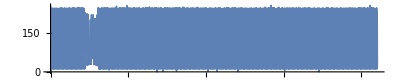

```mathematica
ListLinePlot[int[[;;;;1000]],AspectRatio->0.2,ImageSize->Full,PlotStyle->Thin]
```

```mathematica
Differences[{20*60+29,20*60+57,21*60+24}]
```

{28,27}

```mathematica
81428/(45*145.)
```

12.4794